# A model to study the impact of self-imposed prevention measures and short-term government intervention on mitigating and delaying a COVID-19 epidemic

## Clearing memory

```mathematica
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
```

## Model equations

```mathematica
eq[Intervention_][1]:=S'[t]==-λ[Intervention][t] S[t]-k Subscript[λ, awareness][t] S[t]+Subscript[μ, 1] Sa[t]
eq[Intervention_][2]:=EE'[t]== λ[Intervention][t] S[t]-α EE[t]-k Subscript[λ, awareness][t] EE[t]+Subscript[μ, 1] EEa[t]
eq[Intervention_][3]:=IM'[t]== p α EE[t]-Subscript[γ, 1] IM[t]-k Subscript[λ, awareness][t] IM[t]+Subscript[μ, 1] IMa[t]
eq[Intervention_][4]:=IS'[t]== (1-p) α EE[t]-ν IS[t]-Subscript[λ, awareness][t] IS[t]+Subscript[μ, 2] ISa[t]
eq[Intervention_][5]:=IQ'[t]== ν IS[t]-Subscript[γ, 2] IQ[t]-η IQ[t]
eq[Intervention_][6]:=IQa'[t]==ν^a ISa[t]-Subscript[γ, 3] IQa[t]-Subscript[η, a] IQa[t]
eq[Intervention_][7]:=R'[t]== Subscript[γ, 1] IM[t]+ Subscript[γ, 1] IMa[t]+Subscript[γ, 2] IQ[t]+Subscript[γ, 3] IQa[t]
eq[Intervention_][8]:=RQ'[t]== Subscript[γ, 2] IQ[t]+Subscript[γ, 3] IQa[t]
eq[Intervention_][9]:=Sa'[t]==-Subscript[λ, a][Intervention][t] Sa[t]+k Subscript[λ, awareness][t] S[t]-Subscript[μ, 1] Sa[t]
eq[Intervention_][10]:=EEa'[t]== Subscript[λ, a][Intervention][t] Sa[t]-α EEa[t]+k Subscript[λ, awareness][t] EE[t]-Subscript[μ, 1] EEa[t]
eq[Intervention_][11]:=IMa'[t]== p α EEa[t]-Subscript[γ, 1] IMa[t]+k Subscript[λ, awareness][t] IM[t]-Subscript[μ, 1] IMa[t]
eq[Intervention_][12]:=ISa'[t]== (1-p) α EEa[t]-ν^a ISa[t]+Subscript[λ, awareness][t] IS[t]-Subscript[μ, 2] ISa[t]
eq[Intervention_][13]:=DD'[t]== η IQ[t]+Subscript[η, a] IQa[t]
eq[Intervention_][14]:=DDQ'[t]== η IQ[t]
eq[Intervention_][15]:=DDQa'[t]== Subscript[η, a] IQa[t]
eq[Intervention_][16]:=RM'[t]== Subscript[γ, 1] IM[t]-k Subscript[λ, awareness][t] RM[t]+Subscript[μ, 1] RMa[t]
eq[Intervention_][17]:=RMa'[t]== Subscript[γ, 1] IMa[t]+k Subscript[λ, awareness][t] RM[t]-Subscript[μ, 1] RMa[t]
```

## Numer of variables in the model (including deceased individuals)

```mathematica
numvar=17
eqs[Intervention_]:=Table[eq[Intervention][i],{i,1,numvar}]
lhs[Intervention_]:=eqs[Intervention]⟦All,1⟧;
rhs[Intervention_]:=eqs[Intervention]⟦All,2⟧;
TableForm[eqs[Intervention]]
```

17

S'[t]==Sa[t] μ_1-k S[t] λ_awareness[t]-S[t] λ[Intervention][t]
EE'[t]==-α EE[t]+EEa[t] μ_1-k EE[t] λ_awareness[t]+S[t] λ[Intervention][t]
IM'[t]==p α EE[t]-IM[t] γ_1+IMa[t] μ_1-k IM[t] λ_awareness[t]
IS'[t]==(1-p) α EE[t]-ν IS[t]+ISa[t] μ_2-IS[t] λ_awareness[t]
IQ'[t]==-η IQ[t]+ν IS[t]-IQ[t] γ_2
IQa'[t]==ν^a ISa[t]-IQa[t] γ_3-IQa[t] η_a
R'[t]==IM[t] γ_1+IMa[t] γ_1+IQ[t] γ_2+IQa[t] γ_3
RQ'[t]==IQ[t] γ_2+IQa[t] γ_3
Sa'[t]==-Sa[t] μ_1+k S[t] λ_awareness[t]-Sa[t] λ_a[Intervention][t]
EEa'[t]==-α EEa[t]-EEa[t] μ_1+k EE[t] λ_awareness[t]+Sa[t] λ_a[Intervention][t]
IMa'[t]==p α EEa[t]-IMa[t] γ_1-IMa[t] μ_1+k IM[t] λ_awareness[t]
ISa'[t]==(1-p) α EEa[t]-ν^a ISa[t]-ISa[t] μ_2+IS[t] λ_awareness[t]
DD'[t]==η IQ[t]+IQa[t] η_a
DDQ'[t]==η IQ[t]
DDQa'[t]==IQa[t] η_a
RM'[t]==IM[t] γ_1+RMa[t] μ_1-k RM[t] λ_awareness[t]
RMa'[t]==IMa[t] γ_1-RMa[t] μ_1+k RM[t] λ_awareness[t]

## Model variables

```mathematica
vars={S[t],EE[t],IM[t],IS[t],IQ[t],IQa[t],R[t],RQ[t],Sa[t],EEa[t],IMa[t],ISa[t],DD[t],DDQ[t],DDQa[t],RM[t],RMa[t]}
```

{S[t],EE[t],IM[t],IS[t],IQ[t],IQa[t],R[t],RQ[t],Sa[t],EEa[t],IMa[t],ISa[t],DD[t],DDQ[t],DDQa[t],RM[t],RMa[t]}

## Total population size N(t) is not constant due to disease-related mortality

```mathematica
NN[t]=S[t]+EE[t]+IM[t]+IS[t]+IQ[t]+IQa[t]+R[t]+Sa[t]+EEa[t]+IMa[t]+ISa[t]
```

EE[t]+EEa[t]+IM[t]+IMa[t]+IQ[t]+IQa[t]+IS[t]+ISa[t]+R[t]+S[t]+Sa[t]

## Awareness acquisition rate λ_awareness(t)

```mathematica
Subscript[λ, awareness][t]=δ (IQ[t]+IQa[t])
```

δ (IQ[t]+IQa[t])

## Vector of infectious individuals

```mathematica
VecInf={IM[t],IS[t],IMa[t],ISa[t]}
```

{IM[t],IS[t],IMa[t],ISa[t]}

## Transmission matrix for self-imposed measures and government intervention

Model with disease-awareness and without interventions

```mathematica
TrMatrix[Intervention_/;Intervention=="Baseline"]:=β/(NN[t]-IQ[t]-IQa[t]){{σ,1,σ,1},{σ,1,σ,1}}
```

Model with disease-awareness and mask-wearing

```mathematica
TrMatrix[Intervention_/;Intervention=="Mask"]:=β/(NN[t]-IQ[t]-IQa[t]){{σ,1,Subscript[r, 1] σ,Subscript[r, 1]},{σ,1,Subscript[r, 1] σ,Subscript[r, 1]}}
```

Model with disease-awareness and handwashing

```mathematica
TrMatrix[Intervention_/;Intervention=="Hand"]:=β/(NN[t]-IQ[t]-IQa[t]){{σ,1,σ,1},{Subscript[r, 2] σ,Subscript[r, 2],Subscript[r, 2] σ,Subscript[r, 2]}}
```

Model with disease-awareness and self-imposed social distancing

```mathematica
TrMatrix[Intervention_/;Intervention=="ContactReductionIndividuals"]:=β/(S[t]+EE[t]+IM[t]+IS[t]+RQ[t]+RM[t]+Subscript[r, 3] (Sa[t]+EEa[t]+IMa[t]+ISa[t]+RMa[t])){{σ,1,Subscript[r, 3] σ,Subscript[r, 3]},{Subscript[r, 3] σ,Subscript[r, 3],(Subscript[r, 3])^2 σ,(Subscript[r, 3])^2}}
```

Model with disease-awareness and government-imposed social distancing

```mathematica
TrMatrix[Intervention_/;Intervention=="ContactReductionGovernment"]:=((β If[t≥StartTime&& t≤(StopTime+StartTime),Subscript[r, 4],1])/(NN[t]-IQ[t]-IQa[t])) {{σ,1,σ,1},{σ,1,σ,1}}
```

Model with disease-awareness, government-imposed social distancing and handwashing

```mathematica
TrMatrix[Intervention_/;Intervention=="GovernmentAndHand"]:=((β If[t≥StartTime&& t≤(StopTime+StartTime),Subscript[r, 4],1])/(NN[t]-IQ[t]-IQa[t])){{σ,1,σ,1},{Subscript[r, 2] σ,Subscript[r, 2],Subscript[r, 2] σ,Subscript[r, 2]}}
```

## Force of infection for unaware λ(t)

```mathematica
λ[Intervention_][t]:=(TrMatrix[Intervention].VecInf)⟦1⟧
```

## Force of infection for disease-aware λ_a(t)

```mathematica
Subscript[λ, a][Intervention_][t]:=(TrMatrix[Intervention].VecInf)⟦2⟧
```

## Epidemiological parameters of the model

Average contact rate (unique persons), 1/year

```mathematica
AverageContactRate=c-> 13.85 365
```

c→5055.25

Relative infectivity of mildly infected

```mathematica
RelativeInfectivity=σ->0.5
```

σ→0.5

1/latent period, 1/year

```mathematica
RateInfectiousnessOnset=α-> 365/4
```

α→365/4

Proportion of mildly infected

```mathematica
ProportionMildSymptoms=p->0.82
```

p→0.82

1/recovery period of mildly infected, 1/year

```mathematica
RecoveryRateMildSymptoms=Subscript[γ, 1]->365/7
```

γ_1→365/7

1/delay from onset of infectiousness to diagnosis for individuals with severe symptoms, 1/year

```mathematica
DiagnosisRate=ν-> 365/5
```

ν→73

1/delay from diagnosis to recovery for diagnosed unaware, 1/year

```mathematica
RecoveryRateSevereSymptomsUnaware=Subscript[γ, 2]-> 365/14
```

γ_2→365/14

Case fatality rate of unaware diagnosed

```mathematica
FatalityRateUnaware=f-> 0.016
```

f→0.016

Disease-associated death rate of unaware diagnosed, 1/year

```mathematica
DeathRateDiagnosedUnaware=η-> Subscript[γ, 2] f/(1-f)/.{RecoveryRateSevereSymptomsUnaware,FatalityRateUnaware}
```

η→0.423926

Basic reproduction number

```mathematica
BasicReproductionNumber=Subscript[R, 0]->2.5
```

R_0→2.5

Probability of transmission per contact with infectious with severe symptoms

```mathematica
TransmissionProbability=Solve[Subscript[R, 0]==(p β σ)/Subscript[γ, 1]+((1-p) β)/ν/.β-> c ϵ,ϵ]⟦1,1⟧/.{ProportionMildSymptoms,AverageContactRate,RelativeInfectivity,RecoveryRateMildSymptoms,DiagnosisRate,BasicReproductionNumber}
```

ϵ→0.0478794

Transmission rate of infection via contact with infectious with severe symptoms, 1/year

```mathematica
TransmissionRate=β-> c ϵ/.{AverageContactRate,TransmissionProbability}
```

β→242.042

## Disease-awareness parameters of the model

Rate of awareness acquisition, 1/year

```mathematica
AcquisitionRateAwarenessBaseline=1(*5 10^(-5)*)(* δ *)
```

1

Relative susceptibility to awareness acquisition for susceptible, exposed, infectious with mild symptoms and recovered after a mild infection

```mathematica
RelativeSusceptibilityAwarenessBaseline = 0.5 (* k *)
```

0.5

Rate of awareness fading for individuals who are susceptible, exposed, infectious with mild symptoms and recovered after a mild infection, 1/year

```mathematica
RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline = 365/30 (* Subscript[μ, 1] *)
```

73/6

Rate of awareness fading for individuals with severe symptoms, 1/year

```mathematica
RateAwarenessFadingSevereSymptomsBaseline = 365/60 (* Subscript[μ, 2] *)
```

73/12

1/delay from onset of infectiousness to diagnosis for disease-aware with severe symptoms, 1/year

```mathematica
DiagnosisRateAwareBaseline = 365/3  (* ν^a *)
```

365/3

1/delay from diagnosis to recovery of diagnosed aware, 1/year

```mathematica
RecoveryRateSevereSymptomsAware=Subscript[γ, 3]->365/12
```

γ_3→365/12

Case fatality rate of aware diagnosed

```mathematica
FatalityRateAware=Subscript[f, a]-> 0.01
```

f_a→0.01

Disease-associated death rate of aware diagnosed, 1/year

```mathematica
DeathRateDiagnosedAware=Subscript[η, a]-> Subscript[γ, 3] Subscript[f, a]/(1-Subscript[f, a])/.{RecoveryRateSevereSymptomsAware,FatalityRateAware}
```

η_a→0.307239

## Prevention measures parameters of the model

Duration of government intervention, years

```mathematica
StopTime=3/12;
```

Threshold for initiation of government intervention (10 diagnosed individuals in this notebook)
Please note that if the threshold for initiation of government intervention is larger than 10 individuals, StartTime can be different for fast and slow spread of awareness (Check it!)

```mathematica
StartTimeBaseline=0.1037;
```

## Parameters of the model

```mathematica
Parameters[RelativeSusceptibilityAwareness_,RateAwarenessFadingSusceptibleExposedMildSymptoms_,RateAwarenessFadingSevereSymptoms_,TransmissionRateAwareness_,DiagnosisRateAware_,StartTimeValue_]:={AverageContactRate,RelativeInfectivity,RateInfectiousnessOnset,ProportionMildSymptoms,RecoveryRateMildSymptoms,DiagnosisRate,RecoveryRateSevereSymptomsUnaware,RecoveryRateSevereSymptomsAware,FatalityRateUnaware,FatalityRateAware,DeathRateDiagnosedUnaware,DeathRateDiagnosedAware,BasicReproductionNumber,TransmissionProbability,TransmissionRate,k-> RelativeSusceptibilityAwareness,Subscript[μ, 1]-> RateAwarenessFadingSusceptibleExposedMildSymptoms,Subscript[μ, 2]-> RateAwarenessFadingSevereSymptoms,δ->TransmissionRateAwareness,ν^a->DiagnosisRateAware,StartTime-> StartTimeValue}
```

## Solving differential equations

Start time, year

```mathematica
Subscript[t, start]=0
```

0

End time, year

```mathematica
Subscript[t, end]=2.5;
```

Total population size at the beginning of an outbreak

```mathematica
Ntot=17 10^6
```

17000000

Initial number of infected individuals

```mathematica
InfInit=1
```

1

Number of points per day for discretization of the solution

```mathematica
spacing=20;
```

Initial conditions

```mathematica
ics=Table[ic[i],{i,1,numvar}];

ic[1]=(Ntot-InfInit)==vars⟦1⟧/.{t->Subscript[t, start]}
ic[2]=0==vars⟦2⟧/.{t->Subscript[t, start]}
ic[3]=0==vars⟦3⟧/.{t->Subscript[t, start]}
ic[4]=InfInit==vars⟦4⟧/.{t->Subscript[t, start]}
ic[5]=0==vars⟦5⟧/.{t->Subscript[t, start]}
ic[6]=0==vars⟦6⟧/.{t->Subscript[t, start]}
ic[7]=0==vars⟦7⟧/.{t->Subscript[t, start]}
ic[8]=0==vars⟦8⟧/.{t->Subscript[t, start]}
ic[9]=0==vars⟦9⟧/.{t->Subscript[t, start]}
ic[10]=0==vars⟦10⟧/.{t->Subscript[t, start]}
ic[11]=0==vars⟦11⟧/.{t->Subscript[t, start]}
ic[12]=0==vars⟦12⟧/.{t->Subscript[t, start]}
ic[13]=0==vars⟦13⟧/.{t->Subscript[t, start]}
ic[14]=0==vars⟦14⟧/.{t->Subscript[t, start]}
ic[15]=0==vars⟦15⟧/.{t->Subscript[t, start]}
ic[16]=0==vars⟦16⟧/.{t->Subscript[t, start]}
ic[17]=0==vars⟦17⟧/.{t->Subscript[t, start]}
```

16999999==S[0]

0==EE[0]

0==IM[0]

1==IS[0]

0==IQ[0]

0==IQa[0]

0==R[0]

0==RQ[0]

0==Sa[0]

0==EEa[0]

0==IMa[0]

0==ISa[0]

0==DD[0]

0==DDQ[0]

0==DDQa[0]

0==RM[0]

0==RMa[0]

Solution

```mathematica
solution[Intervention_,Parameters_]:=NDSolve[Join[eqs[Intervention],ics]/.Parameters,vars,{t,Subscript[t, start],Subscript[t, end]}];
```

## Computing peak number of diagnoses per 1000 persons

```mathematica
Peak[Intervention_,Parameters_]:=Max[Flatten[Table[Evaluate[(1000 (IQ[t]+IQa[t])/NN[t])/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]]]
```

Model without disease-awareness

```mathematica
PeakBaseline=Peak["Baseline",Parameters[0,0,0,0,0,0]]
```

45.7976

Model with disease-awareness, no measures

```mathematica
PeakAwareness=Peak["Baseline",Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline]]
```

37.0119

Model with disease-awareness and handwashing with 30% efficacy

```mathematica
PeakHand=Peak["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> 0.7}]]
```

15.884

## Computing time until the peak number of diagnoses since the first case (days)

```mathematica
PeakTiming[Intervention_,Parameters_]:=365 1/((Subscript[t, end] 364  spacing)+1) ReplaceAll[Ordering[Flatten[Table[Evaluate[(1000 (IQ[t]+IQa[t])/NN[t])/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]],-1]⟦1⟧,(x_/;x==Length[Table[t,{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]])->0]//N
```

Model without disease-awareness

```mathematica
PeakTimingBaseline=PeakTiming["Baseline",Parameters[0,0,0,0,0,0]]
```

155.417

Model with disease-awareness, no measures

```mathematica
PeakTimingAwareness=PeakTiming["Baseline",Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline]]
```

162.797

Model with disease-awareness and handwashing with 30% efficacy

```mathematica
PeakTimingHand=PeakTiming["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> 0.7}]]
```

237.297

## Plotting Figure 3 A (main text)

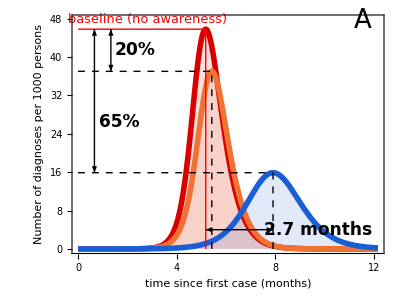

```mathematica
imagePadding={{47.5,5},{60,22.5}};

ymax=50;
tmax=1;

PlotFigure3A[vars_,ylabs_,scenario_]:=Table[Show[Plot[{Evaluate[vars⟦i⟧/.solution["Baseline",Parameters[0,0,0,0,0,0]]],Evaluate[vars⟦i⟧/.solution[scenario,Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline]]],Evaluate[vars⟦i⟧/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> 0.7}]]]},{t,Subscript[t, start],tmax},AspectRatio->0.75,ImageSize->400,PlotRangePadding->None,Filling->Axis,PlotRange->{{0,All},{0,ymax}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotStyle->{{Thickness[0.01],RGBColor[217/255,0,0]},{Thickness[0.01],RGBColor[241/255,115/255,51/255]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]}},FillingStyle->Directive[Opacity[0.125]],ImagePadding->imagePadding,(*PlotLegends->Placed[{Table[Style[Row[{label}],Black,13,"Text"],{label,{"Model without awareness","Model with awareness, no measures","Model with awareness and handwashing with 30% efficacy"}}]},Bottom],*)FrameLabel-> {{ylabs⟦i⟧,None},{"time since first case (months)",None}},
FrameTicks->{{Automatic,None},{{{0,"0"},{60/365,"2"},{120/365,"4"},{180/365,"6"},{240/365,"8"},{300/365,"10"},{360/365,"12"}},None}}],Graphics[{Red,Line[{{PeakTimingBaseline/365,0},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[{Red,Line[{{0,PeakBaseline},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[{Black,Dashed,Line[{{PeakTimingAwareness/365,0},{PeakTimingAwareness/365,PeakAwareness}}]}],Graphics[{Black,Dashed,Line[{{0,PeakAwareness},{PeakTimingAwareness/365,PeakAwareness}}]}],Graphics[{Black,Dashed,Line[{{PeakTimingHand/365,0},{PeakTimingHand/365,PeakHand}}]}],Graphics[{Black,Dashed,Line[{{0,PeakHand},{PeakTimingHand/365,PeakHand}}]}],Graphics[Text[StyleForm["A",FontSize->26],{1*0.95,ymax*0.95}]],Graphics[{Black,Arrowheads[{-.025,.025}],Arrow[{{40/365,PeakBaseline},{40/365,PeakAwareness}}]}],Graphics[{Black,Arrowheads[{-.025,.025}],Arrow[{{20/365,PeakBaseline},{20/365,PeakHand}}]}],
Graphics[{Black,Arrowheads[{-.025,.025}],Arrow[{{PeakTimingBaseline/365,4},{PeakTimingHand/365,4}}]}],
Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> Red],{85/365,PeakBaseline+2}]],Graphics[Text[StyleForm["20%",FontSize->17, FontWeight->"Bold"],{70/365,(PeakBaseline-PeakAwareness)/2+PeakAwareness}]],Graphics[Text[StyleForm["65%",FontSize->17, FontWeight->"Bold"],{50/365,(PeakAwareness-PeakHand)/2+PeakHand}]],
Graphics[Text[StyleForm["2.7 months",FontSize->17, FontWeight->"Bold"],{0.8,4}]]],{i,1,Length[vars]}]⟦1⟧

fig3A=PlotFigure3A[{1000 (IQ[t]+IQa[t])/NN[t]},{"Number of diagnoses per 1000 persons"},"Baseline"]

(*Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure3A",".eps"],fig3A];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure3A",".eps"],fig3A];*)
```

## Computing the deaths at baseline (%)

```mathematica
Deaths[Intervention_,Parameters_]:=Max[Flatten[Table[Evaluate[DD[t]/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]]]

DeathsBaseline=Deaths["Baseline",Parameters[0,0,0,0,0,0]]
```

44205.2

## Computing the attack rate (%)

```mathematica
AttackRate[Intervention_,Parameters_]:=Max[Flatten[Table[Evaluate[((RQ[t]+DD[t])/Ntot 100)/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]]]
```

Model without disease-awareness

```mathematica
AttackRateBaseline=AttackRate["Baseline",Parameters[0,0,0,0,0,0]]
```

16.2519

Model with disease-awareness, no measures

```mathematica
AttackRateAwareness=AttackRate["Baseline",Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline]]
```

15.5895

Model with disease-awareness and handwashing with 30% efficacy

```mathematica
AttackRateHand=AttackRate["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> 0.7}]]
```

11.5675

## Plotting Figure 3 B (main text)

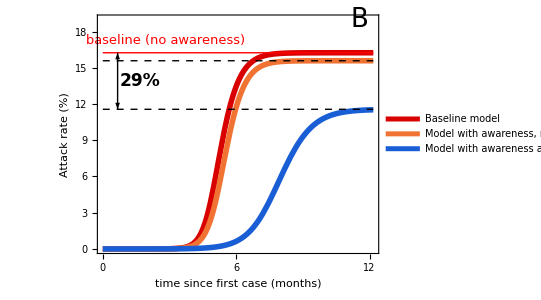

```mathematica
imagePadding={{47.5,5},{60,22.5}};

PlotFigure3B[vars_,ylabs_,scenario_]:=Table[Show[Plot[{Evaluate[vars⟦i⟧/.solution["Baseline",Parameters[0,0,0,0,0,0]]],Evaluate[vars⟦i⟧/.solution[scenario,Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline]]],Evaluate[vars⟦i⟧/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> 0.7}]]]},{t,Subscript[t, start],tmax},AspectRatio->0.75,ImageSize->400,ImagePadding->imagePadding,PlotRangePadding->None,PlotRange->{{0,All},{0,20}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},PlotLegends->Placed[{Table[Style[Row[{label}],Black,13,"Text"],{label,{"Baseline model","Model with awareness, no measures","Model with awareness and handwashing with 30% efficacy"}}]},Bottom],FrameStyle->Directive[Black,17],PlotStyle->{{Thickness[0.01],RGBColor[217/255,0,0]},{Thickness[0.01],RGBColor[241/255,115/255,51/255]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]}},FrameLabel-> {{ylabs⟦i⟧,None},{"time since first case (months)",None}},
FrameTicks->{{Automatic,None},{{{0,"0"},{60/365,"2"},{120/365,"4"},{180/365,"6"},{240/365,"8"},{300/365,"10"},{360/365,"12"},{420/365,"14"},{480/365,"16"},{540/365,"18"},{600/365,"20"},{660/365,"22"},{720/365,"24"}},None}}],Graphics[Text[StyleForm["B",FontSize->26],{1*0.95,20*0.95}]],
Graphics[{Red,Line[{{0,AttackRateBaseline},{1,AttackRateBaseline}}]}],
Graphics[{Black,Dashed,Line[{{0,AttackRateAwareness},{1,AttackRateAwareness}}]}],
Graphics[{Black,Dashed,Line[{{0,AttackRateHand},{1,AttackRateHand}}]}],
Graphics[{Black,Arrowheads[{-.025,.025}],Arrow[{{20/365,AttackRateHand},{20/365,AttackRateBaseline}}]}],
Graphics[Text[StyleForm["29%",FontSize->17, FontWeight->"Bold"],{50/365,(AttackRateBaseline-AttackRateHand)/2+AttackRateHand}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> Red],{85/365,AttackRateBaseline+1}]]],{i,1,Length[vars]}]⟦1⟧

fig3B=PlotFigure3B[{(RQ[t]+DD[t])/Ntot 100},{"Attack rate (%)"},"Baseline"]

(*Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure3B",".eps"],fig3B];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure3B",".eps"],fig3B];*)
```

# Combined intervention: government-imposed social distancing and handwashing (fast spread of awareness)

Time when government-imposed social distancing has to start (10 diagnoses)

```mathematica
(IQ[t]+IQa[t])/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0],{Subscript[r, 2]-> 0.7}]]/.t->0.10437
```

{10.0016}

Impact of government-imposed social distancing with efficacy ranging from 0% (r_4 =1) to 100% (r_4=0) and handwashing with 30% efficacy (r_2=0.7)

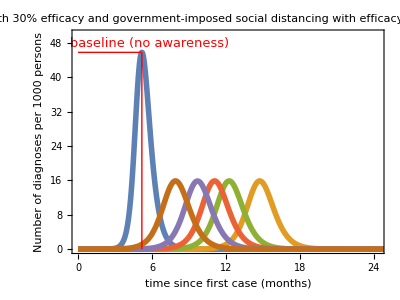
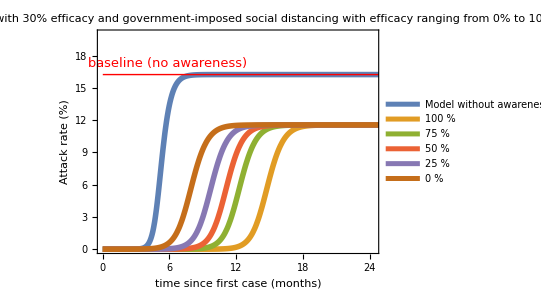

```mathematica
imagePadding={{47.5,5},{60,0}};
relvars={1000 (IQ[t]+IQa[t])/NN[t],(RQ[t]+DD[t])/Ntot 100};
relyalabs={"Number of diagnoses per 1000 persons","Attack rate (%)"};
relylim={50,20};
ReductionFactor=Table[i,{i,0,1,0.25}];

PlotCombinedIntervention[vars_,ylabs_,ylim_,scenario_,title_,parameters_,range_,legend_]:=Table[Show[Plot[{Evaluate[vars⟦i⟧/.solution["Baseline",Parameters[0,0,0,0,0,0]]],Evaluate[Table[vars⟦i⟧/.solution[scenario,parameters],range]]},{t,Subscript[t, start],Subscript[t, end]},AspectRatio->0.75,ImageSize->400,PlotRangePadding->None,PlotRange->{{0,2},{0,ylim⟦i⟧}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotStyle->Thickness[0.01],PlotLabel->Style[title,17,Black],FrameLabel-> {{ylabs⟦i⟧,None},{"time since first case (months)",None}},ImagePadding->imagePadding,FrameTicks->{{Automatic,None},{{{0,"0"},{60/365,"2"},{120/365,"4"},{180/365,"6"},{240/365,"8"},{300/365,"10"},{360/365,"12"},{420/365,"14"},{480/365,"16"},{540/365,"18"},{600/365,"20"},{660/365,"22"},{720/365,"24"}},None}},PlotLegends->If[i==2,Prepend[Table[Style[Row[legend],Black,17,"Text"],range],"Model without awareness"],None]],If[i==2,{Graphics[{Red,Line[{{0,AttackRateBaseline},{Subscript[t, end],AttackRateBaseline}}]}],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> Red],{175/365,AttackRateBaseline+1}]]},{Graphics[{Red,Line[{{PeakTimingBaseline/365,0},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[{Red,Line[{{0,PeakBaseline},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> Red],{175/365,PeakBaseline+2}]]}]],{i,1,Length[vars]}]

PlotCombinedIntervention[relvars,relyalabs,relylim,"GovernmentAndHand","Handwashing with 30% efficacy and\ngovernment-imposed social distancing\nwith efficacy ranging from 0% to 100%",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0.10437],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]->factor}],{factor,ReductionFactor},{IntegerPart[(1-factor) 100], " %"}]
```

## Computing the relative reduction in peak number of diagnoses per 1000 persons (%) for an efficacy of prevention measure ranging from 0% to 100%

```mathematica
ReductionFactor=Table[i,{i,0,1,0.01}];

PeakRange[Intervention_,Parameters_]:=Table[{100 (1-factor),100 (PeakBaseline-Max[Flatten[Table[Evaluate[(1000 (IQ[t]+IQa[t])/NN[t])/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]]])/PeakBaseline},{factor,ReductionFactor}]
```

Model with disease-awareness and mask-wearing

```mathematica
PeakMaskRange=PeakRange["Mask",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,99.9897},{99.,99.9895},{98.,99.9894},{97.,99.9892},{96.,99.9891},{95.,99.9889},{94.,99.9887},{93.,99.9886},{92.,99.9884},{91.,99.9882},{90.,99.988},{89.,99.9878},{88.,99.9876},{87.,99.9874},{86.,99.9872},{85.,99.987},{84.,99.9867},{83.,99.9865},{82.,99.9862},{81.,99.986},{80.,99.9857},{79.,99.9854},{78.,99.9851},{77.,99.9847},{76.,99.9844},{75.,99.984},{74.,99.9837},{73.,99.9832},{72.,99.9828},{71.,99.9823},{70.,99.9818},{69.,99.9812},{68.,99.9806},{67.,99.9799},{66.,99.9792},{65.,99.9783},{64.,99.9772},{63.,99.9758},{62.,99.9733},{61.,99.9687},{60.,99.9621},{59.,99.9522},{58.,99.9356},{57.,99.9046},{56.,99.8396},{55.,99.6973},{54.,99.4204},{53.,98.9754},{52.,98.3611},{51.,97.5905},{50.,96.6796},{49.,95.6439},{48.,94.4978},{47.,93.2544},{46.,91.9255},{45.,90.5218},{44.,89.053},{43.,87.5278},{42.,85.9542},{41.,84.3393},{40.,82.6896},{39.,81.011},{38.,79.3088},{37.,77.5876},{36.,75.8518},{35.,74.1053},{34.,72.3514},{33.,70.5933},{32.,68.8339},{31.,67.0755},{30.,65.3205},{29.,63.5709},{28.,61.8284},{27.,60.0946},{26.,58.3709},{25.,56.6586},{24.,54.9588},{23.,53.2724},{22.,51.6003},{21.,49.9432},{20.,48.3019},{19.,46.6767},{18.,45.0683},{17.,43.4769},{16.,41.903},{15.,40.3467},{14.,38.8084},{13.,37.2881},{12.,35.7861},{11.,34.3024},{10.,32.8369},{9.,31.3899},{8.,29.9612},{7.,28.5509},{6.,27.1588},{5.,25.7848},{4.,24.4289},{3.,23.091},{2.,21.771},{1.,20.4686},{0.,19.1837}}

Model with disease-awareness and handwashing

```mathematica
PeakHandRange=PeakRange["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> factor}]]
```

{{100.,99.989},{99.,99.9889},{98.,99.9887},{97.,99.9885},{96.,99.9884},{95.,99.9882},{94.,99.988},{93.,99.9879},{92.,99.9877},{91.,99.9875},{90.,99.9873},{89.,99.9871},{88.,99.9868},{87.,99.9866},{86.,99.9864},{85.,99.9861},{84.,99.9859},{83.,99.9856},{82.,99.9853},{81.,99.9851},{80.,99.9848},{79.,99.9845},{78.,99.9841},{77.,99.9838},{76.,99.9834},{75.,99.983},{74.,99.9826},{73.,99.9822},{72.,99.9817},{71.,99.9812},{70.,99.9807},{69.,99.9801},{68.,99.9794},{67.,99.9787},{66.,99.9779},{65.,99.9769},{64.,99.9758},{63.,99.9742},{62.,99.9711},{61.,99.9661},{60.,99.9588},{59.,99.9478},{58.,99.9295},{57.,99.8958},{56.,99.8267},{55.,99.6802},{54.,99.401},{53.,98.956},{52.,98.3429},{51.,97.5737},{50.,96.6642},{49.,95.6299},{48.,94.485},{47.,93.2426},{46.,91.9146},{45.,90.5117},{44.,89.0436},{43.,87.5191},{42.,85.9461},{41.,84.3318},{40.,82.6826},{39.,81.0045},{38.,79.3027},{37.,77.5819},{36.,75.8465},{35.,74.1003},{34.,72.3467},{33.,70.589},{32.,68.8298},{31.,67.0717},{30.,65.3169},{29.,63.5675},{28.,61.8252},{27.,60.0916},{26.,58.3681},{25.,56.656},{24.,54.9564},{23.,53.2701},{22.,51.5982},{21.,49.9413},{20.,48.3001},{19.,46.675},{18.,45.0667},{17.,43.4755},{16.,41.9017},{15.,40.3455},{14.,38.8073},{13.,37.2871},{12.,35.7852},{11.,34.3015},{10.,32.8362},{9.,31.3893},{8.,29.9607},{7.,28.5504},{6.,27.1584},{5.,25.7845},{4.,24.4287},{3.,23.0909},{2.,21.7709},{1.,20.4685},{0.,19.1837}}

Model with disease-awareness and self-imposed social distancing

```mathematica
PeakSelfImposedDistancingRange=PeakRange["ContactReductionIndividuals",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 3]-> factor}]]
```

{{100.,99.9815},{99.,99.9815},{98.,99.9814},{97.,99.9814},{96.,99.9813},{95.,99.9813},{94.,99.9812},{93.,99.9811},{92.,99.981},{91.,99.9809},{90.,99.9808},{89.,99.9807},{88.,99.9805},{87.,99.9804},{86.,99.9802},{85.,99.9801},{84.,99.9799},{83.,99.9797},{82.,99.9795},{81.,99.9793},{80.,99.9791},{79.,99.9788},{78.,99.9785},{77.,99.9782},{76.,99.9779},{75.,99.9776},{74.,99.9773},{73.,99.9769},{72.,99.9764},{71.,99.976},{70.,99.9755},{69.,99.9749},{68.,99.9743},{67.,99.9737},{66.,99.9729},{65.,99.972},{64.,99.9709},{63.,99.9696},{62.,99.9678},{61.,99.9641},{60.,99.9578},{59.,99.9482},{58.,99.9325},{57.,99.9037},{56.,99.8448},{55.,99.7205},{54.,99.4833},{53.,99.1012},{52.,98.5672},{51.,97.8875},{50.,97.0726},{49.,96.1339},{48.,95.0826},{47.,93.9295},{46.,92.6848},{45.,91.3579},{44.,89.958},{43.,88.4934},{42.,86.9718},{41.,85.4006},{40.,83.7864},{39.,82.1354},{38.,80.4531},{37.,78.745},{36.,77.0156},{35.,75.2695},{34.,73.5104},{33.,71.7421},{32.,69.9678},{31.,68.1905},{30.,66.4129},{29.,64.6373},{28.,62.8661},{27.,61.1011},{26.,59.3441},{25.,57.5966},{24.,55.8601},{23.,54.1358},{22.,52.4247},{21.,50.728},{20.,49.0463},{19.,47.3805},{18.,45.7311},{17.,44.0988},{16.,42.4839},{15.,40.887},{14.,39.3082},{13.,37.7479},{12.,36.2063},{11.,34.6835},{10.,33.1797},{9.,31.6948},{8.,30.2291},{7.,28.7824},{6.,27.3547},{5.,25.946},{4.,24.5562},{3.,23.1852},{2.,21.8329},{1.,20.4991},{0.,19.1837}}

Model with disease-awareness and government-imposed social distancing

```mathematica
PeakGovernmentImposedDistancingRange=PeakRange["ContactReductionGovernment",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,19.1862},{99.,19.1863},{98.,19.1863},{97.,19.1863},{96.,19.1864},{95.,19.1864},{94.,19.1865},{93.,19.1865},{92.,19.1866},{91.,19.1867},{90.,19.1867},{89.,19.1868},{88.,19.1868},{87.,19.1869},{86.,19.187},{85.,19.1871},{84.,19.1872},{83.,19.1873},{82.,19.1874},{81.,19.1875},{80.,19.1876},{79.,19.1878},{78.,19.1879},{77.,19.1881},{76.,19.1883},{75.,19.1885},{74.,19.1887},{73.,19.1889},{72.,19.1892},{71.,19.1895},{70.,19.1898},{69.,19.1901},{68.,19.1905},{67.,19.1909},{66.,19.1914},{65.,19.1919},{64.,19.1925},{63.,19.1931},{62.,19.1938},{61.,19.1946},{60.,19.1954},{59.,19.1964},{58.,19.1974},{57.,19.1986},{56.,19.1999},{55.,19.2013},{54.,19.2028},{53.,19.2045},{52.,19.2064},{51.,19.2085},{50.,19.2108},{49.,19.2133},{48.,19.2161},{47.,19.2191},{46.,19.2225},{45.,19.2263},{44.,19.2304},{43.,19.2349},{42.,19.2399},{41.,19.2454},{40.,19.2514},{39.,19.2581},{38.,19.2654},{37.,19.2734},{36.,19.2822},{35.,19.2918},{34.,19.3023},{33.,19.3137},{32.,19.3262},{31.,19.3398},{30.,19.3545},{29.,19.3705},{28.,19.3877},{27.,19.4063},{26.,19.4262},{25.,19.4475},{24.,19.4702},{23.,19.4943},{22.,19.5197},{21.,19.5464},{20.,19.5743},{19.,19.6032},{18.,19.6328},{17.,19.6628},{16.,19.6929},{15.,19.7226},{14.,19.7511},{13.,19.7779},{12.,19.8019},{11.,19.8219},{10.,19.8368},{9.,19.8448},{8.,19.8441},{7.,19.8326},{6.,19.8076},{5.,19.7664},{4.,19.7055},{3.,19.6212},{2.,19.5093},{1.,19.3652},{0.,19.1837}}

Model with disease-awareness and combined intervention (government-imposed social distancing and handwashing with 30% efficacy)

```mathematica
PeakCombinedRange=PeakRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0.10437],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]-> factor}]]
```

{{100.,65.3188},{99.,65.3188},{98.,65.3188},{97.,65.3189},{96.,65.3189},{95.,65.3189},{94.,65.319},{93.,65.319},{92.,65.319},{91.,65.3191},{90.,65.3191},{89.,65.3192},{88.,65.3192},{87.,65.3193},{86.,65.3193},{85.,65.3194},{84.,65.3195},{83.,65.3195},{82.,65.3196},{81.,65.3197},{80.,65.3198},{79.,65.3199},{78.,65.32},{77.,65.3201},{76.,65.3202},{75.,65.3204},{74.,65.3205},{73.,65.3207},{72.,65.3208},{71.,65.321},{70.,65.3212},{69.,65.3215},{68.,65.3217},{67.,65.322},{66.,65.3223},{65.,65.3226},{64.,65.3229},{63.,65.3233},{62.,65.3237},{61.,65.3241},{60.,65.3246},{59.,65.3251},{58.,65.3256},{57.,65.3262},{56.,65.3268},{55.,65.3274},{54.,65.3281},{53.,65.3289},{52.,65.3296},{51.,65.3304},{50.,65.3313},{49.,65.3322},{48.,65.3331},{47.,65.3341},{46.,65.3352},{45.,65.3363},{44.,65.3374},{43.,65.3386},{42.,65.3399},{41.,65.3412},{40.,65.3426},{39.,65.344},{38.,65.3455},{37.,65.3471},{36.,65.3487},{35.,65.3503},{34.,65.3521},{33.,65.3538},{32.,65.3557},{31.,65.3576},{30.,65.3595},{29.,65.3615},{28.,65.3636},{27.,65.3656},{26.,65.3677},{25.,65.3699},{24.,65.372},{23.,65.3741},{22.,65.3763},{21.,65.3783},{20.,65.3804},{19.,65.3823},{18.,65.3841},{17.,65.3858},{16.,65.3873},{15.,65.3885},{14.,65.3895},{13.,65.3901},{12.,65.3903},{11.,65.39},{10.,65.3891},{9.,65.3876},{8.,65.3852},{7.,65.3819},{6.,65.3774},{5.,65.3718},{4.,65.3646},{3.,65.3559},{2.,65.3452},{1.,65.3323},{0.,65.3169}}

## Plotting Figure 5 A (main text) (fast spread of awareness)

```mathematica
imagePadding={{80,15},{50,5}};

fig5A=Show[ListLinePlot[{PeakMaskRange⟦;;;;5⟧,PeakHandRange,PeakSelfImposedDistancingRange,PeakGovernmentImposedDistancingRange⟦;;;;5⟧(*,PeakCombinedRange*)},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-2.5,102.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]}(*,{Thickness[0.01],RGBColor[185/255,76/255,225/255]}*)},PlotRangePadding->None,PlotMarkers->{Graphics[{RGBColor[248/255,196/255,0],Thick,Circle[]},ImageSize->10],"","","",""},PlotLabel->Style[Row[{"Fast spread of awareness"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of prevention measure (%)",None}}],Graphics[Text[StyleForm["A",FontSize->26],{100*0.05,100*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]],{27.5,5}]],Graphics[{RGBColor[217/255,0,0],Thickness[0.005],Line[{{0,0},{100,0}}]}],Graphics[{Black,Arrow[{{80,40},{80,95}}]}],
Graphics[Text[StyleForm["no large epidemic",FontSize->15,FontColor-> Black],{80,35}]]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure5A",".eps"],fig5A];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure5A",".eps"],fig5A];
```

-Graphics-

## Computing the attack rate (%) for an efficacy of prevention measure ranging from 0% to 100%

```mathematica
AttackRateRange[Intervention_,Parameters_]:=Table[{(1-factor) 100,Max[Flatten[Table[Evaluate[((RQ[t]+DD[t])/Ntot 100)/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]]]},{factor,ReductionFactor}]
```

Model with disease-awareness and mask-wearing

```mathematica
AttackRateMaskRange=AttackRateRange["Mask",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,0.0139929},{99.,0.0143083},{98.,0.0146382},{97.,0.0149835},{96.,0.0153453},{95.,0.0157249},{94.,0.0161236},{93.,0.0165428},{92.,0.0169843},{91.,0.0174499},{90.,0.0179415},{89.,0.0184615},{88.,0.0190124},{87.,0.0195969},{86.,0.0202184},{85.,0.0208804},{84.,0.0215871},{83.,0.0223432},{82.,0.0231541},{81.,0.024026},{80.,0.024966},{79.,0.0259827},{78.,0.0270857},{77.,0.0282867},{76.,0.0295994},{75.,0.0310405},{74.,0.0326297},{73.,0.0343915},{72.,0.0363557},{71.,0.0385599},{70.,0.0410512},{69.,0.0438904},{68.,0.0471564},{67.,0.0509542},{66.,0.0554265},{65.,0.0607718},{64.,0.0672748},{63.,0.0753581},{62.,0.0856753},{61.,0.09929},{60.,0.118038},{59.,0.145326},{58.,0.18798},{57.,0.260716},{56.,0.396241},{55.,0.661302},{54.,1.14896},{53.,1.87324},{52.,2.67945},{51.,3.4173},{50.,4.06489},{49.,4.65068},{48.,5.19629},{47.,5.71174},{46.,6.20132},{45.,6.66722},{44.,7.11091},{43.,7.53366},{42.,7.93661},{41.,8.32086},{40.,8.68743},{39.,9.03728},{38.,9.37132},{37.,9.6904},{36.,9.99534},{35.,10.2869},{34.,10.5658},{33.,10.8326},{32.,11.0881},{31.,11.3328},{30.,11.5672},{29.,11.7919},{28.,12.0072},{27.,12.2137},{26.,12.4119},{25.,12.602},{24.,12.7845},{23.,12.9598},{22.,13.1282},{21.,13.29},{20.,13.4455},{19.,13.595},{18.,13.7388},{17.,13.8772},{16.,14.0103},{15.,14.1385},{14.,14.2619},{13.,14.3808},{12.,14.4953},{11.,14.6056},{10.,14.7119},{9.,14.8145},{8.,14.9133},{7.,15.0087},{6.,15.1007},{5.,15.1895},{4.,15.2752},{3.,15.3579},{2.,15.4378},{1.,15.5149},{0.,15.5895}}

Model with disease-awareness and handwashing

```mathematica
AttackRateHandRange=AttackRateRange["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> factor}]]
```

{{100.,0.0140407},{99.,0.0143743},{98.,0.0147234},{97.,0.0150892},{96.,0.0154729},{95.,0.0158757},{94.,0.0162993},{93.,0.0167452},{92.,0.0172151},{91.,0.0177111},{90.,0.0182355},{89.,0.0187905},{88.,0.0193791},{87.,0.0200044},{86.,0.0206697},{85.,0.0213792},{84.,0.0221373},{83.,0.0229492},{82.,0.0238208},{81.,0.0247589},{80.,0.0257713},{79.,0.0268674},{78.,0.0280578},{77.,0.0293553},{76.,0.030775},{75.,0.0323351},{74.,0.0340576},{73.,0.0359691},{72.,0.0381028},{71.,0.0404998},{70.,0.0432124},{69.,0.0463074},{68.,0.0498723},{67.,0.054023},{66.,0.0589172},{65.,0.0647747},{64.,0.0719103},{63.,0.0807912},{62.,0.0921395},{61.,0.107127},{60.,0.127769},{59.,0.157776},{58.,0.204509},{57.,0.283557},{56.,0.428699},{55.,0.706238},{54.,1.20244},{53.,1.92033},{52.,2.70967},{51.,3.43419},{50.,4.075},{49.,4.65767},{48.,5.20165},{47.,5.71606},{46.,6.20487},{45.,6.67016},{44.,7.11336},{43.,7.53571},{42.,7.93835},{41.,8.32233},{40.,8.68868},{39.,9.03835},{38.,9.37224},{37.,9.6912},{36.,9.99603},{35.,10.2875},{34.,10.5663},{33.,10.8331},{32.,11.0885},{31.,11.3332},{30.,11.5675},{29.,11.7921},{28.,12.0075},{27.,12.214},{26.,12.4121},{25.,12.6022},{24.,12.7847},{23.,12.96},{22.,13.1283},{21.,13.2901},{20.,13.4456},{19.,13.5951},{18.,13.7389},{17.,13.8773},{16.,14.0104},{15.,14.1386},{14.,14.262},{13.,14.3808},{12.,14.4953},{11.,14.6056},{10.,14.712},{9.,14.8145},{8.,14.9134},{7.,15.0087},{6.,15.1007},{5.,15.1895},{4.,15.2752},{3.,15.3579},{2.,15.4378},{1.,15.5149},{0.,15.5895}}

Model with disease-awareness and self-imposed social distancing

```mathematica
AttackRateSelfImposedDistancingRange=AttackRateRange["ContactReductionIndividuals",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 3]-> factor}]]
```

{{100.,0.0389164},{99.,0.0383051},{98.,0.0378212},{97.,0.0374449},{96.,0.0371617},{95.,0.0369607},{94.,0.036834},{93.,0.0367758},{92.,0.0367817},{91.,0.0368486},{90.,0.0369746},{89.,0.0371585},{88.,0.0374002},{87.,0.0377},{86.,0.0380591},{85.,0.0384794},{84.,0.0389636},{83.,0.039515},{82.,0.0401379},{81.,0.0408375},{80.,0.0416201},{79.,0.0424935},{78.,0.0434666},{77.,0.0445505},{76.,0.0457582},{75.,0.0471058},{74.,0.0486125},{73.,0.0503019},{72.,0.0522034},{71.,0.0543533},{70.,0.0567976},{69.,0.0595955},{68.,0.0628236},{67.,0.066584},{66.,0.0710146},{65.,0.0763075},{64.,0.0827377},{63.,0.0907127},{62.,0.100864},{61.,0.114217},{60.,0.132549},{59.,0.159166},{58.,0.200704},{57.,0.271327},{56.,0.401359},{55.,0.647841},{54.,1.07891},{53.,1.68977},{52.,2.36316},{51.,2.99944},{50.,3.58276},{49.,4.12858},{48.,4.64895},{47.,5.14917},{46.,5.63109},{45.,6.09536},{44.,6.54232},{43.,6.97235},{42.,7.38584},{41.,7.78324},{40.,8.16503},{39.,8.53172},{38.,8.88381},{37.,9.22182},{36.,9.54628},{35.,9.8577},{34.,10.1566},{33.,10.4435},{32.,10.7189},{31.,10.9832},{30.,11.2369},{29.,11.4805},{28.,11.7143},{27.,11.9387},{26.,12.1542},{25.,12.3611},{24.,12.5598},{23.,12.7506},{22.,12.9339},{21.,13.11},{20.,13.2791},{19.,13.4417},{18.,13.598},{17.,13.7482},{16.,13.8927},{15.,14.0316},{14.,14.1652},{13.,14.2938},{12.,14.4175},{11.,14.5365},{10.,14.6511},{9.,14.7615},{8.,14.8677},{7.,14.97},{6.,15.0686},{5.,15.1636},{4.,15.2551},{3.,15.3433},{2.,15.4284},{1.,15.5104},{0.,15.5895}}

Model with disease-awareness and government-imposed social distancing

```mathematica
AttackRateGovernmentImposedDistancingRange=AttackRateRange["ContactReductionGovernment",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,15.5894},{99.,15.5894},{98.,15.5894},{97.,15.5894},{96.,15.5894},{95.,15.5894},{94.,15.5894},{93.,15.5894},{92.,15.5894},{91.,15.5894},{90.,15.5894},{89.,15.5894},{88.,15.5894},{87.,15.5894},{86.,15.5894},{85.,15.5894},{84.,15.5894},{83.,15.5894},{82.,15.5894},{81.,15.5894},{80.,15.5894},{79.,15.5894},{78.,15.5894},{77.,15.5894},{76.,15.5894},{75.,15.5894},{74.,15.5893},{73.,15.5893},{72.,15.5893},{71.,15.5893},{70.,15.5893},{69.,15.5893},{68.,15.5893},{67.,15.5893},{66.,15.5893},{65.,15.5893},{64.,15.5893},{63.,15.5892},{62.,15.5892},{61.,15.5892},{60.,15.5892},{59.,15.5892},{58.,15.5891},{57.,15.5891},{56.,15.5891},{55.,15.589},{54.,15.589},{53.,15.589},{52.,15.5889},{51.,15.5889},{50.,15.5888},{49.,15.5888},{48.,15.5887},{47.,15.5886},{46.,15.5885},{45.,15.5884},{44.,15.5883},{43.,15.5882},{42.,15.5881},{41.,15.588},{40.,15.5878},{39.,15.5877},{38.,15.5875},{37.,15.5873},{36.,15.5871},{35.,15.5869},{34.,15.5866},{33.,15.5863},{32.,15.586},{31.,15.5857},{30.,15.5853},{29.,15.5849},{28.,15.5845},{27.,15.5841},{26.,15.5836},{25.,15.5831},{24.,15.5825},{23.,15.5819},{22.,15.5813},{21.,15.5807},{20.,15.58},{19.,15.5793},{18.,15.5786},{17.,15.5778},{16.,15.5771},{15.,15.5764},{14.,15.5757},{13.,15.575},{12.,15.5744},{11.,15.5739},{10.,15.5735},{9.,15.5733},{8.,15.5733},{7.,15.5736},{6.,15.5742},{5.,15.5752},{4.,15.5767},{3.,15.5787},{2.,15.5815},{1.,15.585},{0.,15.5895}}

Model with disease-awareness and combined intervention (government-imposed social distancing and handwashing with 30% efficacy)

```mathematica
AttackRateCombinedRange=AttackRateRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0.10437],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]-> factor}]]
```

{{100.,11.5674},{99.,11.5674},{98.,11.5674},{97.,11.5674},{96.,11.5674},{95.,11.5674},{94.,11.5674},{93.,11.5674},{92.,11.5674},{91.,11.5674},{90.,11.5674},{89.,11.5674},{88.,11.5674},{87.,11.5674},{86.,11.5674},{85.,11.5674},{84.,11.5674},{83.,11.5674},{82.,11.5674},{81.,11.5674},{80.,11.5673},{79.,11.5673},{78.,11.5673},{77.,11.5673},{76.,11.5673},{75.,11.5673},{74.,11.5673},{73.,11.5673},{72.,11.5673},{71.,11.5673},{70.,11.5673},{69.,11.5672},{68.,11.5672},{67.,11.5672},{66.,11.5672},{65.,11.5672},{64.,11.5672},{63.,11.5671},{62.,11.5671},{61.,11.5671},{60.,11.5671},{59.,11.567},{58.,11.567},{57.,11.567},{56.,11.5669},{55.,11.5669},{54.,11.5668},{53.,11.5668},{52.,11.5667},{51.,11.5667},{50.,11.5666},{49.,11.5666},{48.,11.5665},{47.,11.5665},{46.,11.5664},{45.,11.5663},{44.,11.5663},{43.,11.5662},{42.,11.5661},{41.,11.566},{40.,11.5659},{39.,11.5659},{38.,11.5658},{37.,11.5657},{36.,11.5656},{35.,11.5655},{34.,11.5654},{33.,11.5652},{32.,11.5651},{31.,11.565},{30.,11.5649},{29.,11.5648},{28.,11.5646},{27.,11.5645},{26.,11.5644},{25.,11.5643},{24.,11.5641},{23.,11.564},{22.,11.5639},{21.,11.5637},{20.,11.5636},{19.,11.5635},{18.,11.5634},{17.,11.5633},{16.,11.5632},{15.,11.5631},{14.,11.563},{13.,11.563},{12.,11.563},{11.,11.563},{10.,11.5631},{9.,11.5632},{8.,11.5633},{7.,11.5635},{6.,11.5638},{5.,11.5641},{4.,11.5646},{3.,11.5651},{2.,11.5658},{1.,11.5666},{0.,11.5675}}

## Plotting Figure 5 B (main text) (fast spread of awareness)

```mathematica
imagePadding={{80,15},{50,5}};

fig5B=Show[ListLinePlot[{AttackRateMaskRange⟦;;;;5⟧,AttackRateHandRange,AttackRateSelfImposedDistancingRange,AttackRateGovernmentImposedDistancingRange⟦;;;;5⟧(*,AttackRateCombinedRange*)},AspectRatio->0.75,ImageSize->400,PlotRange->{{0,100},{-0.35,20}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{Graphics[{RGBColor[248/255,196/255,0],Thick,Circle[]},ImageSize->10],"","","",""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]}(*,{Thickness[0.01],RGBColor[185/255,76/255,225/255]}*)},FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of prevention measure (%)",None}},PlotRangePadding->None,PlotLabel->Style[Row[{"Fast spread of awareness"}],17,Black],ImagePadding->imagePadding],Graphics[{RGBColor[217/255,0,0]
,Thickness[0.005],Line[{{0,AttackRateBaseline},{100,AttackRateBaseline}}]}],Graphics[Text[StyleForm["B",FontSize->26],{100*0.05,20*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]
],{72.5,17.25}]],Graphics[{Black,Arrow[{{80,6},{80,1}}]}],
Graphics[Text[StyleForm["no large epidemic",FontSize->15,FontColor-> Black],{80,7}]]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure5B",".eps"],fig5B];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure5B",".eps"],fig5B];
```

-Graphics-

## Computing time until the peak number of diagnoses since the first case for an efficacy of prevention measure ranging from 0% to 100%

```mathematica
PeakTimingRange[Intervention_,Parameters_]:=
Table[{(1-factor) 100,365 1/((Subscript[t, end] 364  spacing)+1)ReplaceAll[Ordering[Flatten[Table[Evaluate[(1000 (IQ[t]+IQa[t])/NN[t])/.First@solution[Intervention,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]],-1]⟦1⟧,(x_/;x==Length[Table[t,{t,Subscript[t, start],Subscript[t, end],1/(Subscript[t, end] 364 spacing)}]])->0]},{factor,ReductionFactor}]
```

Model with disease-awareness and mask-wearing

```mathematica
PeakTimingMaskRange=PeakTimingRange["Mask",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,71.893},{99.,72.0936},{98.,72.3142},{97.,72.5348},{96.,72.7553},{95.,72.996},{94.,73.2366},{93.,73.4773},{92.,73.738},{91.,73.9987},{90.,74.2794},{89.,74.5802},{88.,74.8811},{87.,75.1819},{86.,75.5228},{85.,75.8637},{84.,76.2247},{83.,76.6057},{82.,77.0068},{81.,77.4479},{80.,77.8891},{79.,78.3905},{78.,78.8918},{77.,79.4533},{76.,80.075},{75.,80.7167},{74.,81.4587},{73.,82.2609},{72.,83.1432},{71.,84.166},{70.,85.3291},{69.,86.7128},{68.,88.3572},{67.,90.4027},{66.,93.0699},{65.,96.7798},{64.,102.676},{63.,115.129},{62.,266.155},{61.,367.647},{60.,439.801},{59.,513.178},{58.,593.814},{57.,679.344},{56.,751.137},{55.,773.376},{54.,737.46},{53.,675.855},{52.,614.289},{51.,560.866},{50.,516.166},{49.,478.886},{48.,447.542},{47.,420.93},{46.,398.089},{45.,378.276},{44.,360.909},{43.,345.588},{42.,331.931},{41.,319.698},{40.,308.669},{39.,298.682},{38.,289.557},{37.,281.215},{36.,273.554},{35.,266.475},{34.,259.938},{33.,253.842},{32.,248.166},{31.,242.872},{30.,237.919},{29.,233.266},{28.,228.875},{27.,224.743},{26.,220.853},{25.,217.163},{24.,213.654},{23.,210.325},{22.,207.176},{21.,204.168},{20.,201.3},{19.,198.573},{18.,195.946},{17.,193.439},{16.,191.053},{15.,188.747},{14.,186.541},{13.,184.415},{12.,182.37},{11.,180.404},{10.,178.519},{9.,176.694},{8.,174.93},{7.,173.245},{6.,171.601},{5.,170.016},{4.,168.472},{3.,166.988},{2.,165.544},{1.,164.141},{0.,162.797}}

Model with disease-awareness and handwashing

```mathematica
PeakTimingHandRange=PeakTimingRange["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> factor}]]
```

{{100.,72.8356},{99.,73.0361},{98.,73.2567},{97.,73.4572},{96.,73.6778},{95.,73.8984},{94.,74.1391},{93.,74.3797},{92.,74.6404},{91.,74.9011},{90.,75.1618},{89.,75.4426},{88.,75.7434},{87.,76.0442},{86.,76.365},{85.,76.706},{84.,77.0469},{83.,77.4279},{82.,77.8089},{81.,78.23},{80.,78.6712},{79.,79.1325},{78.,79.6338},{77.,80.1753},{76.,80.7769},{75.,81.4186},{74.,82.1205},{73.,82.9026},{72.,83.7649},{71.,84.7676},{70.,85.9107},{69.,87.2543},{68.,88.8987},{67.,90.9241},{66.,93.6113},{65.,97.4416},{64.,103.718},{63.,118.979},{62.,295.173},{61.,378.396},{60.,445.817},{59.,515.223},{58.,590.766},{57.,669.257},{56.,733.349},{55.,752.52},{54.,719.712},{53.,662.619},{52.,604.503},{51.,553.406},{50.,510.27},{49.,474.093},{48.,443.551},{47.,417.561},{46.,395.181},{45.,375.729},{44.,358.683},{43.,343.603},{42.,330.166},{41.,318.114},{40.,307.225},{39.,297.358},{38.,288.374},{37.,280.132},{36.,272.552},{35.,265.553},{34.,259.076},{33.,253.059},{32.,247.444},{31.,242.21},{30.,237.297},{29.,232.685},{28.,228.353},{27.,224.262},{26.,220.392},{25.,216.742},{24.,213.273},{23.,209.964},{22.,206.835},{21.,203.867},{20.,201.02},{19.,198.292},{18.,195.705},{17.,193.219},{16.,190.832},{15.,188.566},{14.,186.36},{13.,184.255},{12.,182.229},{11.,180.284},{10.,178.419},{9.,176.594},{8.,174.849},{7.,173.165},{6.,171.541},{5.,169.956},{4.,168.432},{3.,166.948},{2.,165.524},{1.,164.141},{0.,162.797}}

Model with disease-awareness and self-imposed social distancing

```mathematica
PeakTimingSelfImposedDistancingRange=PeakTimingRange["ContactReductionIndividuals",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 3]-> factor}]]
```

{{100.,77.3677},{99.,77.3477},{98.,77.3477},{97.,77.3677},{96.,77.4078},{95.,77.468},{94.,77.5482},{93.,77.6284},{92.,77.7287},{91.,77.849},{90.,77.9894},{89.,78.1498},{88.,78.3103},{87.,78.4907},{86.,78.6913},{85.,78.9119},{84.,79.1525},{83.,79.4132},{82.,79.714},{81.,80.0148},{80.,80.3557},{79.,80.7167},{78.,81.1178},{77.,81.5389},{76.,82.0202},{75.,82.5617},{74.,83.1432},{73.,83.805},{72.,84.547},{71.,85.3893},{70.,86.3518},{69.,87.4949},{68.,88.8385},{67.,90.503},{66.,92.6086},{65.,95.4362},{64.,99.5272},{63.,106.346},{62.,123.291},{61.,272.712},{60.,357.56},{59.,432.281},{58.,512.496},{57.,597.805},{56.,671.744},{55.,703.248},{54.,682.653},{53.,634.925},{52.,583.246},{51.,536.581},{50.,496.593},{49.,462.762},{48.,434.025},{47.,409.439},{46.,388.202},{45.,369.693},{44.,353.429},{43.,338.99},{42.,326.116},{41.,314.545},{40.,304.096},{39.,294.591},{38.,285.908},{37.,277.946},{36.,270.607},{35.,263.828},{34.,257.531},{33.,251.696},{32.,246.221},{31.,241.127},{30.,236.335},{29.,231.842},{28.,227.591},{27.,223.58},{26.,219.81},{25.,216.221},{24.,212.811},{23.,209.583},{22.,206.494},{21.,203.567},{20.,200.759},{19.,198.072},{18.,195.525},{17.,193.058},{16.,190.712},{15.,188.446},{14.,186.28},{13.,184.195},{12.,182.189},{11.,180.244},{10.,178.379},{9.,176.574},{8.,174.849},{7.,173.165},{6.,171.541},{5.,169.956},{4.,168.432},{3.,166.968},{2.,165.524},{1.,164.141},{0.,162.797}}

Model with disease-awareness and government-imposed social distancing

```mathematica
PeakTimingGovernmentImposedDistancingRange=PeakTimingRange["ContactReductionGovernment",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,366.865},{99.,361.952},{98.,357.319},{97.,352.968},{96.,348.817},{95.,344.866},{94.,341.096},{93.,337.466},{92.,333.977},{91.,330.608},{90.,327.359},{89.,324.21},{88.,321.162},{87.,318.194},{86.,315.307},{85.,312.499},{84.,309.752},{83.,307.085},{82.,304.478},{81.,301.931},{80.,299.424},{79.,296.977},{78.,294.591},{77.,292.265},{76.,289.959},{75.,287.712},{74.,285.507},{73.,283.341},{72.,281.215},{71.,279.129},{70.,277.084},{69.,275.079},{68.,273.093},{67.,271.148},{66.,269.243},{65.,267.358},{64.,265.493},{63.,263.648},{62.,261.843},{61.,260.038},{60.,258.253},{59.,256.489},{58.,254.744},{57.,252.999},{56.,251.255},{55.,249.51},{54.,247.785},{53.,246.061},{52.,244.316},{51.,242.591},{50.,240.867},{49.,239.142},{48.,237.417},{47.,235.693},{46.,233.968},{45.,232.264},{44.,230.539},{43.,228.834},{42.,227.13},{41.,225.445},{40.,223.761},{39.,222.076},{38.,220.412},{37.,218.747},{36.,217.103},{35.,215.458},{34.,213.814},{33.,212.19},{32.,210.565},{31.,208.961},{30.,207.357},{29.,205.772},{28.,204.188},{27.,202.624},{26.,201.06},{25.,199.496},{24.,197.951},{23.,196.407},{22.,194.883},{21.,193.359},{20.,191.835},{19.,190.331},{18.,188.847},{17.,187.343},{16.,185.859},{15.,184.395},{14.,182.911},{13.,181.447},{12.,179.983},{11.,178.539},{10.,177.095},{9.,175.652},{8.,174.208},{7.,172.764},{6.,171.34},{5.,169.896},{4.,168.472},{3.,167.049},{2.,165.625},{1.,164.221},{0.,162.797}}

Model with disease-awareness and combined intervention (government-imposed social distancing and handwashing with 30% efficacy)

```mathematica
PeakTimingCombinedRange=PeakTimingRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0.10437],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]-> factor}]]
```

{{100.,442.247},{99.,437.575},{98.,433.163},{97.,428.992},{96.,425.041},{95.,421.251},{94.,417.641},{93.,414.192},{92.,410.863},{91.,407.655},{90.,404.566},{89.,401.578},{88.,398.67},{87.,395.883},{86.,393.156},{85.,390.508},{84.,387.962},{83.,385.455},{82.,383.028},{81.,380.682},{80.,378.396},{79.,376.15},{78.,373.984},{77.,371.878},{76.,369.833},{75.,367.828},{74.,365.902},{73.,364.017},{72.,362.192},{71.,360.428},{70.,358.703},{69.,357.039},{68.,355.434},{67.,353.87},{66.,352.346},{65.,350.882},{64.,349.478},{63.,348.095},{62.,346.751},{61.,345.468},{60.,344.204},{59.,342.961},{58.,341.758},{57.,340.574},{56.,339.391},{55.,338.228},{54.,337.065},{53.,335.902},{52.,334.739},{51.,333.556},{50.,332.372},{49.,331.149},{48.,329.906},{47.,328.642},{46.,327.339},{45.,325.995},{44.,324.612},{43.,323.188},{42.,321.724},{41.,320.22},{40.,318.656},{39.,317.071},{38.,315.427},{37.,313.742},{36.,312.018},{35.,310.253},{34.,308.468},{33.,306.623},{32.,304.758},{31.,302.853},{30.,300.928},{29.,298.963},{28.,296.977},{27.,294.972},{26.,292.947},{25.,290.901},{24.,288.836},{23.,286.75},{22.,284.664},{21.,282.559},{20.,280.433},{19.,278.307},{18.,276.182},{17.,274.036},{16.,271.89},{15.,269.744},{14.,267.578},{13.,265.413},{12.,263.267},{11.,261.101},{10.,258.935},{9.,256.769},{8.,254.604},{7.,252.438},{6.,250.272},{5.,248.106},{4.,245.94},{3.,243.775},{2.,241.609},{1.,239.463},{0.,237.297}}

## Plotting Figure 5 C (main text) (fast spread of awareness)

```mathematica
fig5C=Show[ListLinePlot[{PeakTimingMaskRange⟦;;;;3⟧,PeakTimingHandRange,PeakTimingSelfImposedDistancingRange,PeakTimingGovernmentImposedDistancingRange⟦;;;;5⟧(*,PeakTimingCombinedRange*)},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,800}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{Graphics[{RGBColor[248/255,196/255,0],Thick,Circle[]},ImageSize->10],"","","",""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]}(*,{Thickness[0.01],RGBColor[185/255,76/255,225/255]}*)},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of prevention measure (%)",None}},PlotRangePadding->None,ImagePadding->imagePadding,PlotLabel->Style[Row[{"Fast spread of awareness"}],17,Black],PlotLegends->Table[Style[Row[{label}],Black,13,"Text"],{label,{"Mask-wearing","Handwashing","Self-imposed social distancing","Government-imposed social distancing"(*,"Government-imposed social distancing\nand handwashing with 30% efficacy"*)}}],FrameTicks->{{{{0,"0"},{365 18/12,"18"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3,"36"},{365 4,"48"},{365 5,"60"},{365 6,"72"}},None},{Automatic,None}}],Graphics[{RGBColor[217/255,0,0]
,Thickness[0.005],Line[{{0,PeakTimingBaseline},{100,PeakTimingBaseline}}]}],Graphics[Text[StyleForm["C",FontSize->26],{100*0.05,800*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]
],{28,125}]],Graphics[{Black,Arrow[{{80,365 16/12},{80,365/3.5}}]}],
Graphics[Text[StyleForm["no large epidemic",FontSize->15,FontColor-> Black],{80,365 18/12}]]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure5C",".eps"],fig5C];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure5C",".eps"],fig5C];
```

-Graphics-

# Combined intervention: government-imposed social distancing and handwashing (slow spread of awareness)

Time when government-imposed social distancing has to start (10 diagnoses)

```mathematica
(IQ[t]+IQa[t])/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,0],{Subscript[r, 2]-> 0.7}]]/.t->0.10393
```

{10.0025}

Impact of government-imposed social distancing with efficacy ranging from 0% (r_4 =1) to 100% (r_4=0) and handwashing with 30% efficacy (r_2=0.7)

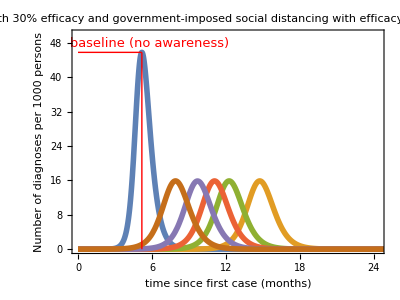
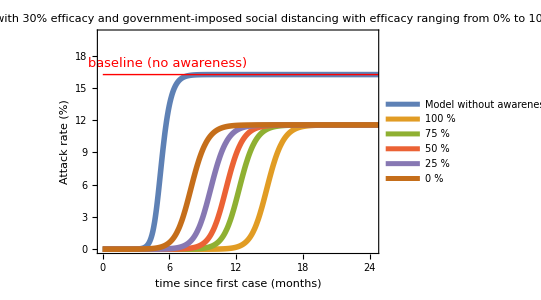

```mathematica
imagePadding={{47.5,5},{60,0}};
relvars={1000 (IQ[t]+IQa[t])/NN[t],(RQ[t]+DD[t])/Ntot 100};
relyalabs={"Number of diagnoses per 1000 persons","Attack rate (%)"};
relylim={50,20};
ReductionFactor=Table[i,{i,0,1,0.25}];

PlotCombinedIntervention[vars_,ylabs_,ylim_,scenario_,title_,parameters_,range_,legend_]:=Table[Show[Plot[{Evaluate[vars⟦i⟧/.solution["Baseline",Parameters[0,0,0,0,0,0]]],Evaluate[Table[vars⟦i⟧/.solution[scenario,parameters],range]]},{t,Subscript[t, start],Subscript[t, end]},AspectRatio->0.75,ImageSize->400,PlotRangePadding->None,PlotRange->{{0,2},{0,ylim⟦i⟧}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotStyle->Thickness[0.01],PlotLabel->Style[title,17,Black],FrameLabel-> {{ylabs⟦i⟧,None},{"time since first case (months)",None}},ImagePadding->imagePadding,FrameTicks->{{Automatic,None},{{{0,"0"},{60/365,"2"},{120/365,"4"},{180/365,"6"},{240/365,"8"},{300/365,"10"},{360/365,"12"},{420/365,"14"},{480/365,"16"},{540/365,"18"},{600/365,"20"},{660/365,"22"},{720/365,"24"}},None}},PlotLegends->If[i==2,Prepend[Table[Style[Row[legend],Black,17,"Text"],range],"Model without awareness"],None]],If[i==2,{Graphics[{Red,Line[{{0,AttackRateBaseline},{Subscript[t, end],AttackRateBaseline}}]}],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> Red],{175/365,AttackRateBaseline+1}]]},{Graphics[{Red,Line[{{PeakTimingBaseline/365,0},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[{Red,Line[{{0,PeakBaseline},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> Red],{175/365,PeakBaseline+2}]]}]],{i,1,Length[vars]}]

PlotCombinedIntervention[relvars,relyalabs,relylim,"GovernmentAndHand","Handwashing with 30% efficacy and\ngovernment-imposed social distancing\nwith efficacy ranging from 0% to 100%",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0.10393],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]->factor}],{factor,ReductionFactor},{IntegerPart[(1-factor) 100], " %"}]
```

## Plotting Figure 4 A, B and C (main text) (slow spread of awareness)

```mathematica
ReductionFactor=Table[i,{i,0,1,0.01}];

PeakMaskRange=PeakRange["Mask",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,27.0069},{99.,26.7787},{98.,26.55},{97.,26.3206},{96.,26.0906},{95.,25.8601},{94.,25.6289},{93.,25.3972},{92.,25.1649},{91.,24.9321},{90.,24.6987},{89.,24.4647},{88.,24.2302},{87.,23.9952},{86.,23.7597},{85.,23.5237},{84.,23.2871},{83.,23.0501},{82.,22.8126},{81.,22.5746},{80.,22.3361},{79.,22.0972},{78.,21.8579},{77.,21.6181},{76.,21.3779},{75.,21.1372},{74.,20.8962},{73.,20.6548},{72.,20.4129},{71.,20.1707},{70.,19.9282},{69.,19.6853},{68.,19.442},{67.,19.1984},{66.,18.9545},{65.,18.7103},{64.,18.4658},{63.,18.2209},{62.,17.9758},{61.,17.7305},{60.,17.4848},{59.,17.239},{58.,16.9929},{57.,16.7466},{56.,16.5},{55.,16.2533},{54.,16.0064},{53.,15.7593},{52.,15.512},{51.,15.2646},{50.,15.0171},{49.,14.7694},{48.,14.5216},{47.,14.2737},{46.,14.0257},{45.,13.7776},{44.,13.5294},{43.,13.2812},{42.,13.0329},{41.,12.7846},{40.,12.5363},{39.,12.2879},{38.,12.0396},{37.,11.7912},{36.,11.5429},{35.,11.2946},{34.,11.0464},{33.,10.7982},{32.,10.5501},{31.,10.302},{30.,10.054},{29.,9.80618},{28.,9.55843},{27.,9.31079},{26.,9.0633},{25.,8.81593},{24.,8.56872},{23.,8.32168},{22.,8.07481},{21.,7.82812},{20.,7.58163},{19.,7.33535},{18.,7.08928},{17.,6.84342},{16.,6.59781},{15.,6.35245},{14.,6.10735},{13.,5.86251},{12.,5.61793},{11.,5.37363},{10.,5.12964},{9.,4.88594},{8.,4.64256},{7.,4.39949},{6.,4.15676},{5.,3.91437},{4.,3.67232},{3.,3.43062},{2.,3.18929},{1.,2.94834},{0.,2.70776}}

```mathematica
PeakHandRange=PeakRange["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> factor}]]
```

{{100.,30.0847},{99.,29.8002},{98.,29.515},{97.,29.2293},{96.,28.943},{95.,28.6561},{94.,28.3688},{93.,28.0809},{92.,27.7925},{91.,27.5037},{90.,27.2144},{89.,26.9248},{88.,26.6348},{87.,26.3444},{86.,26.0537},{85.,25.7627},{84.,25.4715},{83.,25.18},{82.,24.8883},{81.,24.5964},{80.,24.3044},{79.,24.0122},{78.,23.72},{77.,23.4276},{76.,23.1353},{75.,22.8429},{74.,22.5506},{73.,22.2582},{72.,21.966},{71.,21.6739},{70.,21.3819},{69.,21.09},{68.,20.7984},{67.,20.507},{66.,20.2158},{65.,19.9249},{64.,19.6343},{63.,19.344},{62.,19.0541},{61.,18.7646},{60.,18.4755},{59.,18.1868},{58.,17.8986},{57.,17.6109},{56.,17.3237},{55.,17.0371},{54.,16.7511},{53.,16.4656},{52.,16.1808},{51.,15.8966},{50.,15.6131},{49.,15.3303},{48.,15.0482},{47.,14.7669},{46.,14.4863},{45.,14.2065},{44.,13.9276},{43.,13.6494},{42.,13.3721},{41.,13.0957},{40.,12.8202},{39.,12.5457},{38.,12.272},{37.,11.9993},{36.,11.7276},{35.,11.4568},{34.,11.1871},{33.,10.9184},{32.,10.6507},{31.,10.3841},{30.,10.1186},{29.,9.85413},{28.,9.59079},{27.,9.32855},{26.,9.06745},{25.,8.80749},{24.,8.54867},{23.,8.29104},{22.,8.03457},{21.,7.77929},{20.,7.52521},{19.,7.27235},{18.,7.0207},{17.,6.77027},{16.,6.52109},{15.,6.27315},{14.,6.02647},{13.,5.78105},{12.,5.53689},{11.,5.29401},{10.,5.0524},{9.,4.81208},{8.,4.57305},{7.,4.33531},{6.,4.09888},{5.,3.86375},{4.,3.62992},{3.,3.3974},{2.,3.1662},{1.,2.93632},{0.,2.70776}}

```mathematica
PeakSelfImposedDistancingRange=PeakRange["ContactReductionIndividuals",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 3]-> factor}]]
```

{{100.,23.0653},{99.,22.9132},{98.,22.7603},{97.,22.6065},{96.,22.4519},{95.,22.2964},{94.,22.1399},{93.,21.9824},{92.,21.8239},{91.,21.6644},{90.,21.5039},{89.,21.3423},{88.,21.1796},{87.,21.0158},{86.,20.8508},{85.,20.6848},{84.,20.5176},{83.,20.3492},{82.,20.1796},{81.,20.0089},{80.,19.8369},{79.,19.6637},{78.,19.4894},{77.,19.3137},{76.,19.1369},{75.,18.9588},{74.,18.7795},{73.,18.5989},{72.,18.417},{71.,18.2339},{70.,18.0496},{69.,17.864},{68.,17.6771},{67.,17.489},{66.,17.2996},{65.,17.109},{64.,16.9171},{63.,16.724},{62.,16.5297},{61.,16.3341},{60.,16.1373},{59.,15.9393},{58.,15.7401},{57.,15.5397},{56.,15.3381},{55.,15.1353},{54.,14.9314},{53.,14.7263},{52.,14.5201},{51.,14.3127},{50.,14.1042},{49.,13.8947},{48.,13.684},{47.,13.4723},{46.,13.2595},{45.,13.0457},{44.,12.8309},{43.,12.6151},{42.,12.3983},{41.,12.1805},{40.,11.9618},{39.,11.7422},{38.,11.5217},{37.,11.3003},{36.,11.078},{35.,10.8549},{34.,10.631},{33.,10.4063},{32.,10.1808},{31.,9.9546},{30.,9.72767},{29.,9.50001},{28.,9.2717},{27.,9.04274},{26.,8.81314},{25.,8.58295},{24.,8.35217},{23.,8.12086},{22.,7.889},{21.,7.65666},{20.,7.42383},{19.,7.19056},{18.,6.95688},{17.,6.72278},{16.,6.48833},{15.,6.25354},{14.,6.0184},{13.,5.78299},{12.,5.54731},{11.,5.3114},{10.,5.07526},{9.,4.83893},{8.,4.60244},{7.,4.36582},{6.,4.12908},{5.,3.89226},{4.,3.65538},{3.,3.41847},{2.,3.18154},{1.,2.94463},{0.,2.70776}}

```mathematica
PeakGovernmentImposedDistancingRange=PeakRange["ContactReductionGovernment",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,2.71047},{99.,2.71052},{98.,2.71054},{97.,2.7106},{96.,2.71065},{95.,2.71069},{94.,2.71075},{93.,2.71081},{92.,2.71088},{91.,2.71093},{90.,2.711},{89.,2.71107},{88.,2.71115},{87.,2.71124},{86.,2.71134},{85.,2.71144},{84.,2.71153},{83.,2.71165},{82.,2.71178},{81.,2.7119},{80.,2.71205},{79.,2.71221},{78.,2.71238},{77.,2.71259},{76.,2.71278},{75.,2.71302},{74.,2.71326},{73.,2.71354},{72.,2.71385},{71.,2.71419},{70.,2.71456},{69.,2.71498},{68.,2.71545},{67.,2.71597},{66.,2.71655},{65.,2.7172},{64.,2.71793},{63.,2.71875},{62.,2.71966},{61.,2.72067},{60.,2.72181},{59.,2.72309},{58.,2.72453},{57.,2.72616},{56.,2.72796},{55.,2.73},{54.,2.7323},{53.,2.73488},{52.,2.73779},{51.,2.74105},{50.,2.7447},{49.,2.7488},{48.,2.75342},{47.,2.75859},{46.,2.76439},{45.,2.7709},{44.,2.77816},{43.,2.78629},{42.,2.79538},{41.,2.80552},{40.,2.81685},{39.,2.82944},{38.,2.84347},{37.,2.85903},{36.,2.8763},{35.,2.89544},{34.,2.91659},{33.,2.93992},{32.,2.96562},{31.,2.99385},{30.,3.02481},{29.,3.05866},{28.,3.09556},{27.,3.13568},{26.,3.17912},{25.,3.22603},{24.,3.27641},{23.,3.33033},{22.,3.38766},{21.,3.44829},{20.,3.51197},{19.,3.5783},{18.,3.64672},{17.,3.71652},{16.,3.78675},{15.,3.85615},{14.,3.92322},{13.,3.98609},{12.,4.0425},{11.,4.08972},{10.,4.12458},{9.,4.14339},{8.,4.14187},{7.,4.11519},{6.,4.05792},{5.,3.96412},{4.,3.82727},{3.,3.64049},{2.,3.39654},{1.,3.08806},{0.,2.70776}}

```mathematica
PeakCombinedRange=PeakRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,0.10393],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]-> factor}]]
```

{{100.,10.1212},{99.,10.1212},{98.,10.1213},{97.,10.1213},{96.,10.1213},{95.,10.1214},{94.,10.1214},{93.,10.1215},{92.,10.1215},{91.,10.1216},{90.,10.1217},{89.,10.1218},{88.,10.1218},{87.,10.1219},{86.,10.122},{85.,10.1221},{84.,10.1222},{83.,10.1223},{82.,10.1224},{81.,10.1225},{80.,10.1227},{79.,10.1228},{78.,10.123},{77.,10.1232},{76.,10.1234},{75.,10.1236},{74.,10.1239},{73.,10.1241},{72.,10.1244},{71.,10.1248},{70.,10.1251},{69.,10.1255},{68.,10.126},{67.,10.1265},{66.,10.127},{65.,10.1277},{64.,10.1284},{63.,10.1291},{62.,10.13},{61.,10.131},{60.,10.1322},{59.,10.1334},{58.,10.1348},{57.,10.1364},{56.,10.1382},{55.,10.1402},{54.,10.1425},{53.,10.145},{52.,10.1479},{51.,10.1511},{50.,10.1548},{49.,10.1589},{48.,10.1635},{47.,10.1687},{46.,10.1746},{45.,10.1811},{44.,10.1885},{43.,10.1968},{42.,10.2061},{41.,10.2165},{40.,10.2281},{39.,10.2412},{38.,10.2557},{37.,10.2719},{36.,10.29},{35.,10.31},{34.,10.3323},{33.,10.357},{32.,10.3843},{31.,10.4145},{30.,10.4476},{29.,10.484},{28.,10.5239},{27.,10.5674},{26.,10.6148},{25.,10.666},{24.,10.7214},{23.,10.7808},{22.,10.8442},{21.,10.9115},{20.,10.9825},{19.,11.0566},{18.,11.1333},{17.,11.2118},{16.,11.291},{15.,11.3695},{14.,11.4455},{13.,11.517},{12.,11.5813},{11.,11.6353},{10.,11.6755},{9.,11.6976},{8.,11.6969},{7.,11.668},{6.,11.6048},{5.,11.501},{4.,11.3494},{3.,11.1428},{2.,10.8737},{1.,10.5347},{0.,10.1186}}

```mathematica
imagePadding={{72.5,15},{50,5}};
fig4A=Show[ListLinePlot[{PeakMaskRange⟦;;;;5⟧,PeakHandRange,PeakSelfImposedDistancingRange,PeakGovernmentImposedDistancingRange⟦;;;;5⟧(*,PeakCombinedRange*)},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-2.5,32.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]}(*,{Thickness[0.01],RGBColor[185/255,76/255,225/255]}*)},PlotRangePadding->None,PlotMarkers->{Graphics[{RGBColor[248/255,196/255,0],Thick,Circle[]},ImageSize->10],"","","",""},PlotLabel->Style[Row[{"Slow spread of awareness"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of prevention measure (%)",None}}],Graphics[Text[StyleForm["A",FontSize->26],{100*0.05,32.5*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]],{75,1.5}]],Graphics[{RGBColor[217/255,0,0],Thickness[0.005],Line[{{0,0},{100,0}}]}]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure4A",".eps"],fig4A];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure4A",".eps"],fig4A];
```

-Graphics-

```mathematica
AttackRateMaskRange=AttackRateRange["Mask",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,12.8943},{99.,12.9324},{98.,12.9705},{97.,13.0086},{96.,13.0467},{95.,13.0847},{94.,13.1227},{93.,13.1606},{92.,13.1985},{91.,13.2363},{90.,13.274},{89.,13.3117},{88.,13.3493},{87.,13.3869},{86.,13.4243},{85.,13.4616},{84.,13.4989},{83.,13.536},{82.,13.5731},{81.,13.61},{80.,13.6468},{79.,13.6835},{78.,13.7201},{77.,13.7565},{76.,13.7929},{75.,13.829},{74.,13.8651},{73.,13.901},{72.,13.9367},{71.,13.9723},{70.,14.0078},{69.,14.0431},{68.,14.0782},{67.,14.1132},{66.,14.148},{65.,14.1826},{64.,14.2171},{63.,14.2514},{62.,14.2855},{61.,14.3194},{60.,14.3532},{59.,14.3868},{58.,14.4202},{57.,14.4534},{56.,14.4864},{55.,14.5192},{54.,14.5518},{53.,14.5842},{52.,14.6165},{51.,14.6485},{50.,14.6803},{49.,14.712},{48.,14.7434},{47.,14.7746},{46.,14.8056},{45.,14.8364},{44.,14.867},{43.,14.8974},{42.,14.9276},{41.,14.9575},{40.,14.9873},{39.,15.0168},{38.,15.0461},{37.,15.0752},{36.,15.1041},{35.,15.1328},{34.,15.1613},{33.,15.1895},{32.,15.2175},{31.,15.2453},{30.,15.2729},{29.,15.3003},{28.,15.3274},{27.,15.3544},{26.,15.3811},{25.,15.4076},{24.,15.4338},{23.,15.4599},{22.,15.4857},{21.,15.5114},{20.,15.5368},{19.,15.562},{18.,15.587},{17.,15.6117},{16.,15.6363},{15.,15.6606},{14.,15.6847},{13.,15.7086},{12.,15.7323},{11.,15.7558},{10.,15.779},{9.,15.8021},{8.,15.8249},{7.,15.8476},{6.,15.87},{5.,15.8922},{4.,15.9142},{3.,15.936},{2.,15.9577},{1.,15.9791},{0.,16.0003}}

```mathematica
AttackRateHandRange=AttackRateRange["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> factor}]]
```

{{100.,12.2032},{99.,12.253},{98.,12.303},{97.,12.3533},{96.,12.4037},{95.,12.4543},{94.,12.5049},{93.,12.5556},{92.,12.6063},{91.,12.6571},{90.,12.7078},{89.,12.7584},{88.,12.809},{87.,12.8594},{86.,12.9098},{85.,12.96},{84.,13.0101},{83.,13.0599},{82.,13.1096},{81.,13.1591},{80.,13.2084},{79.,13.2575},{78.,13.3063},{77.,13.3549},{76.,13.4032},{75.,13.4512},{74.,13.4989},{73.,13.5463},{72.,13.5935},{71.,13.6403},{70.,13.6868},{69.,13.733},{68.,13.7788},{67.,13.8243},{66.,13.8694},{65.,13.9142},{64.,13.9587},{63.,14.0027},{62.,14.0464},{61.,14.0897},{60.,14.1327},{59.,14.1752},{58.,14.2174},{57.,14.2592},{56.,14.3005},{55.,14.3415},{54.,14.3821},{53.,14.4223},{52.,14.4621},{51.,14.5015},{50.,14.5405},{49.,14.579},{48.,14.6172},{47.,14.655},{46.,14.6923},{45.,14.7293},{44.,14.7658},{43.,14.802},{42.,14.8377},{41.,14.873},{40.,14.908},{39.,14.9425},{38.,14.9766},{37.,15.0103},{36.,15.0437},{35.,15.0766},{34.,15.1091},{33.,15.1413},{32.,15.173},{31.,15.2044},{30.,15.2354},{29.,15.266},{28.,15.2962},{27.,15.3261},{26.,15.3555},{25.,15.3846},{24.,15.4133},{23.,15.4417},{22.,15.4697},{21.,15.4973},{20.,15.5246},{19.,15.5515},{18.,15.5781},{17.,15.6043},{16.,15.6302},{15.,15.6557},{14.,15.6809},{13.,15.7058},{12.,15.7303},{11.,15.7545},{10.,15.7784},{9.,15.802},{8.,15.8252},{7.,15.8482},{6.,15.8708},{5.,15.8931},{4.,15.9151},{3.,15.9368},{2.,15.9583},{1.,15.9794},{0.,16.0003}}

```mathematica
AttackRateSelfImposedDistancingRange=AttackRateRange["ContactReductionIndividuals",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 3]-> factor}]]
```

{{100.,13.1526},{99.,13.1776},{98.,13.2029},{97.,13.2284},{96.,13.2542},{95.,13.2803},{94.,13.3067},{93.,13.3333},{92.,13.3601},{91.,13.3872},{90.,13.4145},{89.,13.4421},{88.,13.4699},{87.,13.4979},{86.,13.5261},{85.,13.5546},{84.,13.5832},{83.,13.6121},{82.,13.6411},{81.,13.6703},{80.,13.6997},{79.,13.7292},{78.,13.7589},{77.,13.7888},{76.,13.8188},{75.,13.8489},{74.,13.8792},{73.,13.9096},{72.,13.9401},{71.,13.9707},{70.,14.0015},{69.,14.0323},{68.,14.0632},{67.,14.0942},{66.,14.1253},{65.,14.1564},{64.,14.1876},{63.,14.2188},{62.,14.2501},{61.,14.2814},{60.,14.3128},{59.,14.3441},{58.,14.3755},{57.,14.4068},{56.,14.4382},{55.,14.4696},{54.,14.5009},{53.,14.5322},{52.,14.5635},{51.,14.5947},{50.,14.6259},{49.,14.6571},{48.,14.6881},{47.,14.7191},{46.,14.7501},{45.,14.7809},{44.,14.8117},{43.,14.8423},{42.,14.8729},{41.,14.9033},{40.,14.9336},{39.,14.9639},{38.,14.9939},{37.,15.0239},{36.,15.0537},{35.,15.0834},{34.,15.1129},{33.,15.1423},{32.,15.1715},{31.,15.2005},{30.,15.2294},{29.,15.2581},{28.,15.2866},{27.,15.315},{26.,15.3431},{25.,15.3711},{24.,15.3989},{23.,15.4265},{22.,15.4538},{21.,15.481},{20.,15.508},{19.,15.5347},{18.,15.5613},{17.,15.5876},{16.,15.6137},{15.,15.6396},{14.,15.6652},{13.,15.6907},{12.,15.7159},{11.,15.7409},{10.,15.7656},{9.,15.7901},{8.,15.8144},{7.,15.8385},{6.,15.8623},{5.,15.8859},{4.,15.9092},{3.,15.9323},{2.,15.9552},{1.,15.9779},{0.,16.0003}}

```mathematica
AttackRateGovernmentImposedDistancingRange=AttackRateRange["ContactReductionGovernment",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,16.0002},{99.,16.0002},{98.,16.0002},{97.,16.0002},{96.,16.0002},{95.,16.0002},{94.,16.0002},{93.,16.0002},{92.,16.0002},{91.,16.0002},{90.,16.0002},{89.,16.0002},{88.,16.0002},{87.,16.0002},{86.,16.0002},{85.,16.0002},{84.,16.0002},{83.,16.0002},{82.,16.0002},{81.,16.0002},{80.,16.0002},{79.,16.0002},{78.,16.0002},{77.,16.0002},{76.,16.0002},{75.,16.0002},{74.,16.0002},{73.,16.0001},{72.,16.0001},{71.,16.0001},{70.,16.0001},{69.,16.0001},{68.,16.0001},{67.,16.0001},{66.,16.0001},{65.,16.0001},{64.,16.0001},{63.,16.},{62.,16.},{61.,16.},{60.,16.},{59.,16.},{58.,15.9999},{57.,15.9999},{56.,15.9999},{55.,15.9998},{54.,15.9998},{53.,15.9997},{52.,15.9997},{51.,15.9996},{50.,15.9996},{49.,15.9995},{48.,15.9994},{47.,15.9993},{46.,15.9992},{45.,15.9991},{44.,15.9989},{43.,15.9988},{42.,15.9986},{41.,15.9984},{40.,15.9982},{39.,15.998},{38.,15.9977},{37.,15.9974},{36.,15.9971},{35.,15.9968},{34.,15.9964},{33.,15.9959},{32.,15.9954},{31.,15.9949},{30.,15.9943},{29.,15.9937},{28.,15.993},{27.,15.9923},{26.,15.9914},{25.,15.9906},{24.,15.9896},{23.,15.9886},{22.,15.9875},{21.,15.9864},{20.,15.9851},{19.,15.9839},{18.,15.9826},{17.,15.9812},{16.,15.9799},{15.,15.9785},{14.,15.9772},{13.,15.976},{12.,15.9748},{11.,15.9738},{10.,15.9731},{9.,15.9726},{8.,15.9726},{7.,15.973},{6.,15.974},{5.,15.9757},{4.,15.9783},{3.,15.9818},{2.,15.9866},{1.,15.9926},{0.,16.0003}}

```mathematica
AttackRateCombinedRange=AttackRateRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,0.10393],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]-> factor}]]
```

{{100.,15.2353},{99.,15.2353},{98.,15.2353},{97.,15.2353},{96.,15.2353},{95.,15.2353},{94.,15.2353},{93.,15.2353},{92.,15.2353},{91.,15.2353},{90.,15.2353},{89.,15.2353},{88.,15.2353},{87.,15.2353},{86.,15.2353},{85.,15.2353},{84.,15.2353},{83.,15.2353},{82.,15.2353},{81.,15.2353},{80.,15.2353},{79.,15.2353},{78.,15.2353},{77.,15.2353},{76.,15.2353},{75.,15.2353},{74.,15.2353},{73.,15.2353},{72.,15.2353},{71.,15.2353},{70.,15.2353},{69.,15.2353},{68.,15.2353},{67.,15.2352},{66.,15.2352},{65.,15.2352},{64.,15.2352},{63.,15.2352},{62.,15.2352},{61.,15.2352},{60.,15.2351},{59.,15.2351},{58.,15.2351},{57.,15.235},{56.,15.235},{55.,15.235},{54.,15.2349},{53.,15.2349},{52.,15.2348},{51.,15.2347},{50.,15.2347},{49.,15.2346},{48.,15.2345},{47.,15.2344},{46.,15.2343},{45.,15.2341},{44.,15.234},{43.,15.2338},{42.,15.2336},{41.,15.2334},{40.,15.2332},{39.,15.2329},{38.,15.2326},{37.,15.2323},{36.,15.2319},{35.,15.2315},{34.,15.231},{33.,15.2305},{32.,15.2299},{31.,15.2292},{30.,15.2285},{29.,15.2278},{28.,15.2269},{27.,15.2259},{26.,15.2249},{25.,15.2238},{24.,15.2226},{23.,15.2212},{22.,15.2198},{21.,15.2183},{20.,15.2167},{19.,15.215},{18.,15.2132},{17.,15.2114},{16.,15.2095},{15.,15.2077},{14.,15.2058},{13.,15.204},{12.,15.2024},{11.,15.201},{10.,15.1999},{9.,15.1992},{8.,15.1989},{7.,15.1994},{6.,15.2006},{5.,15.2028},{4.,15.2062},{3.,15.2109},{2.,15.2172},{1.,15.2253},{0.,15.2354}}

```mathematica
fig4B=Show[ListLinePlot[{AttackRateMaskRange⟦;;;;5⟧,AttackRateHandRange,AttackRateSelfImposedDistancingRange,AttackRateGovernmentImposedDistancingRange⟦;;;;5⟧(*,AttackRateCombinedRange*)},AspectRatio->0.75,ImageSize->400,PlotRange->{{0,100},{12,17}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{Graphics[{RGBColor[248/255,196/255,0],Thick,Circle[]},ImageSize->10],"","","",""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]}(*,{Thickness[0.01],RGBColor[185/255,76/255,225/255]}*)},FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of prevention measure (%)",None}},PlotRangePadding->None,PlotLabel->Style[Row[{"Slow spread of awareness"}],17,Black],ImagePadding->imagePadding],Graphics[{RGBColor[217/255,0,0],Thickness[0.005],Line[{{0,AttackRateBaseline},{100,AttackRateBaseline}}]}],Graphics[Text[StyleForm["B",FontSize->26],{100*0.05,12+(17-12)*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]],{72.5,16.5}]]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure4B",".eps"],fig4B];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure4B",".eps"],fig4B];
```

-Graphics-

```mathematica
PeakTimingMaskRange=PeakTimingRange["Mask",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,152.309},{99.,152.349},{98.,152.369},{97.,152.409},{96.,152.429},{95.,152.469},{94.,152.489},{93.,152.53},{92.,152.55},{91.,152.59},{90.,152.61},{89.,152.65},{88.,152.67},{87.,152.69},{86.,152.73},{85.,152.75},{84.,152.77},{83.,152.81},{82.,152.83},{81.,152.85},{80.,152.891},{79.,152.911},{78.,152.931},{77.,152.971},{76.,152.991},{75.,153.011},{74.,153.031},{73.,153.051},{72.,153.091},{71.,153.111},{70.,153.131},{69.,153.151},{68.,153.171},{67.,153.191},{66.,153.211},{65.,153.251},{64.,153.272},{63.,153.292},{62.,153.312},{61.,153.332},{60.,153.352},{59.,153.372},{58.,153.392},{57.,153.392},{56.,153.412},{55.,153.432},{54.,153.452},{53.,153.472},{52.,153.492},{51.,153.512},{50.,153.532},{49.,153.532},{48.,153.552},{47.,153.572},{46.,153.592},{45.,153.592},{44.,153.612},{43.,153.632},{42.,153.632},{41.,153.653},{40.,153.673},{39.,153.673},{38.,153.693},{37.,153.693},{36.,153.713},{35.,153.713},{34.,153.733},{33.,153.733},{32.,153.753},{31.,153.753},{30.,153.773},{29.,153.773},{28.,153.793},{27.,153.793},{26.,153.793},{25.,153.813},{24.,153.813},{23.,153.813},{22.,153.833},{21.,153.833},{20.,153.833},{19.,153.833},{18.,153.853},{17.,153.853},{16.,153.853},{15.,153.853},{14.,153.853},{13.,153.873},{12.,153.873},{11.,153.873},{10.,153.873},{9.,153.873},{8.,153.873},{7.,153.873},{6.,153.873},{5.,153.873},{4.,153.873},{3.,153.873},{2.,153.873},{1.,153.873},{0.,153.873}}

```mathematica
PeakTimingHandRange=PeakTimingRange["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 2]-> factor}]]
```

{{100.,151.567},{99.,151.607},{98.,151.667},{97.,151.707},{96.,151.767},{95.,151.808},{94.,151.868},{93.,151.908},{92.,151.948},{91.,152.008},{90.,152.048},{89.,152.088},{88.,152.149},{87.,152.189},{86.,152.229},{85.,152.269},{84.,152.329},{83.,152.369},{82.,152.409},{81.,152.449},{80.,152.489},{79.,152.53},{78.,152.57},{77.,152.61},{76.,152.65},{75.,152.69},{74.,152.73},{73.,152.77},{72.,152.81},{71.,152.83},{70.,152.87},{69.,152.911},{68.,152.951},{67.,152.971},{66.,153.011},{65.,153.051},{64.,153.071},{63.,153.111},{62.,153.131},{61.,153.171},{60.,153.191},{59.,153.231},{58.,153.251},{57.,153.292},{56.,153.312},{55.,153.332},{54.,153.352},{53.,153.392},{52.,153.412},{51.,153.432},{50.,153.452},{49.,153.472},{48.,153.492},{47.,153.512},{46.,153.532},{45.,153.552},{44.,153.572},{43.,153.592},{42.,153.612},{41.,153.632},{40.,153.653},{39.,153.673},{38.,153.673},{37.,153.693},{36.,153.713},{35.,153.713},{34.,153.733},{33.,153.753},{32.,153.753},{31.,153.773},{30.,153.773},{29.,153.793},{28.,153.793},{27.,153.813},{26.,153.813},{25.,153.833},{24.,153.833},{23.,153.833},{22.,153.853},{21.,153.853},{20.,153.853},{19.,153.853},{18.,153.873},{17.,153.873},{16.,153.873},{15.,153.873},{14.,153.873},{13.,153.873},{12.,153.873},{11.,153.893},{10.,153.893},{9.,153.893},{8.,153.893},{7.,153.893},{6.,153.873},{5.,153.873},{4.,153.873},{3.,153.873},{2.,153.873},{1.,153.873},{0.,153.873}}

```mathematica
PeakTimingSelfImposedDistancingRange=PeakTimingRange["ContactReductionIndividuals",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 3]-> factor}]]
```

{{100.,151.908},{99.,151.928},{98.,151.968},{97.,152.008},{96.,152.048},{95.,152.068},{94.,152.108},{93.,152.149},{92.,152.189},{91.,152.209},{90.,152.249},{89.,152.289},{88.,152.309},{87.,152.349},{86.,152.369},{85.,152.409},{84.,152.449},{83.,152.469},{82.,152.509},{81.,152.53},{80.,152.57},{79.,152.59},{78.,152.63},{77.,152.65},{76.,152.69},{75.,152.71},{74.,152.73},{73.,152.77},{72.,152.79},{71.,152.83},{70.,152.85},{69.,152.891},{68.,152.911},{67.,152.931},{66.,152.971},{65.,152.991},{64.,153.011},{63.,153.031},{62.,153.071},{61.,153.091},{60.,153.111},{59.,153.151},{58.,153.171},{57.,153.191},{56.,153.211},{55.,153.231},{54.,153.251},{53.,153.292},{52.,153.312},{51.,153.332},{50.,153.352},{49.,153.372},{48.,153.392},{47.,153.412},{46.,153.432},{45.,153.452},{44.,153.472},{43.,153.492},{42.,153.512},{41.,153.532},{40.,153.552},{39.,153.572},{38.,153.572},{37.,153.592},{36.,153.612},{35.,153.632},{34.,153.653},{33.,153.653},{32.,153.673},{31.,153.693},{30.,153.693},{29.,153.713},{28.,153.733},{27.,153.733},{26.,153.753},{25.,153.753},{24.,153.773},{23.,153.773},{22.,153.793},{21.,153.793},{20.,153.813},{19.,153.813},{18.,153.833},{17.,153.833},{16.,153.833},{15.,153.853},{14.,153.853},{13.,153.853},{12.,153.853},{11.,153.853},{10.,153.873},{9.,153.873},{8.,153.873},{7.,153.873},{6.,153.873},{5.,153.873},{4.,153.873},{3.,153.873},{2.,153.873},{1.,153.873},{0.,153.873}}

```mathematica
PeakTimingGovernmentImposedDistancingRange=PeakTimingRange["ContactReductionGovernment",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,357.68},{99.,352.627},{98.,347.894},{97.,343.402},{96.,339.151},{95.,335.12},{94.,331.249},{93.,327.539},{92.,323.97},{91.,320.521},{90.,317.192},{89.,313.963},{88.,310.835},{87.,307.786},{86.,304.818},{85.,301.931},{84.,299.123},{83.,296.376},{82.,293.668},{81.,291.041},{80.,288.454},{79.,285.928},{78.,283.441},{77.,280.994},{76.,278.608},{75.,276.242},{74.,273.935},{73.,271.649},{72.,269.403},{71.,267.197},{70.,265.012},{69.,262.866},{68.,260.74},{67.,258.654},{66.,256.589},{65.,254.543},{64.,252.538},{63.,250.553},{62.,248.567},{61.,246.642},{60.,244.717},{59.,242.812},{58.,240.927},{57.,239.082},{56.,237.237},{55.,235.412},{54.,233.607},{53.,231.822},{52.,230.058},{51.,228.293},{50.,226.568},{49.,224.844},{48.,223.139},{47.,221.455},{46.,219.77},{45.,218.106},{44.,216.461},{43.,214.837},{42.,213.212},{41.,211.608},{40.,210.024},{39.,208.44},{38.,206.875},{37.,205.311},{36.,203.767},{35.,202.243},{34.,200.719},{33.,199.195},{32.,197.711},{31.,196.207},{30.,194.743},{29.,193.259},{28.,191.815},{27.,190.371},{26.,188.927},{25.,187.503},{24.,186.08},{23.,184.676},{22.,183.272},{21.,181.868},{20.,180.485},{19.,179.101},{18.,177.737},{17.,176.374},{16.,175.01},{15.,173.666},{14.,172.323},{13.,170.979},{12.,169.656},{11.,168.312},{10.,166.988},{9.,165.665},{8.,164.341},{7.,163.018},{6.,161.714},{5.,160.391},{4.,159.087},{3.,157.784},{2.,156.46},{1.,155.157},{0.,153.873}}

```mathematica
PeakTimingCombinedRange=PeakTimingRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,5 10^(-5),DiagnosisRateAwareBaseline,0.10393],{Subscript[r, 2]-> 0.7},{Subscript[r, 4]-> factor}]]
```

{{100.,357.6},{99.,352.547},{98.,347.814},{97.,343.322},{96.,339.07},{95.,335.02},{94.,331.149},{93.,327.439},{92.,323.87},{91.,320.42},{90.,317.091},{89.,313.883},{88.,310.734},{87.,307.706},{86.,304.738},{85.,301.85},{84.,299.043},{83.,296.275},{82.,293.588},{81.,290.961},{80.,288.374},{79.,285.847},{78.,283.361},{77.,280.914},{76.,278.528},{75.,276.161},{74.,273.855},{73.,271.569},{72.,269.323},{71.,267.097},{70.,264.931},{69.,262.786},{68.,260.66},{67.,258.554},{66.,256.509},{65.,254.463},{64.,252.438},{63.,250.452},{62.,248.487},{61.,246.542},{60.,244.637},{59.,242.732},{58.,240.847},{57.,238.982},{56.,237.157},{55.,235.332},{54.,233.527},{53.,231.742},{52.,229.977},{51.,228.213},{50.,226.488},{49.,224.763},{48.,223.059},{47.,221.374},{46.,219.69},{45.,218.025},{44.,216.381},{43.,214.757},{42.,213.132},{41.,211.528},{40.,209.944},{39.,208.359},{38.,206.795},{37.,205.231},{36.,203.707},{35.,202.163},{34.,200.639},{33.,199.135},{32.,197.651},{31.,196.167},{30.,194.683},{29.,193.219},{28.,191.755},{27.,190.311},{26.,188.887},{25.,187.463},{24.,186.04},{23.,184.636},{22.,183.232},{21.,181.848},{20.,180.465},{19.,179.101},{18.,177.737},{17.,176.374},{16.,175.01},{15.,173.666},{14.,172.323},{13.,170.979},{12.,169.656},{11.,168.312},{10.,166.988},{9.,165.665},{8.,164.341},{7.,163.018},{6.,161.694},{5.,160.371},{4.,159.047},{3.,157.723},{2.,156.4},{1.,155.096},{0.,153.773}}

```mathematica
fig4C=Show[ListLinePlot[{PeakTimingMaskRange⟦;;;;5⟧,PeakTimingHandRange,PeakTimingSelfImposedDistancingRange,PeakTimingGovernmentImposedDistancingRange⟦;;;;5⟧(*,PeakTimingCombinedRange*)},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,365}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{Graphics[{RGBColor[248/255,196/255,0],Thick,Circle[]},ImageSize->10],"","","",""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]}(*,{Thickness[0.01],RGBColor[185/255,76/255,225/255]}*)},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of prevention measure (%)",None}},ImagePadding->imagePadding,PlotRangePadding->None,PlotLabel->Style[Row[{"Slow spread of awareness"}],17,Black],PlotLegends->Table[Style[Row[{label}],Black,13,"Text"],{label,{"Mask-wearing","Handwashing","Self-imposed social distancing","Government-imposed social distancing"(*,"Government-imposed social distancing\nand handwashing with 30% efficacy"*)}}],FrameTicks->{{{{0,"0"},{365 3/12,"3"},{365 9/12,"9"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3,"36"},{365 4,"48"},{365 5,"60"},{365 6,"72"}},None},{Automatic,None}}],Graphics[{RGBColor[217/255,0,0],Thickness[0.005],Line[{{0,PeakTimingBaseline},{100,PeakTimingBaseline}}]}],Graphics[Text[StyleForm["C",FontSize->26],{100*0.05,365*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]],{75,130}]]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure4C",".eps"],fig4C];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure4C",".eps"],fig4C];
```

-Graphics-

# Combined intervention: government-imposed social distancing and handwashing with efficacies of 30%, 45% and 60% for slow and fast spread of awareness

```mathematica
EffVal1=0.7;
EffVal2=0.4;
EffVal3=0.55;

DeltaSlow=5 10^(-5);

Time30Fast=0.10437;
Time60Fast=0.10505;
Time45Fast=0.10472;

Time30Slow=0.10393;
Time60Slow=Time30Slow;
Time45Slow=Time30Slow;
```

Time when government-imposed social distancing has to start (10 diagnoses)

```mathematica
(IQ[t]+IQa[t])/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0],{Subscript[r, 2]-> EffVal1}]]/.t->Time30Fast

(IQ[t]+IQa[t])/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,DeltaSlow,DiagnosisRateAwareBaseline,0],{Subscript[r, 2]-> EffVal1}]]/.t->Time30Slow

(IQ[t]+IQa[t])/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0],{Subscript[r, 2]-> EffVal2}]]/.t->Time60Fast

(IQ[t]+IQa[t])/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,DeltaSlow,DiagnosisRateAwareBaseline,0],{Subscript[r, 2]-> EffVal2}]]/.t->Time60Slow

(IQ[t]+IQa[t])/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,0],{Subscript[r, 2]-> EffVal3}]]/.t->Time45Fast

(IQ[t]+IQa[t])/.solution["Hand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,DeltaSlow,DiagnosisRateAwareBaseline,0],{Subscript[r, 2]-> EffVal3}]]/.t->Time45Slow
```

{10.0016}

{10.0025}

{10.0007}

{10.0025}

{10.0065}

{10.0025}

## Peak height

Handwashing efficacy 30%

```mathematica
PeakFast30=PeakRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,Time30Fast],{Subscript[r, 2]-> EffVal1},{Subscript[r, 4]-> factor}]]
```

{{100.,65.3188},{99.,65.3188},{98.,65.3188},{97.,65.3189},{96.,65.3189},{95.,65.3189},{94.,65.319},{93.,65.319},{92.,65.319},{91.,65.3191},{90.,65.3191},{89.,65.3192},{88.,65.3192},{87.,65.3193},{86.,65.3193},{85.,65.3194},{84.,65.3195},{83.,65.3195},{82.,65.3196},{81.,65.3197},{80.,65.3198},{79.,65.3199},{78.,65.32},{77.,65.3201},{76.,65.3202},{75.,65.3204},{74.,65.3205},{73.,65.3207},{72.,65.3208},{71.,65.321},{70.,65.3212},{69.,65.3215},{68.,65.3217},{67.,65.322},{66.,65.3223},{65.,65.3226},{64.,65.3229},{63.,65.3233},{62.,65.3237},{61.,65.3241},{60.,65.3246},{59.,65.3251},{58.,65.3256},{57.,65.3262},{56.,65.3268},{55.,65.3274},{54.,65.3281},{53.,65.3289},{52.,65.3296},{51.,65.3304},{50.,65.3313},{49.,65.3322},{48.,65.3331},{47.,65.3341},{46.,65.3352},{45.,65.3363},{44.,65.3374},{43.,65.3386},{42.,65.3399},{41.,65.3412},{40.,65.3426},{39.,65.344},{38.,65.3455},{37.,65.3471},{36.,65.3487},{35.,65.3503},{34.,65.3521},{33.,65.3538},{32.,65.3557},{31.,65.3576},{30.,65.3595},{29.,65.3615},{28.,65.3636},{27.,65.3656},{26.,65.3677},{25.,65.3699},{24.,65.372},{23.,65.3741},{22.,65.3763},{21.,65.3783},{20.,65.3804},{19.,65.3823},{18.,65.3841},{17.,65.3858},{16.,65.3873},{15.,65.3885},{14.,65.3895},{13.,65.3901},{12.,65.3903},{11.,65.39},{10.,65.3891},{9.,65.3876},{8.,65.3852},{7.,65.3819},{6.,65.3774},{5.,65.3718},{4.,65.3646},{3.,65.3559},{2.,65.3452},{1.,65.3323},{0.,65.3169}}

```mathematica
PeakSlow30=PeakRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,DeltaSlow,DiagnosisRateAwareBaseline,Time30Slow],{Subscript[r, 2]-> EffVal1},{Subscript[r, 4]-> factor}]]
```

{{100.,10.1212},{99.,10.1212},{98.,10.1213},{97.,10.1213},{96.,10.1213},{95.,10.1214},{94.,10.1214},{93.,10.1215},{92.,10.1215},{91.,10.1216},{90.,10.1217},{89.,10.1218},{88.,10.1218},{87.,10.1219},{86.,10.122},{85.,10.1221},{84.,10.1222},{83.,10.1223},{82.,10.1224},{81.,10.1225},{80.,10.1227},{79.,10.1228},{78.,10.123},{77.,10.1232},{76.,10.1234},{75.,10.1236},{74.,10.1239},{73.,10.1241},{72.,10.1244},{71.,10.1248},{70.,10.1251},{69.,10.1255},{68.,10.126},{67.,10.1265},{66.,10.127},{65.,10.1277},{64.,10.1284},{63.,10.1291},{62.,10.13},{61.,10.131},{60.,10.1322},{59.,10.1334},{58.,10.1348},{57.,10.1364},{56.,10.1382},{55.,10.1402},{54.,10.1425},{53.,10.145},{52.,10.1479},{51.,10.1511},{50.,10.1548},{49.,10.1589},{48.,10.1635},{47.,10.1687},{46.,10.1746},{45.,10.1811},{44.,10.1885},{43.,10.1968},{42.,10.2061},{41.,10.2165},{40.,10.2281},{39.,10.2412},{38.,10.2557},{37.,10.2719},{36.,10.29},{35.,10.31},{34.,10.3323},{33.,10.357},{32.,10.3843},{31.,10.4145},{30.,10.4476},{29.,10.484},{28.,10.5239},{27.,10.5674},{26.,10.6148},{25.,10.666},{24.,10.7214},{23.,10.7808},{22.,10.8442},{21.,10.9115},{20.,10.9825},{19.,11.0566},{18.,11.1333},{17.,11.2118},{16.,11.291},{15.,11.3695},{14.,11.4455},{13.,11.517},{12.,11.5813},{11.,11.6353},{10.,11.6755},{9.,11.6976},{8.,11.6969},{7.,11.668},{6.,11.6048},{5.,11.501},{4.,11.3494},{3.,11.1428},{2.,10.8737},{1.,10.5347},{0.,10.1186}}

Handwashing efficacy 60%

```mathematica
PeakFast60=PeakRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,Time60Fast],{Subscript[r, 2]-> EffVal2},{Subscript[r, 4]-> factor}]]
```

{{100.,99.9588},{99.,99.9588},{98.,99.9588},{97.,99.9588},{96.,99.9588},{95.,99.9588},{94.,99.9588},{93.,99.9588},{92.,99.9588},{91.,99.9588},{90.,99.9588},{89.,99.9588},{88.,99.9588},{87.,99.9588},{86.,99.9588},{85.,99.9588},{84.,99.9588},{83.,99.9588},{82.,99.9588},{81.,99.9588},{80.,99.9588},{79.,99.9588},{78.,99.9588},{77.,99.9588},{76.,99.9588},{75.,99.9588},{74.,99.9588},{73.,99.9588},{72.,99.9588},{71.,99.9588},{70.,99.9588},{69.,99.9588},{68.,99.9588},{67.,99.9588},{66.,99.9588},{65.,99.9588},{64.,99.9588},{63.,99.9588},{62.,99.9588},{61.,99.9588},{60.,99.9588},{59.,99.9588},{58.,99.9589},{57.,99.9589},{56.,99.9589},{55.,99.9589},{54.,99.9589},{53.,99.9589},{52.,99.9589},{51.,99.9589},{50.,99.9589},{49.,99.9589},{48.,99.9589},{47.,99.9589},{46.,99.9589},{45.,99.9589},{44.,99.9589},{43.,99.9589},{42.,99.9589},{41.,99.9589},{40.,99.9589},{39.,99.9589},{38.,99.9589},{37.,99.9589},{36.,99.9589},{35.,99.9589},{34.,99.9589},{33.,99.9589},{32.,99.9589},{31.,99.9589},{30.,99.9589},{29.,99.9589},{28.,99.9589},{27.,99.9589},{26.,99.959},{25.,99.959},{24.,99.959},{23.,99.959},{22.,99.959},{21.,99.959},{20.,99.959},{19.,99.959},{18.,99.959},{17.,99.959},{16.,99.959},{15.,99.959},{14.,99.959},{13.,99.959},{12.,99.959},{11.,99.959},{10.,99.959},{9.,99.959},{8.,99.959},{7.,99.959},{6.,99.959},{5.,99.959},{4.,99.9589},{3.,99.9589},{2.,99.9589},{1.,99.9589},{0.,99.9588}}

```mathematica
PeakSlow60=PeakRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,DeltaSlow,DiagnosisRateAwareBaseline,Time60Slow],{Subscript[r, 2]-> EffVal2},{Subscript[r, 4]-> factor}]]
```

{{100.,18.4778},{99.,18.4779},{98.,18.4779},{97.,18.478},{96.,18.478},{95.,18.4781},{94.,18.4781},{93.,18.4782},{92.,18.4782},{91.,18.4783},{90.,18.4783},{89.,18.4784},{88.,18.4785},{87.,18.4785},{86.,18.4786},{85.,18.4787},{84.,18.4788},{83.,18.4789},{82.,18.479},{81.,18.4791},{80.,18.4793},{79.,18.4794},{78.,18.4796},{77.,18.4797},{76.,18.4799},{75.,18.4801},{74.,18.4803},{73.,18.4806},{72.,18.4809},{71.,18.4812},{70.,18.4815},{69.,18.4819},{68.,18.4823},{67.,18.4828},{66.,18.4833},{65.,18.4839},{64.,18.4845},{63.,18.4853},{62.,18.4861},{61.,18.487},{60.,18.4881},{59.,18.4893},{58.,18.4906},{57.,18.4921},{56.,18.4939},{55.,18.4958},{54.,18.498},{53.,18.5004},{52.,18.5032},{51.,18.5064},{50.,18.5099},{49.,18.5139},{48.,18.5185},{47.,18.5236},{46.,18.5294},{45.,18.5359},{44.,18.5433},{43.,18.5516},{42.,18.561},{41.,18.5715},{40.,18.5833},{39.,18.5966},{38.,18.6115},{37.,18.6283},{36.,18.647},{35.,18.6679},{34.,18.6912},{33.,18.7172},{32.,18.746},{31.,18.778},{30.,18.8134},{29.,18.8524},{28.,18.8953},{27.,18.9424},{26.,18.9938},{25.,19.0498},{24.,19.1104},{23.,19.1757},{22.,19.2457},{21.,19.3202},{20.,19.399},{19.,19.4816},{18.,19.5674},{17.,19.6553},{16.,19.7442},{15.,19.8324},{14.,19.918},{13.,19.9986},{12.,20.0711},{11.,20.1322},{10.,20.1777},{9.,20.2028},{8.,20.2024},{7.,20.1703},{6.,20.1003},{5.,19.9852},{4.,19.8178},{3.,19.5904},{2.,19.2957},{1.,18.9262},{0.,18.4755}}

Handwashing efficacy 90%

```mathematica
PeakFast45=PeakRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,Time90Fast],{Subscript[r, 2]-> EffVal3},{Subscript[r, 4]-> factor}]]
```

{{100.,90.5128},{99.,90.5128},{98.,90.5128},{97.,90.5128},{96.,90.5129},{95.,90.5129},{94.,90.5129},{93.,90.5129},{92.,90.513},{91.,90.513},{90.,90.513},{89.,90.513},{88.,90.5131},{87.,90.5131},{86.,90.5131},{85.,90.5132},{84.,90.5132},{83.,90.5133},{82.,90.5133},{81.,90.5134},{80.,90.5134},{79.,90.5135},{78.,90.5135},{77.,90.5136},{76.,90.5137},{75.,90.5138},{74.,90.5139},{73.,90.514},{72.,90.5141},{71.,90.5142},{70.,90.5143},{69.,90.5145},{68.,90.5146},{67.,90.5148},{66.,90.515},{65.,90.5152},{64.,90.5154},{63.,90.5156},{62.,90.5158},{61.,90.5161},{60.,90.5163},{59.,90.5166},{58.,90.5169},{57.,90.5172},{56.,90.5176},{55.,90.5179},{54.,90.5183},{53.,90.5187},{52.,90.519},{51.,90.5195},{50.,90.5199},{49.,90.5203},{48.,90.5208},{47.,90.5212},{46.,90.5217},{45.,90.5222},{44.,90.5227},{43.,90.5233},{42.,90.5238},{41.,90.5244},{40.,90.5249},{39.,90.5255},{38.,90.5261},{37.,90.5268},{36.,90.5274},{35.,90.528},{34.,90.5287},{33.,90.5294},{32.,90.53},{31.,90.5307},{30.,90.5314},{29.,90.5321},{28.,90.5328},{27.,90.5335},{26.,90.5341},{25.,90.5348},{24.,90.5354},{23.,90.536},{22.,90.5366},{21.,90.5372},{20.,90.5377},{19.,90.5381},{18.,90.5385},{17.,90.5388},{16.,90.539},{15.,90.5391},{14.,90.539},{13.,90.5389},{12.,90.5385},{11.,90.538},{10.,90.5373},{9.,90.5363},{8.,90.5351},{7.,90.5336},{6.,90.5318},{5.,90.5296},{4.,90.527},{3.,90.524},{2.,90.5205},{1.,90.5164},{0.,90.5117}}

```mathematica
PeakSlow45=PeakRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,DeltaSlow,DiagnosisRateAwareBaseline,Time90Slow],{Subscript[r, 2]-> EffVal3},{Subscript[r, 4]-> factor}]]
```

{{100.,14.209},{99.,14.209},{98.,14.2091},{97.,14.2091},{96.,14.2092},{95.,14.2092},{94.,14.2093},{93.,14.2093},{92.,14.2094},{91.,14.2095},{90.,14.2095},{89.,14.2096},{88.,14.2097},{87.,14.2097},{86.,14.2098},{85.,14.2099},{84.,14.21},{83.,14.2101},{82.,14.2102},{81.,14.2104},{80.,14.2105},{79.,14.2106},{78.,14.2108},{77.,14.211},{76.,14.2112},{75.,14.2114},{74.,14.2116},{73.,14.2119},{72.,14.2121},{71.,14.2125},{70.,14.2128},{69.,14.2132},{68.,14.2136},{67.,14.2141},{66.,14.2147},{65.,14.2153},{64.,14.216},{63.,14.2167},{62.,14.2176},{61.,14.2186},{60.,14.2197},{59.,14.2209},{58.,14.2223},{57.,14.2238},{56.,14.2256},{55.,14.2275},{54.,14.2298},{53.,14.2323},{52.,14.2351},{51.,14.2383},{50.,14.2419},{49.,14.246},{48.,14.2506},{47.,14.2557},{46.,14.2616},{45.,14.2681},{44.,14.2755},{43.,14.2838},{42.,14.2932},{41.,14.3036},{40.,14.3154},{39.,14.3285},{38.,14.3433},{37.,14.3597},{36.,14.3781},{35.,14.3986},{34.,14.4214},{33.,14.4467},{32.,14.4748},{31.,14.5058},{30.,14.54},{29.,14.5777},{28.,14.6191},{27.,14.6643},{26.,14.7136},{25.,14.7672},{24.,14.8251},{23.,14.8873},{22.,14.9539},{21.,15.0248},{20.,15.0995},{19.,15.1778},{18.,15.2589},{17.,15.342},{16.,15.4259},{15.,15.5092},{14.,15.5899},{13.,15.6659},{12.,15.7342},{11.,15.7918},{10.,15.8347},{9.,15.8584},{8.,15.858},{7.,15.8277},{6.,15.7613},{5.,15.6521},{4.,15.4928},{3.,15.2761},{2.,14.9943},{1.,14.6401},{0.,14.2065}}

## Attack rate

Handwashing efficacy 30%

```mathematica
AttackRateFast30=AttackRateRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,Time30Fast],{Subscript[r, 2]->EffVal1},{Subscript[r, 4]-> factor}]]
```

{{100.,11.5674},{99.,11.5674},{98.,11.5674},{97.,11.5674},{96.,11.5674},{95.,11.5674},{94.,11.5674},{93.,11.5674},{92.,11.5674},{91.,11.5674},{90.,11.5674},{89.,11.5674},{88.,11.5674},{87.,11.5674},{86.,11.5674},{85.,11.5674},{84.,11.5674},{83.,11.5674},{82.,11.5674},{81.,11.5674},{80.,11.5673},{79.,11.5673},{78.,11.5673},{77.,11.5673},{76.,11.5673},{75.,11.5673},{74.,11.5673},{73.,11.5673},{72.,11.5673},{71.,11.5673},{70.,11.5673},{69.,11.5672},{68.,11.5672},{67.,11.5672},{66.,11.5672},{65.,11.5672},{64.,11.5672},{63.,11.5671},{62.,11.5671},{61.,11.5671},{60.,11.5671},{59.,11.567},{58.,11.567},{57.,11.567},{56.,11.5669},{55.,11.5669},{54.,11.5668},{53.,11.5668},{52.,11.5667},{51.,11.5667},{50.,11.5666},{49.,11.5666},{48.,11.5665},{47.,11.5665},{46.,11.5664},{45.,11.5663},{44.,11.5663},{43.,11.5662},{42.,11.5661},{41.,11.566},{40.,11.5659},{39.,11.5659},{38.,11.5658},{37.,11.5657},{36.,11.5656},{35.,11.5655},{34.,11.5654},{33.,11.5652},{32.,11.5651},{31.,11.565},{30.,11.5649},{29.,11.5648},{28.,11.5646},{27.,11.5645},{26.,11.5644},{25.,11.5643},{24.,11.5641},{23.,11.564},{22.,11.5639},{21.,11.5637},{20.,11.5636},{19.,11.5635},{18.,11.5634},{17.,11.5633},{16.,11.5632},{15.,11.5631},{14.,11.563},{13.,11.563},{12.,11.563},{11.,11.563},{10.,11.5631},{9.,11.5632},{8.,11.5633},{7.,11.5635},{6.,11.5638},{5.,11.5641},{4.,11.5646},{3.,11.5651},{2.,11.5658},{1.,11.5666},{0.,11.5675}}

```mathematica
AttackRateSlow30=AttackRateRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,DeltaSlow,DiagnosisRateAwareBaseline,Time30Slow],{Subscript[r, 2]-> EffVal1},{Subscript[r, 4]-> factor}]]
```

{{100.,15.2353},{99.,15.2353},{98.,15.2353},{97.,15.2353},{96.,15.2353},{95.,15.2353},{94.,15.2353},{93.,15.2353},{92.,15.2353},{91.,15.2353},{90.,15.2353},{89.,15.2353},{88.,15.2353},{87.,15.2353},{86.,15.2353},{85.,15.2353},{84.,15.2353},{83.,15.2353},{82.,15.2353},{81.,15.2353},{80.,15.2353},{79.,15.2353},{78.,15.2353},{77.,15.2353},{76.,15.2353},{75.,15.2353},{74.,15.2353},{73.,15.2353},{72.,15.2353},{71.,15.2353},{70.,15.2353},{69.,15.2353},{68.,15.2353},{67.,15.2352},{66.,15.2352},{65.,15.2352},{64.,15.2352},{63.,15.2352},{62.,15.2352},{61.,15.2352},{60.,15.2351},{59.,15.2351},{58.,15.2351},{57.,15.235},{56.,15.235},{55.,15.235},{54.,15.2349},{53.,15.2349},{52.,15.2348},{51.,15.2347},{50.,15.2347},{49.,15.2346},{48.,15.2345},{47.,15.2344},{46.,15.2343},{45.,15.2341},{44.,15.234},{43.,15.2338},{42.,15.2336},{41.,15.2334},{40.,15.2332},{39.,15.2329},{38.,15.2326},{37.,15.2323},{36.,15.2319},{35.,15.2315},{34.,15.231},{33.,15.2305},{32.,15.2299},{31.,15.2292},{30.,15.2285},{29.,15.2278},{28.,15.2269},{27.,15.2259},{26.,15.2249},{25.,15.2238},{24.,15.2226},{23.,15.2212},{22.,15.2198},{21.,15.2183},{20.,15.2167},{19.,15.215},{18.,15.2132},{17.,15.2114},{16.,15.2095},{15.,15.2077},{14.,15.2058},{13.,15.204},{12.,15.2024},{11.,15.201},{10.,15.1999},{9.,15.1992},{8.,15.1989},{7.,15.1994},{6.,15.2006},{5.,15.2028},{4.,15.2062},{3.,15.2109},{2.,15.2172},{1.,15.2253},{0.,15.2354}}

Handwashing efficacy 60%

```mathematica
AttackRateFast60=AttackRateRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,Time60Fast],{Subscript[r, 2]-> EffVal2},{Subscript[r, 4]-> factor}]]
```

{{100.,0.0962569},{99.,0.0969509},{98.,0.0976054},{97.,0.0982251},{96.,0.0988138},{95.,0.0993747},{94.,0.0999109},{93.,0.100424},{92.,0.100918},{91.,0.101392},{90.,0.101849},{89.,0.102289},{88.,0.102714},{87.,0.103125},{86.,0.103522},{85.,0.103907},{84.,0.104278},{83.,0.104638},{82.,0.104985},{81.,0.105321},{80.,0.105646},{79.,0.105959},{78.,0.106261},{77.,0.106552},{76.,0.106832},{75.,0.1071},{74.,0.107357},{73.,0.107603},{72.,0.107837},{71.,0.108059},{70.,0.10827},{69.,0.108469},{68.,0.108656},{67.,0.108831},{66.,0.108994},{65.,0.109146},{64.,0.109286},{63.,0.109415},{62.,0.109534},{61.,0.109642},{60.,0.10974},{59.,0.10983},{58.,0.109911},{57.,0.109985},{56.,0.110052},{55.,0.110114},{54.,0.110172},{53.,0.110225},{52.,0.110277},{51.,0.110326},{50.,0.110375},{49.,0.110425},{48.,0.110476},{47.,0.110529},{46.,0.110585},{45.,0.110644},{44.,0.110708},{43.,0.110777},{42.,0.110852},{41.,0.110933},{40.,0.111021},{39.,0.111116},{38.,0.111219},{37.,0.11133},{36.,0.11145},{35.,0.111579},{34.,0.111717},{33.,0.111866},{32.,0.112025},{31.,0.112195},{30.,0.112376},{29.,0.11257},{28.,0.112776},{27.,0.112996},{26.,0.113229},{25.,0.113477},{24.,0.11374},{23.,0.114019},{22.,0.114315},{21.,0.114629},{20.,0.114962},{19.,0.115314},{18.,0.115688},{17.,0.116083},{16.,0.116502},{15.,0.116945},{14.,0.117414},{13.,0.117911},{12.,0.118437},{11.,0.118993},{10.,0.119583},{9.,0.120207},{8.,0.120867},{7.,0.121567},{6.,0.122307},{5.,0.123092},{4.,0.123922},{3.,0.124802},{2.,0.125735},{1.,0.126722},{0.,0.127769}}

```mathematica
AttackRateSlow60=AttackRateRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,DeltaSlow,DiagnosisRateAwareBaseline,Time60Slow],{Subscript[r, 2]-> EffVal2},{Subscript[r, 4]-> factor}]]
```

{{100.,14.1326},{99.,14.1326},{98.,14.1326},{97.,14.1326},{96.,14.1326},{95.,14.1326},{94.,14.1326},{93.,14.1326},{92.,14.1326},{91.,14.1326},{90.,14.1326},{89.,14.1326},{88.,14.1326},{87.,14.1326},{86.,14.1326},{85.,14.1326},{84.,14.1326},{83.,14.1326},{82.,14.1326},{81.,14.1326},{80.,14.1326},{79.,14.1326},{78.,14.1326},{77.,14.1326},{76.,14.1326},{75.,14.1326},{74.,14.1326},{73.,14.1326},{72.,14.1326},{71.,14.1326},{70.,14.1326},{69.,14.1326},{68.,14.1326},{67.,14.1325},{66.,14.1325},{65.,14.1325},{64.,14.1325},{63.,14.1325},{62.,14.1325},{61.,14.1325},{60.,14.1325},{59.,14.1324},{58.,14.1324},{57.,14.1324},{56.,14.1324},{55.,14.1323},{54.,14.1323},{53.,14.1322},{52.,14.1322},{51.,14.1321},{50.,14.1321},{49.,14.132},{48.,14.1319},{47.,14.1318},{46.,14.1317},{45.,14.1316},{44.,14.1314},{43.,14.1313},{42.,14.1311},{41.,14.1309},{40.,14.1306},{39.,14.1303},{38.,14.13},{37.,14.1297},{36.,14.1293},{35.,14.1288},{34.,14.1283},{33.,14.1277},{32.,14.1271},{31.,14.1264},{30.,14.1256},{29.,14.1247},{28.,14.1237},{27.,14.1226},{26.,14.1213},{25.,14.12},{24.,14.1185},{23.,14.1169},{22.,14.1151},{21.,14.1132},{20.,14.1112},{19.,14.109},{18.,14.1068},{17.,14.1044},{16.,14.102},{15.,14.0995},{14.,14.0971},{13.,14.0947},{12.,14.0925},{11.,14.0906},{10.,14.089},{9.,14.0879},{8.,14.0875},{7.,14.0879},{6.,14.0893},{5.,14.0919},{4.,14.0961},{3.,14.1019},{2.,14.1098},{1.,14.12},{0.,14.1327}}

Handwashing efficacy 90%

```mathematica
AttackRateFast45=AttackRateRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,Time90Fast],{Subscript[r, 2]-> EffVal3},{Subscript[r, 4]-> factor}]]
```

{{100.,6.65956},{99.,6.66015},{98.,6.66066},{97.,6.66111},{96.,6.66152},{95.,6.66188},{94.,6.66221},{93.,6.6625},{92.,6.66277},{91.,6.66302},{90.,6.66325},{89.,6.66346},{88.,6.66365},{87.,6.66383},{86.,6.664},{85.,6.66416},{84.,6.66431},{83.,6.66444},{82.,6.66457},{81.,6.66469},{80.,6.66481},{79.,6.66491},{78.,6.66501},{77.,6.6651},{76.,6.66519},{75.,6.66527},{74.,6.66534},{73.,6.66541},{72.,6.66547},{71.,6.66553},{70.,6.66558},{69.,6.66562},{68.,6.66566},{67.,6.6657},{66.,6.66573},{65.,6.66575},{64.,6.66577},{63.,6.66578},{62.,6.66579},{61.,6.66579},{60.,6.66579},{59.,6.66578},{58.,6.66577},{57.,6.66575},{56.,6.66573},{55.,6.66571},{54.,6.66569},{53.,6.66565},{52.,6.66562},{51.,6.66559},{50.,6.66555},{49.,6.66551},{48.,6.66547},{47.,6.66542},{46.,6.66538},{45.,6.66533},{44.,6.66528},{43.,6.66523},{42.,6.66518},{41.,6.66513},{40.,6.66508},{39.,6.66502},{38.,6.66497},{37.,6.66492},{36.,6.66486},{35.,6.66481},{34.,6.66476},{33.,6.66471},{32.,6.66466},{31.,6.66461},{30.,6.66456},{29.,6.66451},{28.,6.66447},{27.,6.66442},{26.,6.66439},{25.,6.66435},{24.,6.66433},{23.,6.6643},{22.,6.66429},{21.,6.66428},{20.,6.66428},{19.,6.6643},{18.,6.66432},{17.,6.66436},{16.,6.66442},{15.,6.66449},{14.,6.66458},{13.,6.6647},{12.,6.66484},{11.,6.66502},{10.,6.66522},{9.,6.66546},{8.,6.66575},{7.,6.66608},{6.,6.66646},{5.,6.66689},{4.,6.66739},{3.,6.66796},{2.,6.6686},{1.,6.66933},{0.,6.67016}}

```mathematica
AttackRateSlow45=AttackRateRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,DeltaSlow,DiagnosisRateAwareBaseline,Time90Slow],{Subscript[r, 2]-> EffVal3},{Subscript[r, 4]-> factor}]]
```

{{100.,14.7292},{99.,14.7292},{98.,14.7292},{97.,14.7292},{96.,14.7292},{95.,14.7292},{94.,14.7292},{93.,14.7292},{92.,14.7292},{91.,14.7292},{90.,14.7292},{89.,14.7292},{88.,14.7292},{87.,14.7292},{86.,14.7292},{85.,14.7292},{84.,14.7292},{83.,14.7292},{82.,14.7292},{81.,14.7292},{80.,14.7292},{79.,14.7292},{78.,14.7292},{77.,14.7292},{76.,14.7292},{75.,14.7292},{74.,14.7292},{73.,14.7292},{72.,14.7292},{71.,14.7292},{70.,14.7292},{69.,14.7292},{68.,14.7291},{67.,14.7291},{66.,14.7291},{65.,14.7291},{64.,14.7291},{63.,14.7291},{62.,14.7291},{61.,14.7291},{60.,14.729},{59.,14.729},{58.,14.729},{57.,14.729},{56.,14.7289},{55.,14.7289},{54.,14.7288},{53.,14.7288},{52.,14.7287},{51.,14.7287},{50.,14.7286},{49.,14.7285},{48.,14.7284},{47.,14.7283},{46.,14.7282},{45.,14.7281},{44.,14.7279},{43.,14.7277},{42.,14.7275},{41.,14.7273},{40.,14.7271},{39.,14.7268},{38.,14.7265},{37.,14.7261},{36.,14.7257},{35.,14.7253},{34.,14.7248},{33.,14.7243},{32.,14.7236},{31.,14.7229},{30.,14.7222},{29.,14.7213},{28.,14.7204},{27.,14.7193},{26.,14.7182},{25.,14.7169},{24.,14.7156},{23.,14.7141},{22.,14.7125},{21.,14.7108},{20.,14.709},{19.,14.707},{18.,14.705},{17.,14.7029},{16.,14.7008},{15.,14.6986},{14.,14.6964},{13.,14.6944},{12.,14.6925},{11.,14.6908},{10.,14.6894},{9.,14.6885},{8.,14.6882},{7.,14.6886},{6.,14.69},{5.,14.6924},{4.,14.6962},{3.,14.7015},{2.,14.7086},{1.,14.7178},{0.,14.7293}}

## Peak timing

Handwashing efficacy 30%

```mathematica
PeakTimingFast30=PeakTimingRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,Time30Fast],{Subscript[r, 2]-> EffVal1},{Subscript[r, 4]-> factor}]]
```

{{100.,442.247},{99.,437.575},{98.,433.163},{97.,428.992},{96.,425.041},{95.,421.251},{94.,417.641},{93.,414.192},{92.,410.863},{91.,407.655},{90.,404.566},{89.,401.578},{88.,398.67},{87.,395.883},{86.,393.156},{85.,390.508},{84.,387.962},{83.,385.455},{82.,383.028},{81.,380.682},{80.,378.396},{79.,376.15},{78.,373.984},{77.,371.878},{76.,369.833},{75.,367.828},{74.,365.902},{73.,364.017},{72.,362.192},{71.,360.428},{70.,358.703},{69.,357.039},{68.,355.434},{67.,353.87},{66.,352.346},{65.,350.882},{64.,349.478},{63.,348.095},{62.,346.751},{61.,345.468},{60.,344.204},{59.,342.961},{58.,341.758},{57.,340.574},{56.,339.391},{55.,338.228},{54.,337.065},{53.,335.902},{52.,334.739},{51.,333.556},{50.,332.372},{49.,331.149},{48.,329.906},{47.,328.642},{46.,327.339},{45.,325.995},{44.,324.612},{43.,323.188},{42.,321.724},{41.,320.22},{40.,318.656},{39.,317.071},{38.,315.427},{37.,313.742},{36.,312.018},{35.,310.253},{34.,308.468},{33.,306.623},{32.,304.758},{31.,302.853},{30.,300.928},{29.,298.963},{28.,296.977},{27.,294.972},{26.,292.947},{25.,290.901},{24.,288.836},{23.,286.75},{22.,284.664},{21.,282.559},{20.,280.433},{19.,278.307},{18.,276.182},{17.,274.036},{16.,271.89},{15.,269.744},{14.,267.578},{13.,265.413},{12.,263.267},{11.,261.101},{10.,258.935},{9.,256.769},{8.,254.604},{7.,252.438},{6.,250.272},{5.,248.106},{4.,245.94},{3.,243.775},{2.,241.609},{1.,239.463},{0.,237.297}}

```mathematica
PeakTimingSlow30=PeakTimingRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,DeltaSlow,DiagnosisRateAwareBaseline,Time30Slow],{Subscript[r, 2]-> EffVal1},{Subscript[r, 4]-> factor}]]
```

{{100.,357.6},{99.,352.547},{98.,347.814},{97.,343.322},{96.,339.07},{95.,335.02},{94.,331.149},{93.,327.439},{92.,323.87},{91.,320.42},{90.,317.091},{89.,313.883},{88.,310.734},{87.,307.706},{86.,304.738},{85.,301.85},{84.,299.043},{83.,296.275},{82.,293.588},{81.,290.961},{80.,288.374},{79.,285.847},{78.,283.361},{77.,280.914},{76.,278.528},{75.,276.161},{74.,273.855},{73.,271.569},{72.,269.323},{71.,267.097},{70.,264.931},{69.,262.786},{68.,260.66},{67.,258.554},{66.,256.509},{65.,254.463},{64.,252.438},{63.,250.452},{62.,248.487},{61.,246.542},{60.,244.637},{59.,242.732},{58.,240.847},{57.,238.982},{56.,237.157},{55.,235.332},{54.,233.527},{53.,231.742},{52.,229.977},{51.,228.213},{50.,226.488},{49.,224.763},{48.,223.059},{47.,221.374},{46.,219.69},{45.,218.025},{44.,216.381},{43.,214.757},{42.,213.132},{41.,211.528},{40.,209.944},{39.,208.359},{38.,206.795},{37.,205.231},{36.,203.707},{35.,202.163},{34.,200.639},{33.,199.135},{32.,197.651},{31.,196.167},{30.,194.683},{29.,193.219},{28.,191.755},{27.,190.311},{26.,188.887},{25.,187.463},{24.,186.04},{23.,184.636},{22.,183.232},{21.,181.848},{20.,180.465},{19.,179.101},{18.,177.737},{17.,176.374},{16.,175.01},{15.,173.666},{14.,172.323},{13.,170.979},{12.,169.656},{11.,168.312},{10.,166.988},{9.,165.665},{8.,164.341},{7.,163.018},{6.,161.694},{5.,160.371},{4.,159.047},{3.,157.723},{2.,156.4},{1.,155.096},{0.,153.773}}

Handwashing efficacy 60%

```mathematica
PeakTimingFast60=PeakTimingRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,Time60Fast],{Subscript[r, 2]-> EffVal2},{Subscript[r, 4]-> factor}]]
```

{{100.,651.048},{99.,646.636},{98.,642.465},{97.,638.494},{96.,634.764},{95.,631.195},{94.,627.786},{93.,624.517},{92.,621.408},{91.,618.4},{90.,615.533},{89.,612.765},{88.,610.098},{87.,607.531},{86.,605.065},{85.,602.698},{84.,600.412},{83.,598.226},{82.,596.121},{81.,594.115},{80.,592.19},{79.,590.345},{78.,588.6},{77.,586.956},{76.,585.412},{75.,583.948},{74.,582.584},{73.,581.341},{72.,580.198},{71.,579.155},{70.,578.233},{69.,577.43},{68.,576.728},{67.,576.147},{66.,575.666},{65.,575.305},{64.,575.044},{63.,574.904},{62.,574.863},{61.,574.924},{60.,575.044},{59.,575.265},{58.,575.565},{57.,575.906},{56.,576.327},{55.,576.769},{54.,577.25},{53.,577.771},{52.,578.293},{51.,578.814},{50.,579.335},{49.,579.857},{48.,580.358},{47.,580.84},{46.,581.301},{45.,581.722},{44.,582.103},{43.,582.444},{42.,582.745},{41.,583.005},{40.,583.206},{39.,583.366},{38.,583.467},{37.,583.527},{36.,583.507},{35.,583.447},{34.,583.326},{33.,583.126},{32.,582.885},{31.,582.544},{30.,582.143},{29.,581.682},{28.,581.12},{27.,580.479},{26.,579.757},{25.,578.934},{24.,577.992},{23.,576.949},{22.,575.786},{21.,574.502},{20.,573.059},{19.,571.474},{18.,569.71},{17.,567.764},{16.,565.599},{15.,563.212},{14.,560.565},{13.,557.617},{12.,554.328},{11.,550.679},{10.,546.588},{9.,541.975},{8.,536.781},{7.,530.865},{6.,524.087},{5.,516.266},{4.,507.122},{3.,496.272},{2.,483.157},{1.,466.874},{0.,445.817}}

```mathematica
PeakTimingSlow60=PeakTimingRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,DeltaSlow,DiagnosisRateAwareBaseline,Time60Slow],{Subscript[r, 2]->EffVal2},{Subscript[r, 4]-> factor}]]
```

{{100.,357.019},{99.,351.965},{98.,347.212},{97.,342.74},{96.,338.489},{95.,334.438},{94.,330.568},{93.,326.858},{92.,323.288},{91.,319.839},{90.,316.51},{89.,313.281},{88.,310.153},{87.,307.125},{86.,304.157},{85.,301.269},{84.,298.461},{83.,295.694},{82.,293.007},{81.,290.38},{80.,287.793},{79.,285.266},{78.,282.779},{77.,280.333},{76.,277.946},{75.,275.58},{74.,273.274},{73.,270.988},{72.,268.742},{71.,266.516},{70.,264.35},{69.,262.184},{68.,260.078},{67.,257.973},{66.,255.907},{65.,253.882},{64.,251.856},{63.,249.871},{62.,247.906},{61.,245.96},{60.,244.035},{59.,242.15},{58.,240.265},{57.,238.4},{56.,236.575},{55.,234.75},{54.,232.945},{53.,231.161},{52.,229.396},{51.,227.631},{50.,225.907},{49.,224.182},{48.,222.477},{47.,220.793},{46.,219.108},{45.,217.464},{44.,215.819},{43.,214.175},{42.,212.571},{41.,210.966},{40.,209.362},{39.,207.798},{38.,206.234},{37.,204.67},{36.,203.125},{35.,201.601},{34.,200.097},{33.,198.573},{32.,197.089},{31.,195.605},{30.,194.141},{29.,192.677},{28.,191.213},{27.,189.77},{26.,188.346},{25.,186.922},{24.,185.518},{23.,184.114},{22.,182.711},{21.,181.327},{20.,179.963},{19.,178.579},{18.,177.216},{17.,175.872},{16.,174.509},{15.,173.165},{14.,171.821},{13.,170.478},{12.,169.154},{11.,167.811},{10.,166.487},{9.,165.143},{8.,163.82},{7.,162.496},{6.,161.153},{5.,159.829},{4.,158.486},{3.,157.162},{2.,155.838},{1.,154.515},{0.,153.191}}

Handwashing efficacy 90%

```mathematica
PeakTimingFast45=PeakTimingRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,Time90Fast],{Subscript[r, 2]->EffVal3},{Subscript[r, 4]-> factor}]]
```

{{100.,581.16},{99.,576.608},{98.,572.337},{97.,568.266},{96.,564.415},{95.,560.746},{94.,557.216},{93.,553.847},{92.,550.618},{91.,547.51},{90.,544.502},{89.,541.614},{88.,538.807},{87.,536.099},{86.,533.472},{85.,530.925},{84.,528.459},{83.,526.072},{82.,523.746},{81.,521.5},{80.,519.334},{79.,517.209},{78.,515.163},{77.,513.198},{76.,511.273},{75.,509.428},{74.,507.643},{73.,505.918},{72.,504.254},{71.,502.65},{70.,501.125},{69.,499.662},{68.,498.258},{67.,496.914},{66.,495.631},{65.,494.428},{64.,493.264},{63.,492.161},{62.,491.119},{61.,490.116},{60.,489.193},{59.,488.291},{58.,487.429},{57.,486.627},{56.,485.844},{55.,485.082},{54.,484.36},{53.,483.639},{52.,482.937},{51.,482.235},{50.,481.553},{49.,480.851},{48.,480.129},{47.,479.387},{46.,478.645},{45.,477.863},{44.,477.041},{43.,476.199},{42.,475.296},{41.,474.354},{40.,473.371},{39.,472.328},{38.,471.225},{37.,470.062},{36.,468.839},{35.,467.555},{34.,466.192},{33.,464.768},{32.,463.264},{31.,461.68},{30.,460.015},{29.,458.29},{28.,456.466},{27.,454.56},{26.,452.575},{25.,450.51},{24.,448.364},{23.,446.138},{22.,443.812},{21.,441.425},{20.,438.939},{19.,436.372},{18.,433.745},{17.,431.037},{16.,428.25},{15.,425.402},{14.,422.474},{13.,419.486},{12.,416.418},{11.,413.31},{10.,410.141},{9.,406.913},{8.,403.624},{7.,400.295},{6.,396.906},{5.,393.476},{4.,390.007},{3.,386.498},{2.,382.948},{1.,379.359},{0.,375.729}}

```mathematica
PeakTimingSlow45=PeakTimingRange["GovernmentAndHand",Join[Parameters[RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,DeltaSlow,DiagnosisRateAwareBaseline,Time90Slow],{Subscript[r, 2]-> EffVal3},{Subscript[r, 4]-> factor}]]
```

{{100.,357.38},{99.,352.326},{98.,347.573},{97.,343.101},{96.,338.85},{95.,334.799},{94.,330.929},{93.,327.219},{92.,323.649},{91.,320.2},{90.,316.871},{89.,313.662},{88.,310.514},{87.,307.486},{86.,304.518},{85.,301.63},{84.,298.822},{83.,296.055},{82.,293.368},{81.,290.741},{80.,288.154},{79.,285.627},{78.,283.14},{77.,280.694},{76.,278.307},{75.,275.941},{74.,273.635},{73.,271.349},{72.,269.103},{71.,266.877},{70.,264.711},{69.,262.565},{68.,260.439},{67.,258.334},{66.,256.288},{65.,254.243},{64.,252.217},{63.,250.232},{62.,248.267},{61.,246.321},{60.,244.416},{59.,242.511},{58.,240.626},{57.,238.761},{56.,236.936},{55.,235.111},{54.,233.306},{53.,231.522},{52.,229.757},{51.,227.992},{50.,226.268},{49.,224.543},{48.,222.838},{47.,221.154},{46.,219.469},{45.,217.825},{44.,216.18},{43.,214.536},{42.,212.932},{41.,211.327},{40.,209.723},{39.,208.139},{38.,206.575},{37.,205.03},{36.,203.486},{35.,201.962},{34.,200.438},{33.,198.934},{32.,197.43},{31.,195.946},{30.,194.482},{29.,193.018},{28.,191.554},{27.,190.11},{26.,188.687},{25.,187.263},{24.,185.859},{23.,184.455},{22.,183.051},{21.,181.668},{20.,180.284},{19.,178.92},{18.,177.557},{17.,176.193},{16.,174.829},{15.,173.486},{14.,172.142},{13.,170.799},{12.,169.475},{11.,168.131},{10.,166.808},{9.,165.484},{8.,164.161},{7.,162.817},{6.,161.494},{5.,160.17},{4.,158.846},{3.,157.523},{2.,156.199},{1.,154.876},{0.,153.552}}

## Plotting Figure 6 A, B and C (main text) (combination of government-imposed social distancing and handwashing)

```mathematica
imagePadding={{80,15},{73,7.5}};
fig6A=Show[ListLinePlot[{PeakFast30,PeakFast45,PeakFast60,PeakSlow30⟦;;;;5⟧,PeakSlow45⟦;;;;5⟧,PeakSlow60},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-2.5,102.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]},{Thickness[0.01],RGBColor[185/255,76/255,225/255]},{Thickness[0.01],Orange}},PlotMarkers->{"","","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],Graphics[{RGBColor[185/255,76/255,225/255],Thick,Circle[]},ImageSize->10],""},ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of government-imposed\nsocial distancing (%)",None}}],Graphics[Text[StyleForm["A",FontSize->26],{100*0.05,100*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]],{75,3.5}]],Graphics[{RGBColor[217/255,0,0],Thickness[0.005],Line[{{0,0},{100,0}}]}]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure6A",".pdf"],fig6A];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure6A",".eps"],fig6A];
```

-Graphics-

```mathematica
fig6B=Show[ListLinePlot[{AttackRateFast30,AttackRateFast45,AttackRateFast60,AttackRateSlow30⟦;;;;5⟧,AttackRateSlow45⟦;;;;5⟧,AttackRateSlow60},AspectRatio->0.75,ImageSize->400,PlotRange->{{0,100},{-0.35,20}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{"","","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],Graphics[{RGBColor[185/255,76/255,225/255],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]},{Thickness[0.01],RGBColor[185/255,76/255,225/255]},{Thickness[0.01],Orange}},FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of government-imposed\nsocial distancing (%)",None}},PlotRangePadding->None(*,PlotLabel->Style[Row[{"Slow spread of awareness"}],17,Black]*),ImagePadding->imagePadding],Graphics[{RGBColor[217/255,0,0],Thickness[0.005],Line[{{0,AttackRateBaseline},{100,AttackRateBaseline}}]}],Graphics[Text[StyleForm["B",FontSize->26],{100*0.05,20*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]],{72.5,17}]]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure6B",".pdf"],fig6B];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure6B",".eps"],fig6B];
```

-Graphics-

```mathematica
fig6C=Show[ListLinePlot[{PeakTimingFast30,PeakTimingFast45,PeakTimingFast60,PeakTimingSlow30⟦;;;;5⟧,PeakTimingSlow45⟦3;;;;5⟧,PeakTimingSlow60},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,800}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{"","","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],Graphics[{RGBColor[185/255,76/255,225/255],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]},{Thickness[0.01],RGBColor[28/255,162/255,0]},{Thickness[0.01],RGBColor[185/255,76/255,225/255]},{Thickness[0.01],Orange}},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of government-imposed\nsocial distancing (%)",None}},ImagePadding->imagePadding,PlotRangePadding->None,(*PlotLabel->Style[Row[{"Slow spread of awareness"}],17,Black],*)PlotLegends->LineLegend[Table[Style[Row[{label}],Black,13,"Text"],{label,{"30%, Fast","45%, Fast","60%, Fast","30%, Slow","45%, Slow","60%, Slow"}}],LegendLabel->Style["Handwashing efficacy,\nRate of awareness spread",Black,13,"Text"]],FrameTicks->{{{{0,"0"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3/2,"18"}},None},{Automatic,None}}],Graphics[{RGBColor[217/255,0,0],Thickness[0.005],Line[{{0,PeakTimingBaseline},{100,PeakTimingBaseline}}]}],Graphics[Text[StyleForm["C",FontSize->26],{100*0.05,800*0.95}]],Graphics[Text[StyleForm["baseline (no awareness)",FontSize->13,FontColor-> RGBColor[217/255,0,0]],{75,130}]]]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure6C",".pdf"],fig6C];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//Figure6C",".eps"],fig6C];
```

-Graphics-

# Sensitivity analyses of the baseline transmission model

## Parameter ranges in the sensitivity analyses

Relative infectivity of mildly infected

```mathematica
RelativeInfectivityBaseline=0.5
RelativeInfectivityMin=0.25
RelativeInfectivityMax=0.75
```

0.5

0.25

0.75

Proportion of mildly infected

```mathematica
ProportionMildSymptomsBaseline=0.82
ProportionMildSymptomsMin=0.86
ProportionMildSymptomsMax=0.9
```

0.82

0.86

0.9

1/recovery period of mildly infected, 1/year

```mathematica
RecoveryRateMildSymptomsBaseline=365/7
RecoveryRateMildSymptomsMin=365/9
RecoveryRateMildSymptomsMax=365/5
```

365/7

365/9

73

1/delay from onset of infectiousness to diagnosis for individuals with severe symptoms, 1/year

```mathematica
DiagnosisRateBaseline= 365/5
DiagnosisRateMin=365/7
DiagnosisRateMax=365/3
```

73

365/7

365/3

Basic reproduction number

```mathematica
BasicReproductionNumberBaseline=2.5 
BasicReproductionNumberMin=2
BasicReproductionNumberMax=3
```

2.5

2

3

Reduction factor (number of points in calculations)

```mathematica
ReductionFactor=Table[i,{i,0,1,0.01}];
```

## Parameters for sensitivity analyses

```mathematica
ParametersSensitivityAnalyses[RelativeInfectivity_,ProportionMildSymptoms_,RecoveryRateMildSymptoms_,DiagnosisRate_,BasicReproductionNumber_,RelativeSusceptibilityAwareness_,RateAwarenessFadingSusceptibleExposedMildSymptoms_,RateAwarenessFadingSevereSymptoms_,TransmissionRateAwareness_,DiagnosisRateAware_,StartTimeValue_]:={AverageContactRate,σ->RelativeInfectivity,RateInfectiousnessOnset,p->ProportionMildSymptoms,Subscript[γ, 1]->RecoveryRateMildSymptoms,ν->DiagnosisRate,RecoveryRateSevereSymptomsUnaware,RecoveryRateSevereSymptomsAware,FatalityRateUnaware,FatalityRateAware,DeathRateDiagnosedUnaware,DeathRateDiagnosedAware,Subscript[R, 0]->BasicReproductionNumber,Solve[Subscript[R, 0]==(p β σ)/Subscript[γ, 1]+((1-p) β)/ν/.β-> c ϵ,ϵ]⟦1,1⟧/.{p-> ProportionMildSymptoms,AverageContactRate,σ-> RelativeInfectivity,Subscript[γ, 1]->RecoveryRateMildSymptoms,ν->DiagnosisRate,Subscript[R, 0]->BasicReproductionNumber},β-> c ϵ/.{AverageContactRate,Solve[Subscript[R, 0]==(p β σ)/Subscript[γ, 1]+((1-p) β)/ν/.β-> c ϵ,ϵ]⟦1,1⟧/.{p-> ProportionMildSymptoms,AverageContactRate,σ-> RelativeInfectivity,Subscript[γ, 1]->RecoveryRateMildSymptoms,ν->DiagnosisRate,Subscript[R, 0]->BasicReproductionNumber}},k-> RelativeSusceptibilityAwareness,Subscript[μ, 1]-> RateAwarenessFadingSusceptibleExposedMildSymptoms,Subscript[μ, 2]-> RateAwarenessFadingSevereSymptoms,δ->TransmissionRateAwareness,ν^a->DiagnosisRateAware,StartTime-> StartTimeValue}
```

```mathematica
ReductionFactor=Table[i,{i,0,1,0.01}];

PeakMaskBaseline=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakMaskMin=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityMin,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakMaskMax=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityMax,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskBaseline=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskMin=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityMin,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskMax=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityMax,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskBaseline=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskMin=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityMin,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskMax=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityMax,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,99.9897},{99.,99.9895},{98.,99.9894},{97.,99.9892},{96.,99.9891},{95.,99.9889},{94.,99.9887},{93.,99.9886},{92.,99.9884},{91.,99.9882},{90.,99.988},{89.,99.9878},{88.,99.9876},{87.,99.9874},{86.,99.9872},{85.,99.987},{84.,99.9867},{83.,99.9865},{82.,99.9862},{81.,99.986},{80.,99.9857},{79.,99.9854},{78.,99.9851},{77.,99.9847},{76.,99.9844},{75.,99.984},{74.,99.9837},{73.,99.9832},{72.,99.9828},{71.,99.9823},{70.,99.9818},{69.,99.9812},{68.,99.9806},{67.,99.9799},{66.,99.9792},{65.,99.9783},{64.,99.9772},{63.,99.9758},{62.,99.9733},{61.,99.9687},{60.,99.9621},{59.,99.9522},{58.,99.9356},{57.,99.9046},{56.,99.8396},{55.,99.6973},{54.,99.4204},{53.,98.9754},{52.,98.3611},{51.,97.5905},{50.,96.6796},{49.,95.6439},{48.,94.4978},{47.,93.2544},{46.,91.9255},{45.,90.5218},{44.,89.053},{43.,87.5278},{42.,85.9542},{41.,84.3393},{40.,82.6896},{39.,81.011},{38.,79.3088},{37.,77.5876},{36.,75.8518},{35.,74.1053},{34.,72.3514},{33.,70.5933},{32.,68.8339},{31.,67.0755},{30.,65.3205},{29.,63.5709},{28.,61.8284},{27.,60.0946},{26.,58.3709},{25.,56.6586},{24.,54.9588},{23.,53.2724},{22.,51.6003},{21.,49.9432},{20.,48.3019},{19.,46.6767},{18.,45.0683},{17.,43.4769},{16.,41.903},{15.,40.3467},{14.,38.8084},{13.,37.2881},{12.,35.7861},{11.,34.3024},{10.,32.8369},{9.,31.3899},{8.,29.9612},{7.,28.5509},{6.,27.1588},{5.,25.7848},{4.,24.4289},{3.,23.091},{2.,21.771},{1.,20.4686},{0.,19.1837}}

{{100.,99.9898},{99.,99.9897},{98.,99.9895},{97.,99.9894},{96.,99.9892},{95.,99.9891},{94.,99.9889},{93.,99.9888},{92.,99.9886},{91.,99.9885},{90.,99.9883},{89.,99.9881},{88.,99.9879},{87.,99.9877},{86.,99.9875},{85.,99.9873},{84.,99.9871},{83.,99.9869},{82.,99.9867},{81.,99.9864},{80.,99.9862},{79.,99.9859},{78.,99.9857},{77.,99.9854},{76.,99.9851},{75.,99.9848},{74.,99.9845},{73.,99.9841},{72.,99.9838},{71.,99.9834},{70.,99.983},{69.,99.9825},{68.,99.9821},{67.,99.9816},{66.,99.981},{65.,99.9805},{64.,99.9798},{63.,99.9791},{62.,99.9783},{61.,99.9773},{60.,99.9761},{59.,99.9746},{58.,99.9713},{57.,99.9656},{56.,99.957},{55.,99.9429},{54.,99.9167},{53.,99.8616},{52.,99.7392},{51.,99.4951},{50.,99.0951},{49.,98.5363},{48.,97.8296},{47.,96.9892},{46.,96.0289},{45.,94.9618},{44.,93.7995},{43.,92.5529},{42.,91.232},{41.,89.8455},{40.,88.4017},{39.,86.908},{38.,85.3713},{37.,83.7975},{36.,82.1925},{35.,80.5611},{34.,78.9081},{33.,77.2375},{32.,75.5533},{31.,73.8588},{30.,72.1571},{29.,70.4511},{28.,68.7433},{27.,67.0359},{26.,65.3309},{25.,63.6304},{24.,61.9358},{23.,60.2488},{22.,58.5705},{21.,56.9023},{20.,55.2451},{19.,53.5999},{18.,51.9676},{17.,50.3487},{16.,48.7441},{15.,47.1542},{14.,45.5795},{13.,44.0204},{12.,42.4773},{11.,40.9505},{10.,39.4403},{9.,37.9467},{8.,36.47},{7.,35.0103},{6.,33.5677},{5.,32.1423},{4.,30.734},{3.,29.3428},{2.,27.9688},{1.,26.6119},{0.,25.272}}

{{100.,99.9896},{99.,99.9894},{98.,99.9893},{97.,99.9891},{96.,99.989},{95.,99.9888},{94.,99.9886},{93.,99.9884},{92.,99.9883},{91.,99.9881},{90.,99.9879},{89.,99.9877},{88.,99.9875},{87.,99.9872},{86.,99.987},{85.,99.9868},{84.,99.9865},{83.,99.9863},{82.,99.986},{81.,99.9857},{80.,99.9854},{79.,99.9851},{78.,99.9848},{77.,99.9844},{76.,99.984},{75.,99.9836},{74.,99.9832},{73.,99.9828},{72.,99.9823},{71.,99.9817},{70.,99.9811},{69.,99.9805},{68.,99.9798},{67.,99.9789},{66.,99.978},{65.,99.9768},{64.,99.975},{63.,99.9714},{62.,99.9661},{61.,99.9585},{60.,99.9467},{59.,99.9266},{58.,99.8878},{57.,99.8049},{56.,99.6268},{55.,99.2974},{54.,98.7918},{53.,98.1145},{52.,97.2808},{51.,96.3074},{50.,95.2107},{49.,94.0051},{48.,92.7041},{47.,91.3197},{46.,89.8627},{45.,88.3429},{44.,86.7692},{43.,85.1494},{42.,83.4909},{41.,81.8001},{40.,80.0827},{39.,78.344},{38.,76.5887},{37.,74.821},{36.,73.0447},{35.,71.2633},{34.,69.4797},{33.,67.6966},{32.,65.9165},{31.,64.1416},{30.,62.3737},{29.,60.6146},{28.,58.8657},{27.,57.1285},{26.,55.4041},{25.,53.6934},{24.,51.9975},{23.,50.3171},{22.,48.6529},{21.,47.0054},{20.,45.3752},{19.,43.7626},{18.,42.168},{17.,40.5918},{16.,39.034},{15.,37.4949},{14.,35.9746},{13.,34.4732},{12.,32.9907},{11.,31.5272},{10.,30.0826},{9.,28.6569},{8.,27.2499},{7.,25.8617},{6.,24.4922},{5.,23.1411},{4.,21.8083},{3.,20.4937},{2.,19.1971},{1.,17.9184},{0.,16.6574}}

{{100.,0.0139929},{99.,0.0143083},{98.,0.0146382},{97.,0.0149835},{96.,0.0153453},{95.,0.0157249},{94.,0.0161236},{93.,0.0165428},{92.,0.0169843},{91.,0.0174499},{90.,0.0179415},{89.,0.0184615},{88.,0.0190124},{87.,0.0195969},{86.,0.0202184},{85.,0.0208804},{84.,0.0215871},{83.,0.0223432},{82.,0.0231541},{81.,0.024026},{80.,0.024966},{79.,0.0259827},{78.,0.0270857},{77.,0.0282867},{76.,0.0295994},{75.,0.0310405},{74.,0.0326297},{73.,0.0343915},{72.,0.0363557},{71.,0.0385599},{70.,0.0410512},{69.,0.0438904},{68.,0.0471564},{67.,0.0509542},{66.,0.0554265},{65.,0.0607718},{64.,0.0672748},{63.,0.0753581},{62.,0.0856753},{61.,0.09929},{60.,0.118038},{59.,0.145326},{58.,0.18798},{57.,0.260716},{56.,0.396241},{55.,0.661302},{54.,1.14896},{53.,1.87324},{52.,2.67945},{51.,3.4173},{50.,4.06489},{49.,4.65068},{48.,5.19629},{47.,5.71174},{46.,6.20132},{45.,6.66722},{44.,7.11091},{43.,7.53366},{42.,7.93661},{41.,8.32086},{40.,8.68743},{39.,9.03728},{38.,9.37132},{37.,9.6904},{36.,9.99534},{35.,10.2869},{34.,10.5658},{33.,10.8326},{32.,11.0881},{31.,11.3328},{30.,11.5672},{29.,11.7919},{28.,12.0072},{27.,12.2137},{26.,12.4119},{25.,12.602},{24.,12.7845},{23.,12.9598},{22.,13.1282},{21.,13.29},{20.,13.4455},{19.,13.595},{18.,13.7388},{17.,13.8772},{16.,14.0103},{15.,14.1385},{14.,14.2619},{13.,14.3808},{12.,14.4953},{11.,14.6056},{10.,14.7119},{9.,14.8145},{8.,14.9133},{7.,15.0087},{6.,15.1007},{5.,15.1895},{4.,15.2752},{3.,15.3579},{2.,15.4378},{1.,15.5149},{0.,15.5895}}

{{100.,0.0132139},{99.,0.0134855},{98.,0.0137685},{97.,0.0140635},{96.,0.0143714},{95.,0.014693},{94.,0.0150294},{93.,0.0153815},{92.,0.0157506},{91.,0.0161377},{90.,0.0165444},{89.,0.0169721},{88.,0.0174226},{87.,0.0178978},{86.,0.0183996},{85.,0.0189306},{84.,0.0194933},{83.,0.0200906},{82.,0.020726},{81.,0.0214032},{80.,0.0221266},{79.,0.022901},{78.,0.0237323},{77.,0.0246269},{76.,0.0255925},{75.,0.0266381},{74.,0.0277742},{73.,0.0290133},{72.,0.0303704},{71.,0.0318633},{70.,0.0335141},{69.,0.0353496},{68.,0.0374034},{67.,0.0397176},{66.,0.0423464},{65.,0.0453599},{64.,0.048851},{63.,0.0529456},{62.,0.0578184},{61.,0.0637188},{60.,0.0710156},{59.,0.0802776},{58.,0.0924261},{57.,0.109047},{56.,0.133074},{55.,0.170388},{54.,0.233706},{53.,0.351548},{52.,0.583531},{51.,1.0188},{50.,1.68685},{49.,2.45444},{48.,3.16757},{47.,3.79393},{46.,4.35933},{45.,4.88592},{44.,5.38425},{43.,5.85875},{42.,6.31151},{41.,6.74387},{40.,7.15692},{39.,7.55166},{38.,7.92904},{37.,8.28996},{36.,8.63528},{35.,8.96578},{34.,9.28224},{33.,9.58536},{32.,9.87583},{31.,10.1543},{30.,10.4213},{29.,10.6775},{28.,10.9234},{27.,11.1595},{26.,11.3863},{25.,11.6041},{24.,11.8134},{23.,12.0146},{22.,12.2081},{21.,12.3942},{20.,12.5732},{19.,12.7455},{18.,12.9114},{17.,13.0711},{16.,13.225},{15.,13.3732},{14.,13.5161},{13.,13.6538},{12.,13.7866},{11.,13.9146},{10.,14.0382},{9.,14.1574},{8.,14.2725},{7.,14.3836},{6.,14.4909},{5.,14.5945},{4.,14.6946},{3.,14.7913},{2.,14.8848},{1.,14.9752},{0.,15.0626}}

{{100.,0.0143486},{99.,0.0146855},{98.,0.0150384},{97.,0.0154085},{96.,0.015797},{95.,0.0162054},{94.,0.0166352},{93.,0.0170882},{92.,0.0175662},{91.,0.0180715},{90.,0.0186064},{89.,0.0191736},{88.,0.0197762},{87.,0.0204174},{86.,0.0211013},{85.,0.0218322},{84.,0.0226151},{83.,0.0234558},{82.,0.024361},{81.,0.0253383},{80.,0.0263969},{79.,0.0275473},{78.,0.0288021},{77.,0.0301762},{76.,0.0316875},{75.,0.0333577},{74.,0.0352136},{73.,0.0372879},{72.,0.039622},{71.,0.042268},{70.,0.0452934},{69.,0.0487865},{68.,0.0528652},{67.,0.0576907},{66.,0.0634892},{65.,0.0705877},{64.,0.0794763},{63.,0.0909225},{62.,0.106192},{61.,0.127504},{60.,0.159054},{59.,0.209398},{58.,0.29719},{57.,0.463522},{56.,0.787243},{55.,1.35705},{54.,2.14014},{53.,2.95416},{52.,3.68059},{51.,4.32101},{50.,4.90517},{49.,5.45142},{48.,5.96788},{47.,6.45815},{46.,6.92424},{45.,7.36764},{44.,7.78964},{43.,8.19147},{42.,8.57424},{41.,8.93902},{40.,9.28683},{39.,9.6186},{38.,9.93523},{37.,10.2375},{36.,10.5263},{35.,10.8023},{34.,11.0662},{33.,11.3186},{32.,11.5601},{31.,11.7913},{30.,12.0126},{29.,12.2247},{28.,12.4278},{27.,12.6226},{26.,12.8093},{25.,12.9885},{24.,13.1604},{23.,13.3254},{22.,13.4838},{21.,13.636},{20.,13.7822},{19.,13.9227},{18.,14.0578},{17.,14.1877},{16.,14.3127},{15.,14.4329},{14.,14.5487},{13.,14.6601},{12.,14.7674},{11.,14.8707},{10.,14.9703},{9.,15.0663},{8.,15.1588},{7.,15.2479},{6.,15.3339},{5.,15.4169},{4.,15.4969},{3.,15.5742},{2.,15.6487},{1.,15.7207},{0.,15.7902}}

{{100.,71.893},{99.,72.0936},{98.,72.3142},{97.,72.5348},{96.,72.7553},{95.,72.996},{94.,73.2366},{93.,73.4773},{92.,73.738},{91.,73.9987},{90.,74.2794},{89.,74.5802},{88.,74.8811},{87.,75.1819},{86.,75.5228},{85.,75.8637},{84.,76.2247},{83.,76.6057},{82.,77.0068},{81.,77.4479},{80.,77.8891},{79.,78.3905},{78.,78.8918},{77.,79.4533},{76.,80.075},{75.,80.7167},{74.,81.4587},{73.,82.2609},{72.,83.1432},{71.,84.166},{70.,85.3291},{69.,86.7128},{68.,88.3572},{67.,90.4027},{66.,93.0699},{65.,96.7798},{64.,102.676},{63.,115.129},{62.,266.155},{61.,367.647},{60.,439.801},{59.,513.178},{58.,593.814},{57.,679.344},{56.,751.137},{55.,773.376},{54.,737.46},{53.,675.855},{52.,614.289},{51.,560.866},{50.,516.166},{49.,478.886},{48.,447.542},{47.,420.93},{46.,398.089},{45.,378.276},{44.,360.909},{43.,345.588},{42.,331.931},{41.,319.698},{40.,308.669},{39.,298.682},{38.,289.557},{37.,281.215},{36.,273.554},{35.,266.475},{34.,259.938},{33.,253.842},{32.,248.166},{31.,242.872},{30.,237.919},{29.,233.266},{28.,228.875},{27.,224.743},{26.,220.853},{25.,217.163},{24.,213.654},{23.,210.325},{22.,207.176},{21.,204.168},{20.,201.3},{19.,198.573},{18.,195.946},{17.,193.439},{16.,191.053},{15.,188.747},{14.,186.541},{13.,184.415},{12.,182.37},{11.,180.404},{10.,178.519},{9.,176.694},{8.,174.93},{7.,173.245},{6.,171.601},{5.,170.016},{4.,168.472},{3.,166.988},{2.,165.544},{1.,164.141},{0.,162.797}}

{{100.,65.556},{99.,65.7365},{98.,65.917},{97.,66.1175},{96.,66.3181},{95.,66.5186},{94.,66.7392},{93.,66.9598},{92.,67.1804},{91.,67.421},{90.,67.6617},{89.,67.9023},{88.,68.163},{87.,68.4237},{86.,68.7045},{85.,69.0053},{84.,69.3061},{83.,69.6269},{82.,69.9478},{81.,70.2887},{80.,70.6497},{79.,71.0508},{78.,71.4518},{77.,71.873},{76.,72.3342},{75.,72.8155},{74.,73.357},{73.,73.9185},{72.,74.5201},{71.,75.2019},{70.,75.9239},{69.,76.7461},{68.,77.6485},{67.,78.6913},{66.,79.8945},{65.,81.2983},{64.,83.0029},{63.,85.1286},{62.,87.9361},{61.,91.9469},{60.,98.5245},{59.,114.608},{58.,304.437},{57.,401.197},{56.,482.997},{55.,569.69},{54.,662.579},{53.,744.699},{52.,777.227},{51.,745.562},{50.,683.355},{49.,619.904},{48.,564.636},{47.,518.432},{46.,479.969},{45.,447.722},{44.,420.369},{43.,396.926},{42.,376.611},{41.,358.843},{40.,343.161},{39.,329.224},{38.,316.75},{37.,305.5},{36.,295.293},{35.,286.028},{34.,277.525},{33.,269.724},{32.,262.525},{31.,255.867},{30.,249.69},{29.,243.935},{28.,238.54},{27.,233.507},{26.,228.794},{25.,224.342},{24.,220.151},{23.,216.2},{22.,212.45},{21.,208.921},{20.,205.552},{19.,202.343},{18.,199.295},{17.,196.407},{16.,193.64},{15.,190.993},{14.,188.446},{13.,186.019},{12.,183.693},{11.,181.467},{10.,179.321},{9.,177.256},{8.,175.271},{7.,173.365},{6.,171.521},{5.,169.756},{4.,168.031},{3.,166.367},{2.,164.762},{1.,163.218},{0.,161.714}}

{{100.,75.8236},{99.,76.0442},{98.,76.2648},{97.,76.4854},{96.,76.726},{95.,76.9867},{94.,77.2274},{93.,77.4881},{92.,77.7688},{91.,78.0496},{90.,78.3504},{89.,78.6712},{88.,78.9921},{87.,79.333},{86.,79.6739},{85.,80.0549},{84.,80.456},{83.,80.8771},{82.,81.3183},{81.,81.7796},{80.,82.301},{79.,82.8424},{78.,83.424},{77.,84.0657},{76.,84.7475},{75.,85.5296},{74.,86.3719},{73.,87.3545},{72.,88.4374},{71.,89.7209},{70.,91.245},{69.,93.0899},{68.,95.4563},{67.,98.6449},{66.,103.358},{65.,111.78},{64.,142.262},{63.,327.259},{62.,400.896},{61.,468.478},{60.,540.872},{59.,620.867},{58.,702.747},{57.,762.628},{56.,767.42},{55.,721.658},{54.,659.15},{53.,599.971},{52.,549.335},{51.,507.041},{50.,471.706},{49.,441.947},{48.,416.578},{47.,394.72},{46.,375.729},{45.,359.044},{44.,344.264},{43.,331.109},{42.,319.277},{41.,308.609},{40.,298.903},{39.,290.059},{38.,281.957},{37.,274.477},{36.,267.598},{35.,261.201},{34.,255.265},{33.,249.731},{32.,244.557},{31.,239.704},{30.,235.151},{29.,230.86},{28.,226.809},{27.,222.979},{26.,219.369},{25.,215.94},{24.,212.671},{23.,209.563},{22.,206.615},{21.,203.787},{20.,201.1},{19.,198.533},{18.,196.066},{17.,193.7},{16.,191.434},{15.,189.268},{14.,187.183},{13.,185.157},{12.,183.232},{11.,181.367},{10.,179.562},{9.,177.817},{8.,176.153},{7.,174.529},{6.,172.964},{5.,171.44},{4.,169.976},{3.,168.553},{2.,167.169},{1.,165.845},{0.,164.542}}

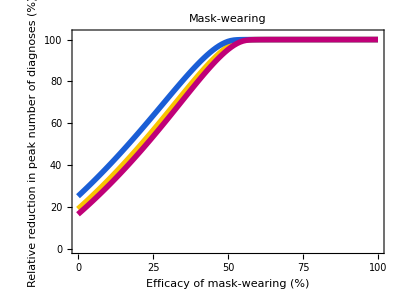

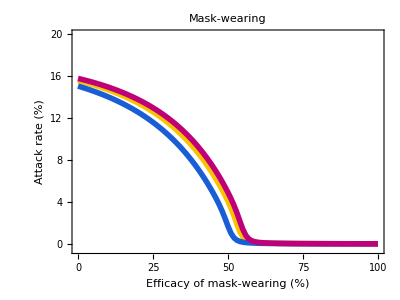

-Graphics-

```mathematica
imagePadding={{80,15},{73,7.5}};

SS1=ListLinePlot[{PeakMaskBaseline,PeakMaskMin,PeakMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,102.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of mask-wearing (%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS1",".pdf"],SS1];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS1",".eps"],SS1];

SS2=ListLinePlot[{AttackRateMaskBaseline,AttackRateMaskMin,AttackRateMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-0.5,20}},AxesOrigin->{0,0},Filling->{1->{2}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of mask-wearing (%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS2",".pdf"],SS2];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS2",".eps"],SS2];

SS3=ListLinePlot[{PeakTimingMaskBaseline,PeakTimingMaskMin,PeakTimingMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,800}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{"","","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],Graphics[{RGBColor[185/255,76/255,225/255],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of mask-wearing (%)",None}},ImagePadding->imagePadding,PlotRangePadding->None,PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],PlotLegends->LineLegend[Table[Style[Row[{label}],Black,13,"Text"],{label,{"0.5","0.25","0.75"}}],LegendLabel->Style["Relative infectivity\nof infectious\nwith mild disease",Black,13,"Text"]],FrameTicks->{{{{0,"0"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3/2,"18"}},None},{Automatic,None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS3",".pdf"],SS3];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS3",".eps"],SS3];
```

```mathematica
ReductionFactor=Table[i,{i,0,1,0.1}];

PeakGovBaseline=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakGovMin=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityMin,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakGovMax=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityMax,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovBaseline=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovMin=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityMin,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovMax=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityMax,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovBaseline=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovMin=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityMin,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovMax=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityMax,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,19.1862},{90.,19.1867},{80.,19.1876},{70.,19.1898},{60.,19.1954},{50.,19.2108},{40.,19.2514},{30.,19.3545},{20.,19.5743},{10.,19.8368},{0.,19.1837}}

{{100.,25.2764},{90.,25.2772},{80.,25.2787},{70.,25.282},{60.,25.2904},{50.,25.3115},{40.,25.3654},{30.,25.5011},{20.,25.7913},{10.,26.1403},{0.,25.272}}

{{100.,16.6591},{90.,16.6594},{80.,16.6601},{70.,16.6616},{60.,16.6658},{50.,16.6774},{40.,16.7089},{30.,16.7891},{20.,16.9598},{10.,17.1643},{0.,16.6574}}

{{100.,15.5894},{90.,15.5894},{80.,15.5894},{70.,15.5893},{60.,15.5892},{50.,15.5888},{40.,15.5878},{30.,15.5853},{20.,15.58},{10.,15.5735},{0.,15.5895}}

{{100.,15.0624},{90.,15.0624},{80.,15.0624},{70.,15.0623},{60.,15.062},{50.,15.0615},{40.,15.0599},{30.,15.0562},{20.,15.048},{10.,15.0381},{0.,15.0626}}

{{100.,15.7902},{90.,15.7902},{80.,15.7901},{70.,15.7901},{60.,15.79},{50.,15.7898},{40.,15.789},{30.,15.7872},{20.,15.7833},{10.,15.7786},{0.,15.7902}}

{{100.,366.865},{90.,327.359},{80.,299.424},{70.,277.084},{60.,258.253},{50.,240.867},{40.,223.761},{30.,207.357},{20.,191.835},{10.,177.095},{0.,162.797}}

{{100.,364.88},{90.,328.101},{80.,301.189},{70.,279.932},{60.,262.204},{50.,244.998},{40.,227.09},{30.,209.603},{20.,192.998},{10.,177.156},{0.,161.714}}

{{100.,369.191},{90.,328.582},{80.,300.246},{70.,277.465},{60.,258.133},{50.,240.626},{40.,223.821},{30.,207.838},{20.,192.717},{10.,178.379},{0.,164.542}}

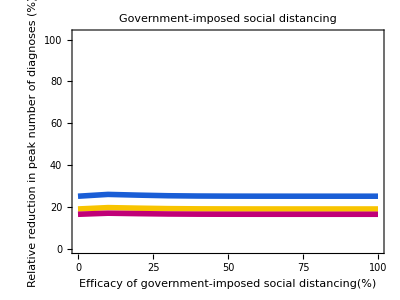

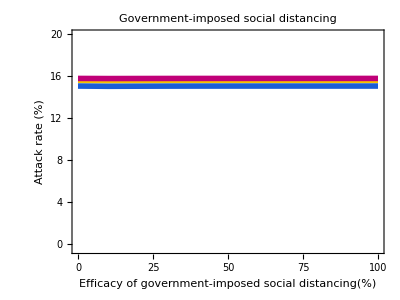

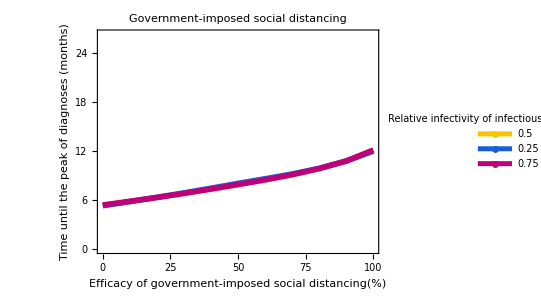

```mathematica
imagePadding={{80,15},{73,7.5}};

SS4=ListLinePlot[{PeakGovBaseline,PeakGovMin,PeakGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,102.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS4",".pdf"],SS4];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS4",".eps"],SS4];


SS5=ListLinePlot[{AttackRateGovBaseline,AttackRateGovMin,AttackRateGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-0.5,20}},AxesOrigin->{0,0},Filling->{1->{2}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS5",".pdf"],SS5];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS5",".eps"],SS5];

SS6=ListLinePlot[{PeakTimingGovBaseline,PeakTimingGovMin,PeakTimingGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,800}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{"","","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],Graphics[{RGBColor[185/255,76/255,225/255],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}},ImagePadding->imagePadding,PlotRangePadding->None,PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],PlotLegends->LineLegend[Table[Style[Row[{label}],Black,13,"Text"],{label,{"0.5","0.25","0.75"}}],LegendLabel->Style["Relative infectivity\nof infectious\nwith mild disease",Black,13,"Text"]],FrameTicks->{{{{0,"0"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3/2,"18"}},None},{Automatic,None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS6",".pdf"],SS6];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS6",".eps"],SS6];
```

```mathematica
ReductionFactor=Table[i,{i,0,1,0.01}];

PeakMaskBaseline=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakMaskMin=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsMin,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakMaskMax=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsMax,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskBaseline=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskMin=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsMin,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskMax=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsMax,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskBaseline=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskMin=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsMin,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskMax=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsMax,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,99.9897},{99.,99.9895},{98.,99.9894},{97.,99.9892},{96.,99.9891},{95.,99.9889},{94.,99.9887},{93.,99.9886},{92.,99.9884},{91.,99.9882},{90.,99.988},{89.,99.9878},{88.,99.9876},{87.,99.9874},{86.,99.9872},{85.,99.987},{84.,99.9867},{83.,99.9865},{82.,99.9862},{81.,99.986},{80.,99.9857},{79.,99.9854},{78.,99.9851},{77.,99.9847},{76.,99.9844},{75.,99.984},{74.,99.9837},{73.,99.9832},{72.,99.9828},{71.,99.9823},{70.,99.9818},{69.,99.9812},{68.,99.9806},{67.,99.9799},{66.,99.9792},{65.,99.9783},{64.,99.9772},{63.,99.9758},{62.,99.9733},{61.,99.9687},{60.,99.9621},{59.,99.9522},{58.,99.9356},{57.,99.9046},{56.,99.8396},{55.,99.6973},{54.,99.4204},{53.,98.9754},{52.,98.3611},{51.,97.5905},{50.,96.6796},{49.,95.6439},{48.,94.4978},{47.,93.2544},{46.,91.9255},{45.,90.5218},{44.,89.053},{43.,87.5278},{42.,85.9542},{41.,84.3393},{40.,82.6896},{39.,81.011},{38.,79.3088},{37.,77.5876},{36.,75.8518},{35.,74.1053},{34.,72.3514},{33.,70.5933},{32.,68.8339},{31.,67.0755},{30.,65.3205},{29.,63.5709},{28.,61.8284},{27.,60.0946},{26.,58.3709},{25.,56.6586},{24.,54.9588},{23.,53.2724},{22.,51.6003},{21.,49.9432},{20.,48.3019},{19.,46.6767},{18.,45.0683},{17.,43.4769},{16.,41.903},{15.,40.3467},{14.,38.8084},{13.,37.2881},{12.,35.7861},{11.,34.3024},{10.,32.8369},{9.,31.3899},{8.,29.9612},{7.,28.5509},{6.,27.1588},{5.,25.7848},{4.,24.4289},{3.,23.091},{2.,21.771},{1.,20.4686},{0.,19.1837}}

{{100.,99.9896},{99.,99.9894},{98.,99.9893},{97.,99.9891},{96.,99.989},{95.,99.9888},{94.,99.9887},{93.,99.9885},{92.,99.9883},{91.,99.9881},{90.,99.9879},{89.,99.9877},{88.,99.9875},{87.,99.9873},{86.,99.9871},{85.,99.9868},{84.,99.9866},{83.,99.9863},{82.,99.9861},{81.,99.9858},{80.,99.9855},{79.,99.9852},{78.,99.9848},{77.,99.9845},{76.,99.9841},{75.,99.9837},{74.,99.9833},{73.,99.9829},{72.,99.9824},{71.,99.9819},{70.,99.9813},{69.,99.9807},{68.,99.98},{67.,99.9792},{66.,99.9783},{65.,99.9772},{64.,99.9757},{63.,99.9729},{62.,99.9682},{61.,99.9617},{60.,99.9518},{59.,99.9356},{58.,99.9067},{57.,99.8492},{56.,99.7315},{55.,99.5118},{54.,99.1631},{53.,98.6821},{52.,98.0779},{51.,97.3628},{50.,96.5493},{49.,95.649},{48.,94.6724},{47.,93.629},{46.,92.5275},{45.,91.3756},{44.,90.1802},{43.,88.9476},{42.,87.6836},{41.,86.3931},{40.,85.0808},{39.,83.7508},{38.,82.4068},{37.,81.0521},{36.,79.6897},{35.,78.3224},{34.,76.9524},{33.,75.582},{32.,74.2131},{31.,72.8473},{30.,71.4862},{29.,70.1312},{28.,68.7835},{27.,67.444},{26.,66.1139},{25.,64.7938},{24.,63.4845},{23.,62.1867},{22.,60.9008},{21.,59.6274},{20.,58.3669},{19.,57.1196},{18.,55.8858},{17.,54.6658},{16.,53.4596},{15.,52.2676},{14.,51.0897},{13.,49.9261},{12.,48.7769},{11.,47.642},{10.,46.5214},{9.,45.4152},{8.,44.3232},{7.,43.2455},{6.,42.182},{5.,41.1326},{4.,40.0971},{3.,39.0755},{2.,38.0676},{1.,37.0734},{0.,36.0926}}

{{100.,99.9895},{99.,99.9894},{98.,99.9892},{97.,99.9891},{96.,99.9889},{95.,99.9887},{94.,99.9886},{93.,99.9884},{92.,99.9882},{91.,99.988},{90.,99.9878},{89.,99.9876},{88.,99.9874},{87.,99.9871},{86.,99.9869},{85.,99.9867},{84.,99.9864},{83.,99.9861},{82.,99.9859},{81.,99.9856},{80.,99.9852},{79.,99.9849},{78.,99.9846},{77.,99.9842},{76.,99.9838},{75.,99.9834},{74.,99.9829},{73.,99.9825},{72.,99.9819},{71.,99.9814},{70.,99.9807},{69.,99.98},{68.,99.9792},{67.,99.9783},{66.,99.9771},{65.,99.9756},{64.,99.9726},{63.,99.9679},{62.,99.9614},{61.,99.9518},{60.,99.9365},{59.,99.9104},{58.,99.862},{57.,99.7707},{56.,99.6092},{55.,99.3584},{54.,99.0137},{53.,98.5801},{52.,98.0662},{51.,97.4808},{50.,96.8326},{49.,96.1293},{48.,95.378},{47.,94.585},{46.,93.7559},{45.,92.896},{44.,92.0098},{43.,91.1014},{42.,90.1745},{41.,89.2325},{40.,88.2782},{39.,87.3144},{38.,86.3435},{37.,85.3675},{36.,84.3884},{35.,83.4079},{34.,82.4275},{33.,81.4486},{32.,80.4723},{31.,79.4997},{30.,78.5318},{29.,77.5695},{28.,76.6133},{27.,75.6641},{26.,74.7224},{25.,73.7886},{24.,72.8632},{23.,71.9466},{22.,71.0392},{21.,70.141},{20.,69.2525},{19.,68.3738},{18.,67.505},{17.,66.6463},{16.,65.7977},{15.,64.9594},{14.,64.1314},{13.,63.3137},{12.,62.5063},{11.,61.7092},{10.,60.9223},{9.,60.1458},{8.,59.3794},{7.,58.6232},{6.,57.877},{5.,57.1409},{4.,56.4146},{3.,55.6982},{2.,54.9915},{1.,54.2945},{0.,53.607}}

{{100.,0.0139929},{99.,0.0143083},{98.,0.0146382},{97.,0.0149835},{96.,0.0153453},{95.,0.0157249},{94.,0.0161236},{93.,0.0165428},{92.,0.0169843},{91.,0.0174499},{90.,0.0179415},{89.,0.0184615},{88.,0.0190124},{87.,0.0195969},{86.,0.0202184},{85.,0.0208804},{84.,0.0215871},{83.,0.0223432},{82.,0.0231541},{81.,0.024026},{80.,0.024966},{79.,0.0259827},{78.,0.0270857},{77.,0.0282867},{76.,0.0295994},{75.,0.0310405},{74.,0.0326297},{73.,0.0343915},{72.,0.0363557},{71.,0.0385599},{70.,0.0410512},{69.,0.0438904},{68.,0.0471564},{67.,0.0509542},{66.,0.0554265},{65.,0.0607718},{64.,0.0672748},{63.,0.0753581},{62.,0.0856753},{61.,0.09929},{60.,0.118038},{59.,0.145326},{58.,0.18798},{57.,0.260716},{56.,0.396241},{55.,0.661302},{54.,1.14896},{53.,1.87324},{52.,2.67945},{51.,3.4173},{50.,4.06489},{49.,4.65068},{48.,5.19629},{47.,5.71174},{46.,6.20132},{45.,6.66722},{44.,7.11091},{43.,7.53366},{42.,7.93661},{41.,8.32086},{40.,8.68743},{39.,9.03728},{38.,9.37132},{37.,9.6904},{36.,9.99534},{35.,10.2869},{34.,10.5658},{33.,10.8326},{32.,11.0881},{31.,11.3328},{30.,11.5672},{29.,11.7919},{28.,12.0072},{27.,12.2137},{26.,12.4119},{25.,12.602},{24.,12.7845},{23.,12.9598},{22.,13.1282},{21.,13.29},{20.,13.4455},{19.,13.595},{18.,13.7388},{17.,13.8772},{16.,14.0103},{15.,14.1385},{14.,14.2619},{13.,14.3808},{12.,14.4953},{11.,14.6056},{10.,14.7119},{9.,14.8145},{8.,14.9133},{7.,15.0087},{6.,15.1007},{5.,15.1895},{4.,15.2752},{3.,15.3579},{2.,15.4378},{1.,15.5149},{0.,15.5895}}

{{100.,0.0142608},{99.,0.0145923},{98.,0.0149394},{97.,0.0153033},{96.,0.015685},{95.,0.0160861},{94.,0.0165081},{93.,0.0169525},{92.,0.0174212},{91.,0.0179164},{90.,0.0184403},{89.,0.0189954},{88.,0.0195847},{87.,0.0202114},{86.,0.0208792},{85.,0.0215923},{84.,0.0223554},{83.,0.0231742},{82.,0.0240548},{81.,0.0250046},{80.,0.0260321},{79.,0.0271473},{78.,0.0283619},{77.,0.02969},{76.,0.0311483},{75.,0.032757},{74.,0.0345409},{73.,0.0365303},{72.,0.038763},{71.,0.0412871},{70.,0.0441637},{69.,0.0474726},{68.,0.0513196},{67.,0.0558481},{66.,0.061257},{65.,0.0678305},{64.,0.0759881},{63.,0.0863748},{62.,0.10003},{61.,0.118724},{60.,0.145685},{59.,0.187217},{58.,0.256399},{57.,0.380691},{56.,0.611234},{55.,1.00809},{54.,1.56291},{53.,2.16399},{52.,2.71904},{51.,3.21585},{50.,3.67096},{49.,4.09702},{48.,4.50009},{47.,4.88291},{46.,5.24701},{45.,5.59352},{44.,5.92344},{43.,6.23767},{42.,6.53709},{41.,6.82253},{40.,7.09475},{39.,7.3545},{38.,7.60246},{37.,7.83928},{36.,8.06557},{35.,8.28191},{34.,8.48882},{33.,8.68682},{32.,8.87634},{31.,9.05782},{30.,9.23165},{29.,9.39822},{28.,9.55789},{27.,9.711},{26.,9.85787},{25.,9.99881},{24.,10.1341},{23.,10.264},{22.,10.3888},{21.,10.5087},{20.,10.6239},{19.,10.7348},{18.,10.8413},{17.,10.9439},{16.,11.0425},{15.,11.1375},{14.,11.2289},{13.,11.317},{12.,11.4019},{11.,11.4836},{10.,11.5624},{9.,11.6384},{8.,11.7117},{7.,11.7824},{6.,11.8506},{5.,11.9164},{4.,11.9799},{3.,12.0412},{2.,12.1004},{1.,12.1576},{0.,12.2129}}

{{100.,0.0145315},{99.,0.01488},{98.,0.0152454},{97.,0.0156288},{96.,0.0160318},{95.,0.0164558},{94.,0.0169025},{93.,0.0173739},{92.,0.0178718},{91.,0.0183988},{90.,0.0189574},{89.,0.0195505},{88.,0.0201814},{87.,0.0208539},{86.,0.0215722},{85.,0.0223411},{84.,0.0231662},{83.,0.0240538},{82.,0.0250115},{81.,0.0260477},{80.,0.0271726},{79.,0.028398},{78.,0.0297381},{77.,0.0312098},{76.,0.0328335},{75.,0.034634},{74.,0.0366419},{73.,0.0388952},{72.,0.0414419},{71.,0.0443432},{70.,0.0476788},{69.,0.0515538},{68.,0.0561102},{67.,0.0615438},{66.,0.0681328},{65.,0.0762843},{64.,0.0866175},{63.,0.100115},{62.,0.118419},{61.,0.144435},{60.,0.183615},{59.,0.24661},{58.,0.353873},{57.,0.538521},{56.,0.83019},{55.,1.21112},{54.,1.61495},{53.,1.99424},{52.,2.342},{51.,2.66525},{50.,2.96974},{49.,3.25839},{48.,3.53267},{47.,3.7935},{46.,4.04164},{45.,4.27777},{44.,4.50255},{43.,4.71661},{42.,4.92055},{41.,5.11494},{40.,5.30031},{39.,5.47718},{38.,5.646},{37.,5.80725},{36.,5.96133},{35.,6.10865},{34.,6.24955},{33.,6.38437},{32.,6.5134},{31.,6.63694},{30.,6.75527},{29.,6.86864},{28.,6.97731},{27.,7.08151},{26.,7.18146},{25.,7.27737},{24.,7.36943},{23.,7.45783},{22.,7.54274},{21.,7.62432},{20.,7.70274},{19.,7.77814},{18.,7.85065},{17.,7.92042},{16.,7.98755},{15.,8.05218},{14.,8.1144},{13.,8.17433},{12.,8.23207},{11.,8.28771},{10.,8.34134},{9.,8.39304},{8.,8.44291},{7.,8.49101},{6.,8.53741},{5.,8.58219},{4.,8.62542},{3.,8.66715},{2.,8.70745},{1.,8.74638},{0.,8.78398}}

{{100.,71.893},{99.,72.0936},{98.,72.3142},{97.,72.5348},{96.,72.7553},{95.,72.996},{94.,73.2366},{93.,73.4773},{92.,73.738},{91.,73.9987},{90.,74.2794},{89.,74.5802},{88.,74.8811},{87.,75.1819},{86.,75.5228},{85.,75.8637},{84.,76.2247},{83.,76.6057},{82.,77.0068},{81.,77.4479},{80.,77.8891},{79.,78.3905},{78.,78.8918},{77.,79.4533},{76.,80.075},{75.,80.7167},{74.,81.4587},{73.,82.2609},{72.,83.1432},{71.,84.166},{70.,85.3291},{69.,86.7128},{68.,88.3572},{67.,90.4027},{66.,93.0699},{65.,96.7798},{64.,102.676},{63.,115.129},{62.,266.155},{61.,367.647},{60.,439.801},{59.,513.178},{58.,593.814},{57.,679.344},{56.,751.137},{55.,773.376},{54.,737.46},{53.,675.855},{52.,614.289},{51.,560.866},{50.,516.166},{49.,478.886},{48.,447.542},{47.,420.93},{46.,398.089},{45.,378.276},{44.,360.909},{43.,345.588},{42.,331.931},{41.,319.698},{40.,308.669},{39.,298.682},{38.,289.557},{37.,281.215},{36.,273.554},{35.,266.475},{34.,259.938},{33.,253.842},{32.,248.166},{31.,242.872},{30.,237.919},{29.,233.266},{28.,228.875},{27.,224.743},{26.,220.853},{25.,217.163},{24.,213.654},{23.,210.325},{22.,207.176},{21.,204.168},{20.,201.3},{19.,198.573},{18.,195.946},{17.,193.439},{16.,191.053},{15.,188.747},{14.,186.541},{13.,184.415},{12.,182.37},{11.,180.404},{10.,178.519},{9.,176.694},{8.,174.93},{7.,173.245},{6.,171.601},{5.,170.016},{4.,168.472},{3.,166.988},{2.,165.544},{1.,164.141},{0.,162.797}}

{{100.,74.7808},{99.,75.0014},{98.,75.222},{97.,75.4426},{96.,75.6832},{95.,75.9239},{94.,76.1645},{93.,76.4453},{92.,76.706},{91.,76.9867},{90.,77.2875},{89.,77.5883},{88.,77.9092},{87.,78.23},{86.,78.591},{85.,78.952},{84.,79.333},{83.,79.7541},{82.,80.1753},{81.,80.6365},{80.,81.1378},{79.,81.6592},{78.,82.2408},{77.,82.8424},{76.,83.5243},{75.,84.2662},{74.,85.0885},{73.,86.0109},{72.,87.0537},{71.,88.257},{70.,89.6808},{69.,91.3854},{68.,93.5311},{67.,96.3587},{66.,100.39},{65.,106.967},{64.,122.369},{63.,276.362},{62.,358.904},{61.,423.056},{60.,488.01},{59.,557.778},{58.,629.691},{57.,689.21},{56.,710.849},{55.,686.383},{54.,637.391},{53.,584.991},{52.,537.764},{51.,497.315},{50.,463.083},{49.,434.025},{48.,409.179},{47.,387.741},{46.,369.051},{45.,352.647},{44.,338.128},{43.,325.173},{42.,313.542},{41.,303.034},{40.,293.488},{39.,284.785},{38.,276.823},{37.,269.484},{36.,262.705},{35.,256.428},{34.,250.593},{33.,245.138},{32.,240.065},{31.,235.292},{30.,230.82},{29.,226.608},{28.,222.638},{27.,218.888},{26.,215.318},{25.,211.949},{24.,208.761},{23.,205.712},{22.,202.805},{21.,200.037},{20.,197.41},{19.,194.883},{18.,192.457},{17.,190.151},{16.,187.925},{15.,185.799},{14.,183.733},{13.,181.768},{12.,179.863},{11.,178.038},{10.,176.273},{9.,174.569},{8.,172.924},{7.,171.34},{6.,169.796},{5.,168.312},{4.,166.888},{3.,165.484},{2.,164.141},{1.,162.817},{0.,161.554}}

{{100.,78.5308},{99.,78.7514},{98.,78.972},{97.,79.2127},{96.,79.4533},{95.,79.714},{94.,79.9747},{93.,80.2555},{92.,80.5362},{91.,80.817},{90.,81.1378},{89.,81.4587},{88.,81.7996},{87.,82.1405},{86.,82.5216},{85.,82.9026},{84.,83.3237},{83.,83.7649},{82.,84.2261},{81.,84.7275},{80.,85.2689},{79.,85.8505},{78.,86.4722},{77.,87.154},{76.,87.916},{75.,88.7583},{74.,89.7008},{73.,90.7637},{72.,92.007},{71.,93.491},{70.,95.2758},{69.,97.5218},{68.,100.51},{67.,104.841},{66.,112.161},{65.,131.553},{64.,274.357},{63.,343.282},{62.,398.951},{61.,454.36},{60.,512.095},{59.,569.489},{58.,616.315},{57.,636.288},{56.,622.792},{55.,587.798},{54.,546.588},{53.,507.242},{52.,472.368},{51.,442.167},{50.,416.137},{49.,393.637},{48.,374.064},{47.,356.918},{46.,341.778},{45.,328.301},{44.,316.249},{43.,305.42},{42.,295.594},{41.,286.67},{40.,278.508},{39.,271.008},{38.,264.109},{37.,257.732},{36.,251.796},{35.,246.301},{34.,241.147},{33.,236.355},{32.,231.842},{31.,227.591},{30.,223.6},{29.,219.83},{28.,216.281},{27.,212.892},{26.,209.703},{25.,206.655},{24.,203.767},{23.,201.},{22.,198.373},{21.,195.846},{20.,193.439},{19.,191.133},{18.,188.927},{17.,186.822},{16.,184.776},{15.,182.831},{14.,180.946},{13.,179.121},{12.,177.376},{11.,175.692},{10.,174.067},{9.,172.483},{8.,170.979},{7.,169.495},{6.,168.071},{5.,166.708},{4.,165.364},{3.,164.06},{2.,162.817},{1.,161.594},{0.,160.411}}

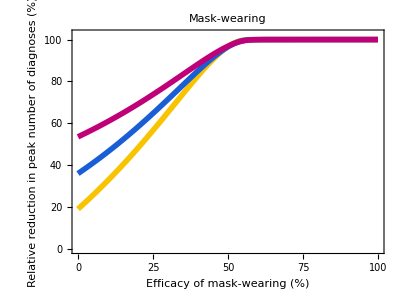

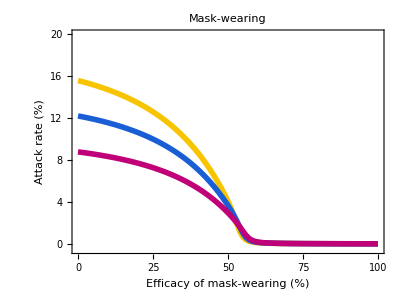

-Graphics-

```mathematica
imagePadding={{80,15},{73,7.5}};

SS7=ListLinePlot[{PeakMaskBaseline,PeakMaskMin,PeakMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,102.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of mask-wearing (%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS7",".pdf"],SS7];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS7",".eps"],SS7];

SS8=ListLinePlot[{AttackRateMaskBaseline,AttackRateMaskMin,AttackRateMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-0.5,20}},AxesOrigin->{0,0},Filling->{1->{2}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of mask-wearing (%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS8",".pdf"],SS8];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS8",".eps"],SS8];

SS9=ListLinePlot[{PeakTimingMaskBaseline,PeakTimingMaskMin,PeakTimingMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,800}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{"","","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],Graphics[{RGBColor[185/255,76/255,225/255],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of mask-wearing (%)",None}},ImagePadding->imagePadding,PlotRangePadding->None,PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],PlotLegends->LineLegend[Table[Style[Row[{label}],Black,13,"Text"],{label,{"0.82","0.86","0.9"}}],LegendLabel->Style["Proportion of infectious\nwith mild disease",Black,13,"Text"]],FrameTicks->{{{{0,"0"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3/2,"18"}},None},{Automatic,None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS9",".pdf"],SS9];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS9",".eps"],SS9];
```

```mathematica
ReductionFactor=Table[i,{i,0,1,0.1}];

PeakGovBaseline=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakGovMin=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsMin,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakGovMax=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsMax,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovBaseline=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovMin=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsMin,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovMax=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsMax,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovBaseline=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovMin=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsMin,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovMax=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsMax,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,19.1862},{90.,19.1867},{80.,19.1876},{70.,19.1898},{60.,19.1954},{50.,19.2108},{40.,19.2514},{30.,19.3545},{20.,19.5743},{10.,19.8368},{0.,19.1837}}

{{100.,36.0945},{90.,36.0949},{80.,36.0956},{70.,36.0973},{60.,36.1018},{50.,36.1143},{40.,36.1479},{30.,36.2332},{20.,36.4146},{10.,36.6292},{0.,36.0926}}

{{100.,53.6083},{90.,53.6085},{80.,53.609},{70.,53.6102},{60.,53.6135},{50.,53.6227},{40.,53.648},{30.,53.7123},{20.,53.8488},{10.,54.0088},{0.,53.6069}}

{{100.,15.5894},{90.,15.5894},{80.,15.5894},{70.,15.5893},{60.,15.5892},{50.,15.5888},{40.,15.5878},{30.,15.5853},{20.,15.58},{10.,15.5735},{0.,15.5895}}

{{100.,12.2128},{90.,12.2128},{80.,12.2128},{70.,12.2127},{60.,12.2126},{50.,12.2124},{40.,12.2116},{30.,12.2096},{20.,12.2054},{10.,12.2004},{0.,12.2129}}

{{100.,8.78395},{90.,8.78394},{80.,8.78393},{70.,8.78391},{60.,8.78383},{50.,8.78363},{40.,8.78308},{30.,8.78166},{20.,8.77864},{10.,8.77505},{0.,8.78398}}

{{100.,366.865},{90.,327.359},{80.,299.424},{70.,277.084},{60.,258.253},{50.,240.867},{40.,223.761},{30.,207.357},{20.,191.835},{10.,177.095},{0.,162.797}}

{{100.,366.043},{90.,325.694},{80.,297.459},{70.,274.778},{60.,255.566},{50.,238.099},{40.,221.234},{30.,205.151},{20.,189.97},{10.,175.531},{0.,161.554}}

{{100.,365.421},{90.,324.251},{80.,295.734},{70.,272.712},{60.,253.12},{50.,235.532},{40.,218.888},{30.,203.105},{20.,188.225},{10.,174.087},{0.,160.411}}

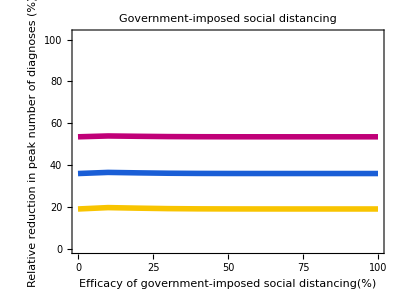

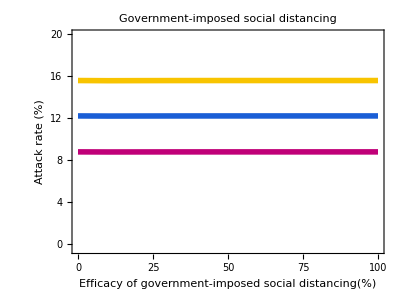

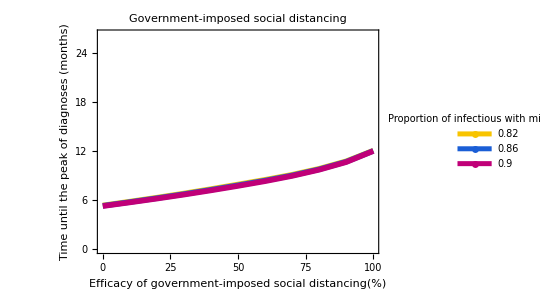

```mathematica
imagePadding={{80,15},{73,7.5}};

SS10=ListLinePlot[{PeakGovBaseline,PeakGovMin,PeakGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,102.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS10",".pdf"],SS10];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS10",".eps"],SS10];


SS11=ListLinePlot[{AttackRateGovBaseline,AttackRateGovMin,AttackRateGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-0.5,20}},AxesOrigin->{0,0},Filling->{1->{2}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS11",".pdf"],SS11];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS11",".eps"],SS11];

SS12=ListLinePlot[{PeakTimingGovBaseline,PeakTimingGovMin,PeakTimingGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,800}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{"","","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],Graphics[{RGBColor[185/255,76/255,225/255],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}},ImagePadding->imagePadding,PlotRangePadding->None,PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],PlotLegends->LineLegend[Table[Style[Row[{label}],Black,13,"Text"],{label,{"0.82","0.86","0.9"}}],LegendLabel->Style["Proportion of infectious\nwith mild disease",Black,13,"Text"]],FrameTicks->{{{{0,"0"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3/2,"18"}},None},{Automatic,None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS12",".pdf"],SS12];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS12",".eps"],SS12];
```

```mathematica
ReductionFactor=Table[i,{i,0,1,0.01}];

PeakMaskBaseline=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakMaskMin=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsMin,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakMaskMax=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsMax,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskBaseline=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskMin=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsMin,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskMax=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsMax,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskBaseline=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskMin=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsMin,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskMax=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsMax,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,99.9897},{99.,99.9895},{98.,99.9894},{97.,99.9892},{96.,99.9891},{95.,99.9889},{94.,99.9887},{93.,99.9886},{92.,99.9884},{91.,99.9882},{90.,99.988},{89.,99.9878},{88.,99.9876},{87.,99.9874},{86.,99.9872},{85.,99.987},{84.,99.9867},{83.,99.9865},{82.,99.9862},{81.,99.986},{80.,99.9857},{79.,99.9854},{78.,99.9851},{77.,99.9847},{76.,99.9844},{75.,99.984},{74.,99.9837},{73.,99.9832},{72.,99.9828},{71.,99.9823},{70.,99.9818},{69.,99.9812},{68.,99.9806},{67.,99.9799},{66.,99.9792},{65.,99.9783},{64.,99.9772},{63.,99.9758},{62.,99.9733},{61.,99.9687},{60.,99.9621},{59.,99.9522},{58.,99.9356},{57.,99.9046},{56.,99.8396},{55.,99.6973},{54.,99.4204},{53.,98.9754},{52.,98.3611},{51.,97.5905},{50.,96.6796},{49.,95.6439},{48.,94.4978},{47.,93.2544},{46.,91.9255},{45.,90.5218},{44.,89.053},{43.,87.5278},{42.,85.9542},{41.,84.3393},{40.,82.6896},{39.,81.011},{38.,79.3088},{37.,77.5876},{36.,75.8518},{35.,74.1053},{34.,72.3514},{33.,70.5933},{32.,68.8339},{31.,67.0755},{30.,65.3205},{29.,63.5709},{28.,61.8284},{27.,60.0946},{26.,58.3709},{25.,56.6586},{24.,54.9588},{23.,53.2724},{22.,51.6003},{21.,49.9432},{20.,48.3019},{19.,46.6767},{18.,45.0683},{17.,43.4769},{16.,41.903},{15.,40.3467},{14.,38.8084},{13.,37.2881},{12.,35.7861},{11.,34.3024},{10.,32.8369},{9.,31.3899},{8.,29.9612},{7.,28.5509},{6.,27.1588},{5.,25.7848},{4.,24.4289},{3.,23.091},{2.,21.771},{1.,20.4686},{0.,19.1837}}

{{100.,99.9913},{99.,99.9912},{98.,99.991},{97.,99.9909},{96.,99.9908},{95.,99.9906},{94.,99.9905},{93.,99.9904},{92.,99.9902},{91.,99.9901},{90.,99.9899},{89.,99.9897},{88.,99.9896},{87.,99.9894},{86.,99.9892},{85.,99.989},{84.,99.9888},{83.,99.9886},{82.,99.9884},{81.,99.9881},{80.,99.9879},{79.,99.9876},{78.,99.9874},{77.,99.9871},{76.,99.9868},{75.,99.9864},{74.,99.9861},{73.,99.9857},{72.,99.9853},{71.,99.9849},{70.,99.9844},{69.,99.9839},{68.,99.9833},{67.,99.9825},{66.,99.9815},{65.,99.9795},{64.,99.9769},{63.,99.9736},{62.,99.9692},{61.,99.9629},{60.,99.9536},{59.,99.9385},{58.,99.9116},{57.,99.8577},{56.,99.7444},{55.,99.524},{54.,99.162},{53.,98.652},{52.,98.0031},{51.,97.2286},{50.,96.3422},{49.,95.3563},{48.,94.2823},{47.,93.1305},{46.,91.9103},{45.,90.6299},{44.,89.2971},{43.,87.9186},{42.,86.5006},{41.,85.0489},{40.,83.5683},{39.,82.0636},{38.,80.5389},{37.,78.9979},{36.,77.4441},{35.,75.8804},{34.,74.3097},{33.,72.7344},{32.,71.1569},{31.,69.579},{30.,68.0027},{29.,66.4297},{28.,64.8613},{27.,63.2989},{26.,61.7437},{25.,60.1967},{24.,58.659},{23.,57.1312},{22.,55.6143},{21.,54.1087},{20.,52.6152},{19.,51.1342},{18.,49.6662},{17.,48.2115},{16.,46.7705},{15.,45.3435},{14.,43.9307},{13.,42.5322},{12.,41.1483},{11.,39.7791},{10.,38.4247},{9.,37.0851},{8.,35.7604},{7.,34.4506},{6.,33.1557},{5.,31.8757},{4.,30.6105},{3.,29.3602},{2.,28.1245},{1.,26.9036},{0.,25.6972}}

{{100.,99.9875},{99.,99.9873},{98.,99.9871},{97.,99.9869},{96.,99.9867},{95.,99.9866},{94.,99.9864},{93.,99.9862},{92.,99.9859},{91.,99.9857},{90.,99.9855},{89.,99.9853},{88.,99.985},{87.,99.9848},{86.,99.9845},{85.,99.9842},{84.,99.984},{83.,99.9837},{82.,99.9834},{81.,99.9831},{80.,99.9827},{79.,99.9824},{78.,99.982},{77.,99.9816},{76.,99.9812},{75.,99.9808},{74.,99.9804},{73.,99.9799},{72.,99.9794},{71.,99.9788},{70.,99.9783},{69.,99.9776},{68.,99.977},{67.,99.9763},{66.,99.9755},{65.,99.9746},{64.,99.9736},{63.,99.9725},{62.,99.9711},{61.,99.9696},{60.,99.9676},{59.,99.9647},{58.,99.9572},{57.,99.9438},{56.,99.9192},{55.,99.8677},{54.,99.7488},{53.,99.4942},{52.,99.0508},{51.,98.409},{50.,97.5817},{49.,96.5876},{48.,95.4451},{47.,94.1714},{46.,92.7825},{45.,91.2927},{44.,89.7151},{43.,88.0616},{42.,86.3428},{41.,84.5685},{40.,82.7474},{39.,80.8876},{38.,78.996},{37.,77.0791},{36.,75.1428},{35.,73.192},{34.,71.2315},{33.,69.2654},{32.,67.2974},{31.,65.3308},{30.,63.3685},{29.,61.4131},{28.,59.4669},{27.,57.532},{26.,55.6101},{25.,53.7029},{24.,51.8117},{23.,49.9376},{22.,48.0818},{21.,46.2452},{20.,44.4284},{19.,42.6321},{18.,40.8569},{17.,39.1033},{16.,37.3715},{15.,35.6618},{14.,33.9745},{13.,32.3098},{12.,30.6676},{11.,29.0481},{10.,27.4513},{9.,25.877},{8.,24.3254},{7.,22.7961},{6.,21.2892},{5.,19.8045},{4.,18.3417},{3.,16.9008},{2.,15.4814},{1.,14.0834},{0.,12.7065}}

{{100.,0.0139929},{99.,0.0143083},{98.,0.0146382},{97.,0.0149835},{96.,0.0153453},{95.,0.0157249},{94.,0.0161236},{93.,0.0165428},{92.,0.0169843},{91.,0.0174499},{90.,0.0179415},{89.,0.0184615},{88.,0.0190124},{87.,0.0195969},{86.,0.0202184},{85.,0.0208804},{84.,0.0215871},{83.,0.0223432},{82.,0.0231541},{81.,0.024026},{80.,0.024966},{79.,0.0259827},{78.,0.0270857},{77.,0.0282867},{76.,0.0295994},{75.,0.0310405},{74.,0.0326297},{73.,0.0343915},{72.,0.0363557},{71.,0.0385599},{70.,0.0410512},{69.,0.0438904},{68.,0.0471564},{67.,0.0509542},{66.,0.0554265},{65.,0.0607718},{64.,0.0672748},{63.,0.0753581},{62.,0.0856753},{61.,0.09929},{60.,0.118038},{59.,0.145326},{58.,0.18798},{57.,0.260716},{56.,0.396241},{55.,0.661302},{54.,1.14896},{53.,1.87324},{52.,2.67945},{51.,3.4173},{50.,4.06489},{49.,4.65068},{48.,5.19629},{47.,5.71174},{46.,6.20132},{45.,6.66722},{44.,7.11091},{43.,7.53366},{42.,7.93661},{41.,8.32086},{40.,8.68743},{39.,9.03728},{38.,9.37132},{37.,9.6904},{36.,9.99534},{35.,10.2869},{34.,10.5658},{33.,10.8326},{32.,11.0881},{31.,11.3328},{30.,11.5672},{29.,11.7919},{28.,12.0072},{27.,12.2137},{26.,12.4119},{25.,12.602},{24.,12.7845},{23.,12.9598},{22.,13.1282},{21.,13.29},{20.,13.4455},{19.,13.595},{18.,13.7388},{17.,13.8772},{16.,14.0103},{15.,14.1385},{14.,14.2619},{13.,14.3808},{12.,14.4953},{11.,14.6056},{10.,14.7119},{9.,14.8145},{8.,14.9133},{7.,15.0087},{6.,15.1007},{5.,15.1895},{4.,15.2752},{3.,15.3579},{2.,15.4378},{1.,15.5149},{0.,15.5895}}

{{100.,0.0140259},{99.,0.0143494},{98.,0.0146881},{97.,0.0150429},{96.,0.0154151},{95.,0.015806},{94.,0.0162171},{93.,0.0166499},{92.,0.0171061},{91.,0.0175879},{90.,0.0180974},{89.,0.0186369},{88.,0.0192094},{87.,0.0198179},{86.,0.0204659},{85.,0.0211574},{84.,0.021897},{83.,0.0226899},{82.,0.023542},{81.,0.0244604},{80.,0.025453},{79.,0.0265293},{78.,0.0277005},{77.,0.0289796},{76.,0.0303825},{75.,0.0319281},{74.,0.0336395},{73.,0.0355452},{72.,0.0376805},{71.,0.0400897},{70.,0.0428295},{69.,0.0459736},{68.,0.049619},{67.,0.0538967},{66.,0.0589873},{65.,0.0651471},{64.,0.0727516},{63.,0.0823717},{62.,0.0949153},{61.,0.111904},{60.,0.13604},{59.,0.172443},{58.,0.231389},{57.,0.334237},{56.,0.524232},{55.,0.875706},{54.,1.46484},{53.,2.26715},{52.,3.12277},{51.,3.895},{50.,4.56092},{49.,5.14943},{48.,5.68759},{47.,6.19053},{46.,6.66558},{45.,7.1164},{44.,7.54511},{43.,7.95323},{42.,8.34202},{41.,8.7126},{40.,9.06599},{39.,9.40316},{38.,9.725},{37.,10.0324},{36.,10.326},{35.,10.6068},{34.,10.8752},{33.,11.132},{32.,11.3779},{31.,11.6133},{30.,11.8387},{29.,12.0548},{28.,12.2619},{27.,12.4604},{26.,12.6509},{25.,12.8337},{24.,13.0092},{23.,13.1776},{22.,13.3395},{21.,13.4949},{20.,13.6444},{19.,13.7881},{18.,13.9262},{17.,14.0592},{16.,14.1871},{15.,14.3102},{14.,14.4287},{13.,14.5429},{12.,14.6528},{11.,14.7588},{10.,14.8609},{9.,14.9594},{8.,15.0543},{7.,15.1458},{6.,15.2342},{5.,15.3194},{4.,15.4016},{3.,15.481},{2.,15.5577},{1.,15.6317},{0.,15.7032}}

{{100.,0.013861},{99.,0.0141608},{98.,0.0144737},{97.,0.0148007},{96.,0.0151428},{95.,0.0155011},{94.,0.0158768},{93.,0.0162711},{92.,0.0166855},{91.,0.0171215},{90.,0.0175809},{89.,0.0180657},{88.,0.0185781},{87.,0.0191204},{86.,0.0196954},{85.,0.0203061},{84.,0.0209561},{83.,0.0216492},{82.,0.02239},{81.,0.0231836},{80.,0.0240358},{79.,0.0249535},{78.,0.0259446},{77.,0.0270184},{76.,0.0281857},{75.,0.0294596},{74.,0.0308555},{73.,0.032392},{72.,0.0340918},{71.,0.0359827},{70.,0.0380993},{69.,0.0404852},{68.,0.0431961},{67.,0.0463043},{66.,0.0499053},{65.,0.054128},{64.,0.0591511},{63.,0.0652288},{62.,0.0727354},{61.,0.0822455},{60.,0.0946849},{59.,0.11164},{58.,0.13604},{57.,0.173807},{56.,0.238139},{55.,0.360424},{54.,0.610509},{53.,1.08804},{52.,1.78415},{51.,2.52048},{50.,3.18924},{49.,3.79752},{48.,4.36692},{47.,4.90729},{46.,5.42212},{45.,5.913},{44.,6.3811},{43.,6.82755},{42.,7.25344},{41.,7.65986},{40.,8.04781},{39.,8.41828},{38.,8.77218},{37.,9.11038},{36.,9.43371},{35.,9.74294},{34.,10.0388},{33.,10.322},{32.,10.5933},{31.,10.8531},{30.,11.1022},{29.,11.341},{28.,11.5699},{27.,11.7896},{26.,12.0003},{25.,12.2026},{24.,12.3968},{23.,12.5834},{22.,12.7626},{21.,12.9349},{20.,13.1005},{19.,13.2598},{18.,13.413},{17.,13.5604},{16.,13.7023},{15.,13.8389},{14.,13.9704},{13.,14.0972},{12.,14.2193},{11.,14.3369},{10.,14.4504},{9.,14.5598},{8.,14.6653},{7.,14.7671},{6.,14.8653},{5.,14.9601},{4.,15.0517},{3.,15.1401},{2.,15.2254},{1.,15.3079},{0.,15.3875}}

{{100.,71.893},{99.,72.0936},{98.,72.3142},{97.,72.5348},{96.,72.7553},{95.,72.996},{94.,73.2366},{93.,73.4773},{92.,73.738},{91.,73.9987},{90.,74.2794},{89.,74.5802},{88.,74.8811},{87.,75.1819},{86.,75.5228},{85.,75.8637},{84.,76.2247},{83.,76.6057},{82.,77.0068},{81.,77.4479},{80.,77.8891},{79.,78.3905},{78.,78.8918},{77.,79.4533},{76.,80.075},{75.,80.7167},{74.,81.4587},{73.,82.2609},{72.,83.1432},{71.,84.166},{70.,85.3291},{69.,86.7128},{68.,88.3572},{67.,90.4027},{66.,93.0699},{65.,96.7798},{64.,102.676},{63.,115.129},{62.,266.155},{61.,367.647},{60.,439.801},{59.,513.178},{58.,593.814},{57.,679.344},{56.,751.137},{55.,773.376},{54.,737.46},{53.,675.855},{52.,614.289},{51.,560.866},{50.,516.166},{49.,478.886},{48.,447.542},{47.,420.93},{46.,398.089},{45.,378.276},{44.,360.909},{43.,345.588},{42.,331.931},{41.,319.698},{40.,308.669},{39.,298.682},{38.,289.557},{37.,281.215},{36.,273.554},{35.,266.475},{34.,259.938},{33.,253.842},{32.,248.166},{31.,242.872},{30.,237.919},{29.,233.266},{28.,228.875},{27.,224.743},{26.,220.853},{25.,217.163},{24.,213.654},{23.,210.325},{22.,207.176},{21.,204.168},{20.,201.3},{19.,198.573},{18.,195.946},{17.,193.439},{16.,191.053},{15.,188.747},{14.,186.541},{13.,184.415},{12.,182.37},{11.,180.404},{10.,178.519},{9.,176.694},{8.,174.93},{7.,173.245},{6.,171.601},{5.,170.016},{4.,168.472},{3.,166.988},{2.,165.544},{1.,164.141},{0.,162.797}}

{{100.,81.5389},{99.,81.7996},{98.,82.0403},{97.,82.301},{96.,82.5817},{95.,82.8424},{94.,83.1432},{93.,83.444},{92.,83.7448},{91.,84.0657},{90.,84.4066},{89.,84.7475},{88.,85.1286},{87.,85.5096},{86.,85.9107},{85.,86.3318},{84.,86.773},{83.,87.2543},{82.,87.7556},{81.,88.2971},{80.,88.8786},{79.,89.5204},{78.,90.2022},{77.,90.9442},{76.,91.7664},{75.,92.6889},{74.,93.7116},{73.,94.8948},{72.,96.2986},{71.,97.963},{70.,100.049},{69.,102.796},{68.,106.807},{67.,113.886},{66.,150.725},{65.,323.87},{64.,380.08},{63.,430.837},{62.,483.719},{61.,542.276},{60.,609.135},{59.,685.681},{58.,768.764},{57.,842.241},{56.,873.084},{55.,844.427},{54.,781.639},{53.,713.857},{52.,652.993},{51.,601.214},{50.,557.677},{49.,520.919},{48.,489.635},{47.,462.722},{46.,439.34},{45.,418.865},{44.,400.776},{43.,384.673},{42.,370.234},{41.,357.239},{40.,345.427},{39.,334.699},{38.,324.852},{37.,315.808},{36.,307.486},{35.,299.765},{34.,292.586},{33.,285.908},{32.,279.691},{31.,273.855},{30.,268.361},{29.,263.227},{28.,258.354},{27.,253.781},{26.,249.43},{25.,245.339},{24.,241.428},{23.,237.718},{22.,234.189},{21.,230.82},{20.,227.611},{19.,224.543},{18.,221.615},{17.,218.807},{16.,216.1},{15.,213.513},{14.,211.027},{13.,208.64},{12.,206.354},{11.,204.128},{10.,202.002},{9.,199.937},{8.,197.951},{7.,196.026},{6.,194.181},{5.,192.377},{4.,190.652},{3.,188.967},{2.,187.323},{1.,185.759},{0.,184.215}}

{{100.,62.568},{99.,62.7485},{98.,62.929},{97.,63.1094},{96.,63.2899},{95.,63.4905},{94.,63.691},{93.,63.8915},{92.,64.1121},{91.,64.3327},{90.,64.5734},{89.,64.814},{88.,65.0547},{87.,65.3154},{86.,65.5761},{85.,65.8568},{84.,66.1576},{83.,66.4584},{82.,66.7793},{81.,67.1202},{80.,67.4812},{79.,67.8622},{78.,68.2633},{77.,68.6844},{76.,69.1457},{75.,69.6269},{74.,70.1684},{73.,70.75},{72.,71.3716},{71.,72.0535},{70.,72.8155},{69.,73.6778},{68.,74.6404},{67.,75.7634},{66.,77.0469},{65.,78.591},{64.,80.4961},{63.,82.8825},{62.,86.1112},{61.,90.8239},{60.,98.9657},{59.,124.695},{58.,339.792},{57.,443.27},{56.,538.245},{55.,625.519},{54.,673.408},{53.,657.064},{52.,603.821},{51.,546.307},{50.,496.052},{49.,454.32},{48.,419.867},{47.,391.21},{46.,367.066},{45.,346.49},{44.,328.763},{43.,313.301},{42.,299.705},{41.,287.652},{40.,276.883},{39.,267.217},{38.,258.454},{37.,250.493},{36.,243.213},{35.,236.555},{34.,230.399},{33.,224.703},{32.,219.429},{31.,214.536},{30.,209.944},{29.,205.652},{28.,201.641},{27.,197.851},{26.,194.302},{25.,190.933},{24.,187.744},{23.,184.736},{22.,181.888},{21.,179.161},{20.,176.574},{19.,174.128},{18.,171.761},{17.,169.515},{16.,167.369},{15.,165.304},{14.,163.339},{13.,161.453},{12.,159.629},{11.,157.884},{10.,156.199},{9.,154.575},{8.,153.011},{7.,151.507},{6.,150.043},{5.,148.639},{4.,147.275},{3.,145.972},{2.,144.688},{1.,143.465},{0.,142.262}}

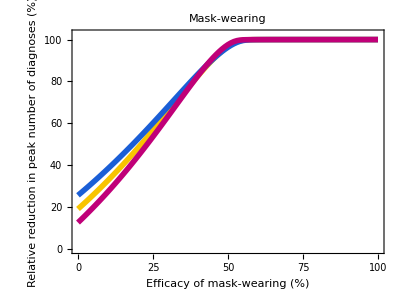

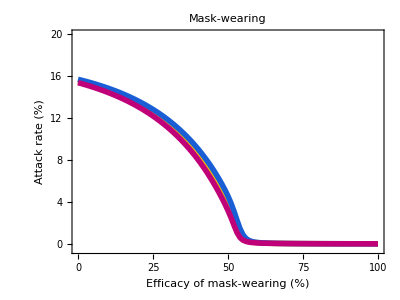

-Graphics-

```mathematica
imagePadding={{80,15},{73,7.5}};

SS13=ListLinePlot[{PeakMaskBaseline,PeakMaskMin,PeakMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,102.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of mask-wearing (%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS13",".pdf"],SS13];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS13",".eps"],SS13];

SS14=ListLinePlot[{AttackRateMaskBaseline,AttackRateMaskMin,AttackRateMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-0.5,20}},AxesOrigin->{0,0},Filling->{1->{2}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of mask-wearing (%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS14",".pdf"],SS14];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS14",".eps"],SS14];

SS15=ListLinePlot[{PeakTimingMaskBaseline,PeakTimingMaskMin,PeakTimingMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,365 5/2+20}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{"","","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],Graphics[{RGBColor[185/255,76/255,225/255],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of mask-wearing (%)",None}},ImagePadding->imagePadding,PlotRangePadding->None,PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],PlotLegends->LineLegend[Table[Style[Row[{label}],Black,13,"Text"],{label,{"7 days","9 days","5 days"}}],LegendLabel->Style["Recovery period\nof infectious\nwith mild disease",Black,13,"Text"]],FrameTicks->{{{{0,"0"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3/2,"18"},{365 5/2,"30"}},None},{Automatic,None}}]
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS15",".pdf"],SS15];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS15",".eps"],SS15];
```

```mathematica
ReductionFactor=Table[i,{i,0,1,0.05}];

PeakGovBaseline=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakGovMin=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsMin,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakGovMax=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsMax,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovBaseline=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovMin=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsMin,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovMax=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsMax,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovBaseline=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovMin=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsMin,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovMax=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsMax,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,19.1862},{95.,19.1864},{90.,19.1867},{85.,19.1871},{80.,19.1876},{75.,19.1885},{70.,19.1898},{65.,19.1919},{60.,19.1954},{55.,19.2013},{50.,19.2108},{45.,19.2263},{40.,19.2514},{35.,19.2918},{30.,19.3545},{25.,19.4475},{20.,19.5743},{15.,19.7226},{10.,19.8368},{5.,19.7664},{0.,19.1837}}

{{100.,25.6984},{95.,25.6985},{90.,25.6986},{85.,25.6988},{80.,25.6991},{75.,25.6994},{70.,25.7},{65.,25.701},{60.,25.7024},{55.,25.7047},{50.,25.7081},{45.,25.7133},{40.,25.7209},{35.,25.7319},{30.,25.7474},{25.,25.7679},{20.,25.7931},{15.,25.8191},{10.,25.8343},{5.,25.8123},{0.,25.6972}}

{{100.,12.7126},{95.,12.7131},{90.,12.7138},{85.,12.7146},{80.,12.7159},{75.,12.7178},{70.,12.7208},{65.,12.7259},{60.,12.7348},{55.,12.7505},{50.,12.779},{45.,12.8315},{40.,12.929},{35.,13.1071},{30.,13.4213},{25.,13.9444},{20.,14.7345},{15.,15.7258},{10.,16.4882},{5.,15.9513},{0.,12.7065}}

{{100.,15.5894},{95.,15.5894},{90.,15.5894},{85.,15.5894},{80.,15.5894},{75.,15.5894},{70.,15.5893},{65.,15.5893},{60.,15.5892},{55.,15.589},{50.,15.5888},{45.,15.5884},{40.,15.5878},{35.,15.5869},{30.,15.5853},{25.,15.5831},{20.,15.58},{15.,15.5764},{10.,15.5735},{5.,15.5752},{0.,15.5895}}

{{100.,15.7032},{95.,15.7032},{90.,15.7032},{85.,15.7032},{80.,15.7032},{75.,15.7031},{70.,15.7031},{65.,15.7031},{60.,15.7031},{55.,15.703},{50.,15.7029},{45.,15.7028},{40.,15.7026},{35.,15.7023},{30.,15.702},{25.,15.7014},{20.,15.7008},{15.,15.7002},{10.,15.6998},{5.,15.7003},{0.,15.7032}}

{{100.,15.3874},{95.,15.3874},{90.,15.3874},{85.,15.3873},{80.,15.3873},{75.,15.3873},{70.,15.3872},{65.,15.3871},{60.,15.3869},{55.,15.3865},{50.,15.3858},{45.,15.3845},{40.,15.3822},{35.,15.3779},{30.,15.3703},{25.,15.3575},{20.,15.3379},{15.,15.3124},{10.,15.2911},{5.,15.3016},{0.,15.3875}}

{{100.,366.865},{95.,344.866},{90.,327.359},{85.,312.499},{80.,299.424},{75.,287.712},{70.,277.084},{65.,267.358},{60.,258.253},{55.,249.51},{50.,240.867},{45.,232.264},{40.,223.761},{35.,215.458},{30.,207.357},{25.,199.496},{20.,191.835},{15.,184.395},{10.,177.095},{5.,169.896},{0.,162.797}}

{{100.,376.25},{95.,359.044},{90.,343.923},{85.,330.407},{80.,318.134},{75.,306.844},{70.,296.396},{65.,286.67},{60.,277.525},{55.,268.842},{50.,260.439},{45.,252.157},{40.,243.995},{35.,235.954},{30.,228.052},{25.,220.352},{20.,212.811},{15.,205.452},{10.,198.232},{5.,191.173},{0.,184.215}}

{{100.,366.163},{95.,333.395},{90.,313.},{85.,296.837},{80.,283.12},{75.,271.108},{70.,260.419},{65.,250.753},{60.,241.649},{55.,232.584},{50.,223.36},{45.,214.195},{40.,205.251},{35.,196.608},{30.,188.265},{25.,180.224},{20.,172.423},{15.,164.802},{10.,157.262},{5.,149.662},{0.,142.262}}

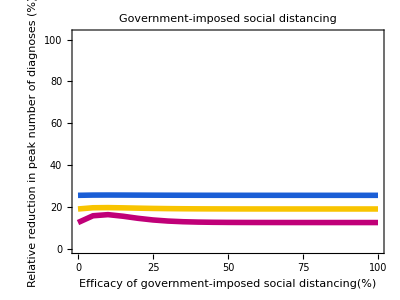

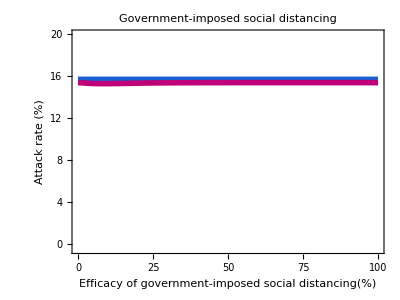

-Graphics-

```mathematica
imagePadding={{80,15},{73,7.5}};

SS16=ListLinePlot[{PeakGovBaseline,PeakGovMin,PeakGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,102.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS16",".pdf"],SS16];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS16",".eps"],SS16];


SS17=ListLinePlot[{AttackRateGovBaseline,AttackRateGovMin,AttackRateGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-0.5,20}},AxesOrigin->{0,0},Filling->{1->{2}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS17",".pdf"],SS17];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS17",".eps"],SS17];

SS18=ListLinePlot[{PeakTimingGovBaseline,PeakTimingGovMin,PeakTimingGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,800}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{"","","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],Graphics[{RGBColor[185/255,76/255,225/255],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}},ImagePadding->imagePadding,PlotRangePadding->None,PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],PlotLegends->LineLegend[Table[Style[Row[{label}],Black,13,"Text"],{label,{"7 days","9 days","5 days"}}],LegendLabel->Style["Recovery period\nof infectious\nwith mild disease",Black,13,"Text"]],FrameTicks->{{{{0,"0"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3/2,"18"}},None},{Automatic,None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS18",".pdf"],SS18];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS18",".eps"],SS18];
```

```mathematica
ReductionFactor=Table[i,{i,0,1,0.01}];

PeakMaskBaseline=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakMaskMin=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateMin,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakMaskMax=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateMax,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskBaseline=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskMin=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateMin,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskMax=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateMax,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskBaseline=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskMin=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateMin,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskMax=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateMax,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,99.9897},{99.,99.9895},{98.,99.9894},{97.,99.9892},{96.,99.9891},{95.,99.9889},{94.,99.9887},{93.,99.9886},{92.,99.9884},{91.,99.9882},{90.,99.988},{89.,99.9878},{88.,99.9876},{87.,99.9874},{86.,99.9872},{85.,99.987},{84.,99.9867},{83.,99.9865},{82.,99.9862},{81.,99.986},{80.,99.9857},{79.,99.9854},{78.,99.9851},{77.,99.9847},{76.,99.9844},{75.,99.984},{74.,99.9837},{73.,99.9832},{72.,99.9828},{71.,99.9823},{70.,99.9818},{69.,99.9812},{68.,99.9806},{67.,99.9799},{66.,99.9792},{65.,99.9783},{64.,99.9772},{63.,99.9758},{62.,99.9733},{61.,99.9687},{60.,99.9621},{59.,99.9522},{58.,99.9356},{57.,99.9046},{56.,99.8396},{55.,99.6973},{54.,99.4204},{53.,98.9754},{52.,98.3611},{51.,97.5905},{50.,96.6796},{49.,95.6439},{48.,94.4978},{47.,93.2544},{46.,91.9255},{45.,90.5218},{44.,89.053},{43.,87.5278},{42.,85.9542},{41.,84.3393},{40.,82.6896},{39.,81.011},{38.,79.3088},{37.,77.5876},{36.,75.8518},{35.,74.1053},{34.,72.3514},{33.,70.5933},{32.,68.8339},{31.,67.0755},{30.,65.3205},{29.,63.5709},{28.,61.8284},{27.,60.0946},{26.,58.3709},{25.,56.6586},{24.,54.9588},{23.,53.2724},{22.,51.6003},{21.,49.9432},{20.,48.3019},{19.,46.6767},{18.,45.0683},{17.,43.4769},{16.,41.903},{15.,40.3467},{14.,38.8084},{13.,37.2881},{12.,35.7861},{11.,34.3024},{10.,32.8369},{9.,31.3899},{8.,29.9612},{7.,28.5509},{6.,27.1588},{5.,25.7848},{4.,24.4289},{3.,23.091},{2.,21.771},{1.,20.4686},{0.,19.1837}}

{{100.,99.9899},{99.,99.9898},{98.,99.9896},{97.,99.9895},{96.,99.9894},{95.,99.9892},{94.,99.9891},{93.,99.989},{92.,99.9888},{91.,99.9887},{90.,99.9885},{89.,99.9883},{88.,99.9882},{87.,99.988},{86.,99.9878},{85.,99.9876},{84.,99.9874},{83.,99.9872},{82.,99.987},{81.,99.9868},{80.,99.9866},{79.,99.9864},{78.,99.9861},{77.,99.9859},{76.,99.9856},{75.,99.9854},{74.,99.9851},{73.,99.9848},{72.,99.9845},{71.,99.9841},{70.,99.9838},{69.,99.9834},{68.,99.983},{67.,99.9826},{66.,99.9821},{65.,99.9816},{64.,99.9811},{63.,99.9805},{62.,99.9798},{61.,99.9791},{60.,99.9782},{59.,99.977},{58.,99.9752},{57.,99.9712},{56.,99.9656},{55.,99.9573},{54.,99.9438},{53.,99.9196},{52.,99.8712},{51.,99.7676},{50.,99.5622},{49.,99.22},{48.,98.7328},{47.,98.1082},{46.,97.3583},{45.,96.4956},{44.,95.5315},{43.,94.477},{42.,93.3418},{41.,92.135},{40.,90.8648},{39.,89.5386},{38.,88.1633},{37.,86.7451},{36.,85.2897},{35.,83.8024},{34.,82.2878},{33.,80.7503},{32.,79.1937},{31.,77.6217},{30.,76.0375},{29.,74.4441},{28.,72.8441},{27.,71.2399},{26.,69.6337},{25.,68.0276},{24.,66.4233},{23.,64.8225},{22.,63.2265},{21.,61.6368},{20.,60.0546},{19.,58.4808},{18.,56.9164},{17.,55.3623},{16.,53.8193},{15.,52.288},{14.,50.7689},{13.,49.2627},{12.,47.7697},{11.,46.2904},{10.,44.8251},{9.,43.3741},{8.,41.9376},{7.,40.5159},{6.,39.1091},{5.,37.7173},{4.,36.3407},{3.,34.9793},{2.,33.6332},{1.,32.3024},{0.,30.9869}}

{{100.,99.9898},{99.,99.9897},{98.,99.9895},{97.,99.9893},{96.,99.9892},{95.,99.989},{94.,99.9888},{93.,99.9886},{92.,99.9884},{91.,99.9882},{90.,99.9879},{89.,99.9877},{88.,99.9875},{87.,99.9872},{86.,99.9869},{85.,99.9867},{84.,99.9864},{83.,99.986},{82.,99.9857},{81.,99.9854},{80.,99.985},{79.,99.9846},{78.,99.9842},{77.,99.9837},{76.,99.9833},{75.,99.9827},{74.,99.9822},{73.,99.9815},{72.,99.9808},{71.,99.98},{70.,99.9791},{69.,99.9781},{68.,99.9768},{67.,99.975},{66.,99.9716},{65.,99.9664},{64.,99.9587},{63.,99.9468},{62.,99.9263},{61.,99.8862},{60.,99.7973},{59.,99.5986},{58.,99.2216},{57.,98.6383},{56.,97.8568},{55.,96.8969},{54.,95.7797},{53.,94.525},{52.,93.1504},{51.,91.672},{50.,90.1042},{49.,88.4597},{48.,86.75},{47.,84.9855},{46.,83.1752},{45.,81.3274},{44.,79.4494},{43.,77.5478},{42.,75.6283},{41.,73.6961},{40.,71.7559},{39.,69.8117},{38.,67.8672},{37.,65.9255},{36.,63.9895},{35.,62.0617},{34.,60.1442},{33.,58.2391},{32.,56.3479},{31.,54.4722},{30.,52.6133},{29.,50.7721},{28.,48.9498},{27.,47.1469},{26.,45.3644},{25.,43.6026},{24.,41.8621},{23.,40.1432},{22.,38.4462},{21.,36.7713},{20.,35.1188},{19.,33.4886},{18.,31.8809},{17.,30.2956},{16.,28.7327},{15.,27.1921},{14.,25.6738},{13.,24.1775},{12.,22.7031},{11.,21.2505},{10.,19.8194},{9.,18.4096},{8.,17.021},{7.,15.6532},{6.,14.306},{5.,12.9792},{4.,11.6724},{3.,10.3855},{2.,9.11815},{1.,7.87001},{0.,6.64088}}

{{100.,0.0139929},{99.,0.0143083},{98.,0.0146382},{97.,0.0149835},{96.,0.0153453},{95.,0.0157249},{94.,0.0161236},{93.,0.0165428},{92.,0.0169843},{91.,0.0174499},{90.,0.0179415},{89.,0.0184615},{88.,0.0190124},{87.,0.0195969},{86.,0.0202184},{85.,0.0208804},{84.,0.0215871},{83.,0.0223432},{82.,0.0231541},{81.,0.024026},{80.,0.024966},{79.,0.0259827},{78.,0.0270857},{77.,0.0282867},{76.,0.0295994},{75.,0.0310405},{74.,0.0326297},{73.,0.0343915},{72.,0.0363557},{71.,0.0385599},{70.,0.0410512},{69.,0.0438904},{68.,0.0471564},{67.,0.0509542},{66.,0.0554265},{65.,0.0607718},{64.,0.0672748},{63.,0.0753581},{62.,0.0856753},{61.,0.09929},{60.,0.118038},{59.,0.145326},{58.,0.18798},{57.,0.260716},{56.,0.396241},{55.,0.661302},{54.,1.14896},{53.,1.87324},{52.,2.67945},{51.,3.4173},{50.,4.06489},{49.,4.65068},{48.,5.19629},{47.,5.71174},{46.,6.20132},{45.,6.66722},{44.,7.11091},{43.,7.53366},{42.,7.93661},{41.,8.32086},{40.,8.68743},{39.,9.03728},{38.,9.37132},{37.,9.6904},{36.,9.99534},{35.,10.2869},{34.,10.5658},{33.,10.8326},{32.,11.0881},{31.,11.3328},{30.,11.5672},{29.,11.7919},{28.,12.0072},{27.,12.2137},{26.,12.4119},{25.,12.602},{24.,12.7845},{23.,12.9598},{22.,13.1282},{21.,13.29},{20.,13.4455},{19.,13.595},{18.,13.7388},{17.,13.8772},{16.,14.0103},{15.,14.1385},{14.,14.2619},{13.,14.3808},{12.,14.4953},{11.,14.6056},{10.,14.7119},{9.,14.8145},{8.,14.9133},{7.,15.0087},{6.,15.1007},{5.,15.1895},{4.,15.2752},{3.,15.3579},{2.,15.4378},{1.,15.5149},{0.,15.5895}}

{{100.,0.0130921},{99.,0.0133529},{98.,0.0136242},{97.,0.0139069},{96.,0.0142015},{95.,0.014509},{94.,0.0148301},{93.,0.0151659},{92.,0.0155173},{91.,0.0158855},{90.,0.0162718},{89.,0.0166774},{88.,0.0171039},{87.,0.0175531},{86.,0.0180267},{85.,0.0185269},{84.,0.019056},{83.,0.0196166},{82.,0.0202117},{81.,0.0208445},{80.,0.0215188},{79.,0.022239},{78.,0.0230099},{77.,0.0238372},{76.,0.0247275},{75.,0.0256883},{74.,0.0267285},{73.,0.0278585},{72.,0.0290907},{71.,0.03044},{70.,0.0319241},{69.,0.0335648},{68.,0.0353886},{67.,0.0374287},{66.,0.0397266},{65.,0.0423356},{64.,0.0453246},{63.,0.0487847},{62.,0.0528386},{61.,0.0576559},{60.,0.0634775},{59.,0.0706567},{58.,0.0797327},{57.,0.0915668},{56.,0.107613},{55.,0.130488},{54.,0.165242},{53.,0.222272},{52.,0.323787},{51.,0.515355},{50.,0.872052},{49.,1.45253},{48.,2.19286},{47.,2.93521},{46.,3.59448},{45.,4.17664},{44.,4.70797},{43.,5.20557},{42.,5.67754},{41.,6.12753},{40.,6.55741},{39.,6.96842},{38.,7.36158},{37.,7.7378},{36.,8.09793},{35.,8.4428},{34.,8.77317},{33.,9.08976},{32.,9.39327},{31.,9.68434},{30.,9.96359},{29.,10.2316},{28.,10.4889},{27.,10.7361},{26.,10.9736},{25.,11.2018},{24.,11.4212},{23.,11.6323},{22.,11.8353},{21.,12.0306},{20.,12.2186},{19.,12.3996},{18.,12.574},{17.,12.7419},{16.,12.9038},{15.,13.0598},{14.,13.2101},{13.,13.3552},{12.,13.4951},{11.,13.6301},{10.,13.7604},{9.,13.8861},{8.,14.0076},{7.,14.1249},{6.,14.2382},{5.,14.3476},{4.,14.4534},{3.,14.5557},{2.,14.6546},{1.,14.7502},{0.,14.8427}}

{{100.,0.0147718},{99.,0.0151517},{98.,0.0155512},{97.,0.015972},{96.,0.0164158},{95.,0.0168845},{94.,0.0173803},{93.,0.0179056},{92.,0.018463},{91.,0.0190556},{90.,0.0196868},{89.,0.0203605},{88.,0.0210811},{87.,0.0218537},{86.,0.0226841},{85.,0.023579},{84.,0.0245462},{83.,0.0255948},{82.,0.0267354},{81.,0.0279808},{80.,0.0293459},{79.,0.0308489},{78.,0.0325118},{77.,0.0343615},{76.,0.0364311},{75.,0.0387625},{74.,0.0414085},{73.,0.0444373},{72.,0.0479385},{71.,0.0520316},{70.,0.0568803},{69.,0.0627144},{68.,0.0698669},{67.,0.0788381},{66.,0.0904138},{65.,0.105897},{64.,0.127595},{63.,0.159931},{62.,0.212169},{61.,0.305341},{60.,0.488174},{59.,0.856911},{58.,1.50757},{57.,2.35863},{56.,3.19303},{55.,3.92537},{54.,4.57957},{53.,5.18406},{52.,5.75211},{51.,6.28909},{50.,6.79765},{49.,7.27968},{48.,7.73677},{47.,8.17043},{46.,8.58205},{45.,8.97296},{44.,9.34438},{43.,9.69749},{42.,10.0333},{41.,10.353},{40.,10.6573},{39.,10.9473},{38.,11.2237},{37.,11.4873},{36.,11.7387},{35.,11.9787},{34.,12.2078},{33.,12.4266},{32.,12.6357},{31.,12.8355},{30.,13.0267},{29.,13.2095},{28.,13.3845},{27.,13.5521},{26.,13.7126},{25.,13.8663},{24.,14.0136},{23.,14.1549},{22.,14.2904},{21.,14.4204},{20.,14.5451},{19.,14.6649},{18.,14.7799},{17.,14.8903},{16.,14.9965},{15.,15.0985},{14.,15.1965},{13.,15.2908},{12.,15.3815},{11.,15.4688},{10.,15.5527},{9.,15.6336},{8.,15.7114},{7.,15.7863},{6.,15.8585},{5.,15.9281},{4.,15.9951},{3.,16.0597},{2.,16.122},{1.,16.1821},{0.,16.24}}

{{100.,71.893},{99.,72.0936},{98.,72.3142},{97.,72.5348},{96.,72.7553},{95.,72.996},{94.,73.2366},{93.,73.4773},{92.,73.738},{91.,73.9987},{90.,74.2794},{89.,74.5802},{88.,74.8811},{87.,75.1819},{86.,75.5228},{85.,75.8637},{84.,76.2247},{83.,76.6057},{82.,77.0068},{81.,77.4479},{80.,77.8891},{79.,78.3905},{78.,78.8918},{77.,79.4533},{76.,80.075},{75.,80.7167},{74.,81.4587},{73.,82.2609},{72.,83.1432},{71.,84.166},{70.,85.3291},{69.,86.7128},{68.,88.3572},{67.,90.4027},{66.,93.0699},{65.,96.7798},{64.,102.676},{63.,115.129},{62.,266.155},{61.,367.647},{60.,439.801},{59.,513.178},{58.,593.814},{57.,679.344},{56.,751.137},{55.,773.376},{54.,737.46},{53.,675.855},{52.,614.289},{51.,560.866},{50.,516.166},{49.,478.886},{48.,447.542},{47.,420.93},{46.,398.089},{45.,378.276},{44.,360.909},{43.,345.588},{42.,331.931},{41.,319.698},{40.,308.669},{39.,298.682},{38.,289.557},{37.,281.215},{36.,273.554},{35.,266.475},{34.,259.938},{33.,253.842},{32.,248.166},{31.,242.872},{30.,237.919},{29.,233.266},{28.,228.875},{27.,224.743},{26.,220.853},{25.,217.163},{24.,213.654},{23.,210.325},{22.,207.176},{21.,204.168},{20.,201.3},{19.,198.573},{18.,195.946},{17.,193.439},{16.,191.053},{15.,188.747},{14.,186.541},{13.,184.415},{12.,182.37},{11.,180.404},{10.,178.519},{9.,176.694},{8.,174.93},{7.,173.245},{6.,171.601},{5.,170.016},{4.,168.472},{3.,166.988},{2.,165.544},{1.,164.141},{0.,162.797}}

{{100.,72.8957},{99.,73.0762},{98.,73.2567},{97.,73.4372},{96.,73.6177},{95.,73.8182},{94.,74.0187},{93.,74.2193},{92.,74.4198},{91.,74.6404},{90.,74.861},{89.,75.1016},{88.,75.3423},{87.,75.5829},{86.,75.8436},{85.,76.1043},{84.,76.3851},{83.,76.6859},{82.,76.9867},{81.,77.3076},{80.,77.6485},{79.,77.9894},{78.,78.3704},{77.,78.7715},{76.,79.1726},{75.,79.6338},{74.,80.095},{73.,80.6164},{72.,81.178},{71.,81.7796},{70.,82.4413},{69.,83.1633},{68.,83.9855},{67.,84.908},{66.,85.9708},{65.,87.1941},{64.,88.6781},{63.,90.4829},{62.,92.8292},{61.,96.078},{60.,101.051},{59.,110.898},{58.,233.226},{57.,367.306},{56.,444.253},{55.,519.635},{54.,601.415},{53.,689.17},{52.,768.704},{51.,807.167},{50.,785.248},{49.,727.594},{48.,664.003},{47.,606.729},{46.,558.078},{45.,517.249},{44.,482.836},{43.,453.598},{42.,428.49},{41.,406.712},{40.,387.661},{39.,370.856},{38.,355.896},{37.,342.5},{36.,330.427},{35.,319.498},{34.,309.531},{33.,300.427},{32.,292.044},{31.,284.343},{30.,277.184},{29.,270.566},{28.,264.39},{27.,258.614},{26.,253.22},{25.,248.146},{24.,243.393},{23.,238.901},{22.,234.67},{21.,230.659},{20.,226.849},{19.,223.239},{18.,219.81},{17.,216.561},{16.,213.453},{15.,210.485},{14.,207.637},{13.,204.93},{12.,202.323},{11.,199.837},{10.,197.45},{9.,195.144},{8.,192.938},{7.,190.812},{6.,188.767},{5.,186.802},{4.,184.896},{3.,183.072},{2.,181.287},{1.,179.582},{0.,177.918}}

{{100.,73.1564},{99.,73.4171},{98.,73.6979},{97.,73.9586},{96.,74.2594},{95.,74.5602},{94.,74.861},{93.,75.2019},{92.,75.5428},{91.,75.8837},{90.,76.2648},{89.,76.6458},{88.,77.0469},{87.,77.4881},{86.,77.9493},{85.,78.4306},{84.,78.9319},{83.,79.4934},{82.,80.075},{81.,80.7167},{80.,81.3985},{79.,82.1606},{78.,82.9828},{77.,83.9053},{76.,84.928},{75.,86.1112},{74.,87.4548},{73.,89.0591},{72.,90.9843},{71.,93.3907},{70.,96.5994},{69.,101.172},{68.,108.792},{67.,128.304},{66.,295.915},{65.,373.924},{64.,440.924},{63.,512.155},{62.,591.608},{61.,674.631},{60.,736.818},{59.,741.13},{58.,692.64},{57.,628.728},{56.,569.75},{55.,520.096},{54.,479.086},{53.,445.075},{52.,416.558},{51.,392.373},{50.,371.598},{49.,353.569},{48.,337.767},{47.,323.789},{46.,311.356},{45.,300.186},{44.,290.119},{43.,280.994},{42.,272.652},{41.,265.032},{40.,258.013},{39.,251.535},{38.,245.519},{37.,239.944},{36.,234.75},{35.,229.877},{34.,225.325},{33.,221.054},{32.,217.023},{31.,213.233},{30.,209.643},{29.,206.234},{28.,203.025},{27.,199.957},{26.,197.049},{25.,194.282},{24.,191.635},{23.,189.108},{22.,186.701},{21.,184.395},{20.,182.169},{19.,180.043},{18.,178.018},{17.,176.053},{16.,174.168},{15.,172.343},{14.,170.598},{13.,168.914},{12.,167.289},{11.,165.725},{10.,164.201},{9.,162.737},{8.,161.313},{7.,159.929},{6.,158.586},{5.,157.302},{4.,156.039},{3.,154.836},{2.,153.653},{1.,152.489},{0.,151.386}}

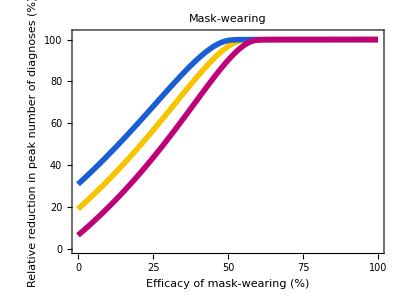

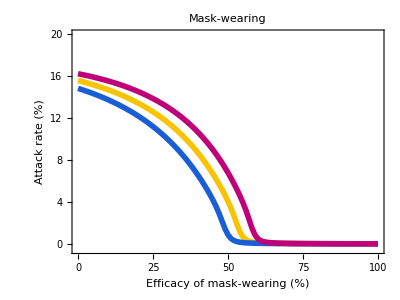

-Graphics-

```mathematica
imagePadding={{80,15},{73,7.5}};

SS19=ListLinePlot[{PeakMaskBaseline,PeakMaskMin,PeakMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,102.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of mask-wearing (%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS19",".pdf"],SS19];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS19",".eps"],SS19];

SS20=ListLinePlot[{AttackRateMaskBaseline,AttackRateMaskMin,AttackRateMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-0.5,20}},AxesOrigin->{0,0},Filling->{1->{2}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of mask-wearing (%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS20",".pdf"],SS20];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS20",".eps"],SS20];

SS21=ListLinePlot[{PeakTimingMaskBaseline,PeakTimingMaskMin,PeakTimingMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,365 5/2+20}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{"","","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],Graphics[{RGBColor[185/255,76/255,225/255],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of mask-wearing (%)",None}},ImagePadding->imagePadding,PlotRangePadding->None,PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],PlotLegends->LineLegend[Table[Style[Row[{label}],Black,13,"Text"],{label,{"5 days","7 days","3 days"}}],LegendLabel->Style["Delay from onset\nof infectiousness\nto diagnosis",Black,13,"Text"]],FrameTicks->{{{{0,"0"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3/2,"18"},{365 5/2,"30"}},None},{Automatic,None}}]
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS21",".pdf"],SS21];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS21",".eps"],SS21];
```

```mathematica
ReductionFactor=Table[i,{i,0,1,0.1}];

PeakGovBaseline=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakGovMin=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateMin,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakGovMax=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateMax,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovBaseline=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovMin=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateMin,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovMax=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateMax,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovBaseline=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovMin=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateMin,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovMax=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateMax,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,19.1862},{90.,19.1867},{80.,19.1876},{70.,19.1898},{60.,19.1954},{50.,19.2108},{40.,19.2514},{30.,19.3545},{20.,19.5743},{10.,19.8368},{0.,19.1837}}

{{100.,30.9891},{90.,30.9895},{80.,30.9903},{70.,30.9921},{60.,30.9964},{50.,31.0068},{40.,31.03},{30.,31.0806},{20.,31.1758},{10.,31.2745},{0.,30.9869}}

{{100.,6.64312},{90.,6.64356},{80.,6.64445},{70.,6.64655},{60.,6.6527},{50.,6.67259},{40.,6.73684},{30.,6.9267},{20.,7.38368},{10.,7.98765},{0.,6.64089}}

{{100.,15.5894},{90.,15.5894},{80.,15.5894},{70.,15.5893},{60.,15.5892},{50.,15.5888},{40.,15.5878},{30.,15.5853},{20.,15.58},{10.,15.5735},{0.,15.5895}}

{{100.,14.8426},{90.,14.8426},{80.,14.8426},{70.,14.8425},{60.,14.8424},{50.,14.8421},{40.,14.8414},{30.,14.8398},{20.,14.8369},{10.,14.8339},{0.,14.8427}}

{{100.,16.24},{90.,16.24},{80.,16.2399},{70.,16.2399},{60.,16.2398},{50.,16.2394},{40.,16.2382},{30.,16.2346},{20.,16.2259},{10.,16.214},{0.,16.24}}

{{100.,366.865},{90.,327.359},{80.,299.424},{70.,277.084},{60.,258.253},{50.,240.867},{40.,223.761},{30.,207.357},{20.,191.835},{10.,177.095},{0.,162.797}}

{{100.,386.778},{90.,344.886},{80.,316.951},{70.,295.152},{60.,277.345},{50.,261.001},{40.,243.775},{30.,226.348},{20.,209.543},{10.,193.459},{0.,177.918}}

{{100.,351.464},{90.,313.},{80.,285.266},{70.,262.304},{60.,242.25},{50.,224.222},{40.,207.718},{30.,192.417},{20.,178.118},{10.,164.562},{0.,151.386}}

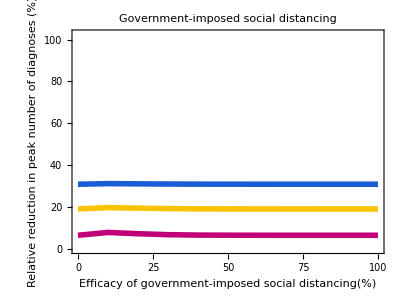

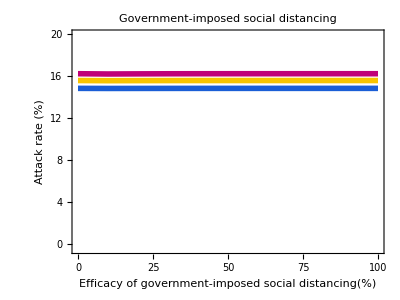

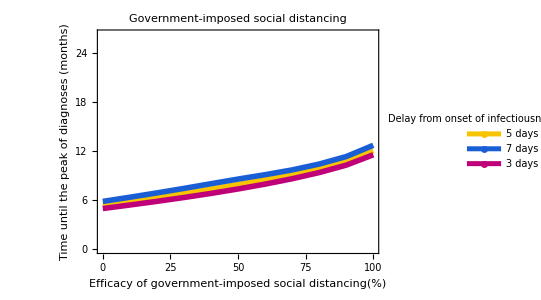

```mathematica
imagePadding={{80,15},{73,7.5}};

SS22=ListLinePlot[{PeakGovBaseline,PeakGovMin,PeakGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,102.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS22",".pdf"],SS22];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS22",".eps"],SS22];


SS23=ListLinePlot[{AttackRateGovBaseline,AttackRateGovMin,AttackRateGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-0.5,20}},AxesOrigin->{0,0},Filling->{1->{2}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS23",".pdf"],SS23];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS23",".eps"],SS23];

SS24=ListLinePlot[{PeakTimingGovBaseline,PeakTimingGovMin,PeakTimingGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,800}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{"","","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],Graphics[{RGBColor[185/255,76/255,225/255],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}},ImagePadding->imagePadding,PlotRangePadding->None,PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],PlotLegends->LineLegend[Table[Style[Row[{label}],Black,13,"Text"],{label,{"5 days","7 days","3 days"}}],LegendLabel->Style["Delay from onset\nof infectiousness\nto diagnosis",Black,13,"Text"]],FrameTicks->{{{{0,"0"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3/2,"18"}},None},{Automatic,None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS24",".pdf"],SS24];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS24",".eps"],SS24];
```

```mathematica
ReductionFactor=Table[i,{i,0,1,0.01}];
Subscript[t, end]=3;

PeakMaskBaseline=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakMaskMin=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberMin,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakMaskMax=PeakRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberMax,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskBaseline=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskMin=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberMin,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

AttackRateMaskMax=AttackRateRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberMax,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskBaseline=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskMin=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberMin,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]

PeakTimingMaskMax=PeakTimingRange["Mask",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberMax,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 1]-> factor}]]
```

{{100.,99.9897},{99.,99.9895},{98.,99.9894},{97.,99.9892},{96.,99.9891},{95.,99.9889},{94.,99.9887},{93.,99.9886},{92.,99.9884},{91.,99.9882},{90.,99.988},{89.,99.9878},{88.,99.9876},{87.,99.9874},{86.,99.9872},{85.,99.987},{84.,99.9867},{83.,99.9865},{82.,99.9862},{81.,99.986},{80.,99.9857},{79.,99.9854},{78.,99.9851},{77.,99.9847},{76.,99.9844},{75.,99.984},{74.,99.9837},{73.,99.9832},{72.,99.9828},{71.,99.9823},{70.,99.9818},{69.,99.9812},{68.,99.9806},{67.,99.9799},{66.,99.9792},{65.,99.9783},{64.,99.9772},{63.,99.9758},{62.,99.9733},{61.,99.9687},{60.,99.9621},{59.,99.9522},{58.,99.9356},{57.,99.9046},{56.,99.8396},{55.,99.6973},{54.,99.4204},{53.,98.9754},{52.,98.3611},{51.,97.5905},{50.,96.6796},{49.,95.6439},{48.,94.4978},{47.,93.2544},{46.,91.9255},{45.,90.5218},{44.,89.053},{43.,87.5278},{42.,85.9542},{41.,84.3393},{40.,82.6896},{39.,81.011},{38.,79.3088},{37.,77.5876},{36.,75.8518},{35.,74.1053},{34.,72.3514},{33.,70.5933},{32.,68.8339},{31.,67.0755},{30.,65.3205},{29.,63.5709},{28.,61.8284},{27.,60.0946},{26.,58.3709},{25.,56.6586},{24.,54.9588},{23.,53.2724},{22.,51.6003},{21.,49.9432},{20.,48.3019},{19.,46.6767},{18.,45.0683},{17.,43.4769},{16.,41.9029},{15.,40.3467},{14.,38.8084},{13.,37.2881},{12.,35.7861},{11.,34.3024},{10.,32.837},{9.,31.3899},{8.,29.9612},{7.,28.5509},{6.,27.1587},{5.,25.7848},{4.,24.4289},{3.,23.091},{2.,21.771},{1.,20.4686},{0.,19.1837}}

{{100.,99.9944},{99.,99.9943},{98.,99.9942},{97.,99.9942},{96.,99.9941},{95.,99.994},{94.,99.9939},{93.,99.9939},{92.,99.9938},{91.,99.9937},{90.,99.9936},{89.,99.9935},{88.,99.9934},{87.,99.9933},{86.,99.9932},{85.,99.9931},{84.,99.993},{83.,99.9929},{82.,99.9928},{81.,99.9927},{80.,99.9925},{79.,99.9924},{78.,99.9923},{77.,99.9921},{76.,99.992},{75.,99.9919},{74.,99.9917},{73.,99.9915},{72.,99.9914},{71.,99.9912},{70.,99.991},{69.,99.9908},{68.,99.9906},{67.,99.9904},{66.,99.9902},{65.,99.9899},{64.,99.9896},{63.,99.9894},{62.,99.9891},{61.,99.9887},{60.,99.9884},{59.,99.988},{58.,99.9876},{57.,99.9871},{56.,99.9865},{55.,99.9858},{54.,99.9848},{53.,99.9831},{52.,99.981},{51.,99.9783},{50.,99.9746},{49.,99.9695},{48.,99.9618},{47.,99.9493},{46.,99.927},{45.,99.8823},{44.,99.7897},{43.,99.6134},{42.,99.3286},{41.,98.9298},{40.,98.4222},{39.,97.8141},{38.,97.1142},{37.,96.3309},{36.,95.4717},{35.,94.544},{34.,93.5542},{33.,92.5084},{32.,91.4123},{31.,90.2711},{30.,89.0895},{29.,87.872},{28.,86.6227},{27.,85.3453},{26.,84.0433},{25.,82.7199},{24.,81.3781},{23.,80.0205},{22.,78.6498},{21.,77.2681},{20.,75.8776},{19.,74.4803},{18.,73.0779},{17.,71.6721},{16.,70.2645},{15.,68.8563},{14.,67.4488},{13.,66.0432},{12.,64.6406},{11.,63.2419},{10.,61.8481},{9.,60.4598},{8.,59.0778},{7.,57.7029},{6.,56.3355},{5.,54.9763},{4.,53.6257},{3.,52.2842},{2.,50.9521},{1.,49.6298},{0.,48.3176}}

{{100.,99.984},{99.,99.9838},{98.,99.9835},{97.,99.9833},{96.,99.983},{95.,99.9827},{94.,99.9825},{93.,99.9822},{92.,99.9819},{91.,99.9815},{90.,99.9812},{89.,99.9809},{88.,99.9805},{87.,99.9801},{86.,99.9797},{85.,99.9793},{84.,99.9789},{83.,99.9784},{82.,99.9779},{81.,99.9774},{80.,99.9768},{79.,99.9763},{78.,99.9756},{77.,99.975},{76.,99.9742},{75.,99.9734},{74.,99.9725},{73.,99.9715},{72.,99.9704},{71.,99.9691},{70.,99.9675},{69.,99.9654},{68.,99.9621},{67.,99.9536},{66.,99.9398},{65.,99.9154},{64.,99.8657},{63.,99.7518},{62.,99.4952},{61.,99.0201},{60.,98.3052},{59.,97.3668},{58.,96.2311},{57.,94.9238},{56.,93.4685},{55.,91.8864},{54.,90.1962},{53.,88.4146},{52.,86.5562},{51.,84.6342},{50.,82.6602},{49.,80.6443},{48.,78.5956},{47.,76.5221},{46.,74.4308},{45.,72.3279},{44.,70.2189},{43.,68.1086},{42.,66.0011},{41.,63.9002},{40.,61.809},{39.,59.7303},{38.,57.6664},{37.,55.6196},{36.,53.5916},{35.,51.5839},{34.,49.5978},{33.,47.6344},{32.,45.6946},{31.,43.7792},{30.,41.8888},{29.,40.0239},{28.,38.1847},{27.,36.3717},{26.,34.585},{25.,32.8246},{24.,31.0907},{23.,29.3832},{22.,27.702},{21.,26.047},{20.,24.4181},{19.,22.815},{18.,21.2375},{17.,19.6854},{16.,18.1584},{15.,16.6563},{14.,15.1786},{13.,13.7251},{12.,12.2954},{11.,10.8893},{10.,9.50623},{9.,8.14601},{8.,6.80819},{7.,5.49246},{6.,4.19844},{5.,2.92574},{4.,1.674},{3.,0.442887},{2.,-0.767985},{1.,-1.95898},{0.,-3.13045}}

{{100.,0.0168099},{99.,0.0171898},{98.,0.0175871},{97.,0.018003},{96.,0.0184389},{95.,0.0188963},{94.,0.0193767},{93.,0.019882},{92.,0.0204141},{91.,0.0209753},{90.,0.0215679},{89.,0.0221949},{88.,0.0228591},{87.,0.0235641},{86.,0.0243137},{85.,0.0251123},{84.,0.025965},{83.,0.0268774},{82.,0.0278562},{81.,0.0289087},{80.,0.0300438},{79.,0.0312716},{78.,0.0326041},{77.,0.0340553},{76.,0.035642},{75.,0.0373843},{74.,0.0393064},{73.,0.0414379},{72.,0.0438154},{71.,0.0464845},{70.,0.0495029},{69.,0.0529447},{68.,0.0569064},{67.,0.0615168},{66.,0.0669506},{65.,0.0734517},{64.,0.0813705},{63.,0.0912283},{62.,0.103834},{61.,0.120511},{60.,0.143556},{59.,0.177284},{58.,0.230529},{57.,0.322928},{56.,0.499075},{55.,0.843161},{54.,1.42405},{53.,2.15048},{52.,2.85943},{51.,3.50493},{50.,4.10362},{49.,4.66922},{48.,5.20709},{47.,5.71932},{46.,6.20723},{45.,6.67203},{44.,7.11488},{43.,7.53694},{42.,7.93932},{41.,8.32307},{40.,8.68921},{39.,9.03869},{38.,9.37241},{37.,9.69121},{36.,9.9959},{35.,10.2872},{34.,10.5659},{33.,10.8327},{32.,11.0881},{31.,11.3328},{30.,11.5672},{29.,11.7919},{28.,12.0072},{27.,12.2137},{26.,12.4119},{25.,12.602},{24.,12.7845},{23.,12.9598},{22.,13.1282},{21.,13.29},{20.,13.4455},{19.,13.595},{18.,13.7388},{17.,13.8772},{16.,14.0103},{15.,14.1385},{14.,14.2619},{13.,14.3808},{12.,14.4953},{11.,14.6056},{10.,14.7119},{9.,14.8145},{8.,14.9133},{7.,15.0087},{6.,15.1007},{5.,15.1895},{4.,15.2752},{3.,15.3579},{2.,15.4378},{1.,15.5149},{0.,15.5895}}

{{100.,0.0109715},{99.,0.0111698},{98.,0.0113752},{97.,0.0115883},{96.,0.0118094},{95.,0.0120391},{94.,0.0122778},{93.,0.012526},{92.,0.0127844},{91.,0.0130536},{90.,0.0133343},{89.,0.0136272},{88.,0.0139332},{87.,0.0142531},{86.,0.0145879},{85.,0.0149386},{84.,0.0153066},{83.,0.0156929},{82.,0.0160992},{81.,0.0165268},{80.,0.0169776},{79.,0.0174536},{78.,0.0179568},{77.,0.0184898},{76.,0.0190551},{75.,0.019656},{74.,0.0202957},{73.,0.0209784},{72.,0.0217084},{71.,0.0224908},{70.,0.0233316},{69.,0.0242375},{68.,0.0252166},{67.,0.026278},{66.,0.0274327},{65.,0.0286937},{64.,0.0300765},{63.,0.0315998},{62.,0.0332862},{61.,0.0351638},{60.,0.0372674},{59.,0.0396407},{58.,0.0423399},{57.,0.0454376},{56.,0.0490302},{55.,0.0532476},{54.,0.0582699},{53.,0.0643535},{52.,0.0718757},{51.,0.0814145},{50.,0.0938978},{49.,0.1109},{48.,0.135273},{47.,0.17255},{46.,0.234166},{45.,0.344322},{44.,0.550521},{43.,0.920536},{42.,1.47974},{41.,2.13485},{40.,2.76142},{39.,3.32054},{38.,3.82787},{37.,4.302},{36.,4.7528},{35.,5.18446},{34.,5.59885},{33.,5.99701},{32.,6.37973},{31.,6.74769},{30.,7.10157},{29.,7.44198},{28.,7.76954},{27.,8.08481},{26.,8.38835},{25.,8.68069},{24.,8.96234},{23.,9.23377},{22.,9.49542},{21.,9.74771},{20.,9.99103},{19.,10.2257},{18.,10.4522},{17.,10.6708},{16.,10.8818},{15.,11.0856},{14.,11.2824},{13.,11.4725},{12.,11.6563},{11.,11.8338},{10.,12.0055},{9.,12.1715},{8.,12.3321},{7.,12.4875},{6.,12.6378},{5.,12.7833},{4.,12.9242},{3.,13.0606},{2.,13.1927},{1.,13.3206},{0.,13.4446}}

{{100.,0.0226962},{99.,0.023311},{98.,0.0239599},{97.,0.0246457},{96.,0.0253718},{95.,0.0261418},{94.,0.0269599},{93.,0.0278306},{92.,0.0287593},{91.,0.0297519},{90.,0.0308155},{89.,0.0319578},{88.,0.0331881},{87.,0.0345169},{86.,0.0359567},{85.,0.0375222},{84.,0.0392305},{83.,0.0411025},{82.,0.043163},{81.,0.0454422},{80.,0.0479773},{79.,0.0508142},{78.,0.0540109},{77.,0.0576411},{76.,0.0618001},{75.,0.0666138},{74.,0.0722511},{73.,0.0789448},{72.,0.0870242},{71.,0.0969706},{70.,0.109515},{69.,0.125823},{68.,0.147857},{67.,0.179179},{66.,0.226842},{65.,0.30636},{64.,0.455035},{63.,0.758498},{62.,1.33182},{61.,2.12288},{60.,2.92546},{59.,3.6685},{58.,4.36347},{57.,5.0194},{56.,5.63923},{55.,6.22465},{54.,6.77741},{53.,7.29936},{52.,7.79234},{51.,8.25814},{50.,8.69849},{49.,9.11499},{48.,9.50915},{47.,9.88239},{46.,10.236},{45.,10.5713},{44.,10.8893},{43.,11.1911},{42.,11.4778},{41.,11.7501},{40.,12.0092},{39.,12.2557},{38.,12.4903},{37.,12.7137},{36.,12.9265},{35.,13.1293},{34.,13.3226},{33.,13.5069},{32.,13.6828},{31.,13.8507},{30.,14.0111},{29.,14.1642},{28.,14.3106},{27.,14.4506},{26.,14.5844},{25.,14.7125},{24.,14.835},{23.,14.9523},{22.,15.0647},{21.,15.1724},{20.,15.2756},{19.,15.3745},{18.,15.4693},{17.,15.5603},{16.,15.6476},{15.,15.7313},{14.,15.8118},{13.,15.889},{12.,15.9632},{11.,16.0344},{10.,16.1029},{9.,16.1687},{8.,16.232},{7.,16.2929},{6.,16.3514},{5.,16.4078},{4.,16.462},{3.,16.5141},{2.,16.5644},{1.,16.6127},{0.,16.6593}}

{{100.,1570230/21841},{99.,1574610/21841},{98.,1579355/21841},{97.,1584100/21841},{96.,1588845/21841},{95.,1593955/21841},{94.,1599430/21841},{93.,1604905/21841},{92.,1610380/21841},{91.,1616220/21841},{90.,1622425/21841},{89.,1628630/21841},{88.,1635200/21841},{87.,1642135/21841},{86.,1649435/21841},{85.,1657100/21841},{84.,1664765/21841},{83.,1673160/21841},{82.,1681920/21841},{81.,1691410/21841},{80.,1701265/21841},{79.,1711850/21841},{78.,1723165/21841},{77.,1735575/21841},{76.,1748715/21841},{75.,1762950/21841},{74.,1779010/21841},{73.,1796530/21841},{72.,1815875/21841},{71.,1838140/21841},{70.,1863690/21841},{69.,1893620/21841},{68.,1929755/21841},{67.,1974285/21841},{66.,2032685/21841},{65.,2113715/21841},{64.,2242560/21841},{63.,2514485/21841},{62.,5813355/21841},{61.,8030000/21841},{60.,9605705/21841},{59.,11208420/21841},{58.,12969180/21841},{57.,14837615/21841},{56.,16405655/21841},{55.,16891470/21841},{54.,16106720/21841},{53.,14761330/21841},{52.,13416670/21841},{51.,12249765/21841},{50.,11273390/21841},{49.,10459075/21841},{48.,9774700/21841},{47.,9193620/21841},{46.,8694665/21841},{45.,8261775/21841},{44.,7882540/21841},{43.,7547835/21841},{42.,7249630/21841},{41.,6982450/21841},{40.,6741915/21841},{39.,6523280/21841},{38.,6324355/21841},{37.,6142220/21841},{36.,5974685/21841},{35.,5820290/21841},{34.,5677210/21841},{33.,5543985/21841},{32.,5420250/21841},{31.,5304545/21841},{30.,5196140/21841},{29.,5094670/21841},{28.,4999040/21841},{27.,4908520/21841},{26.,4823475/21841},{25.,4742810/21841},{24.,4666525/21841},{23.,4593890/21841},{22.,4524905/21841},{21.,4459205/21841},{20.,4396425/21841},{19.,4336930/21841},{18.,4279625/21841},{17.,4224875/21841},{16.,4172680/21841},{15.,4122310/21841},{14.,4074130/21841},{13.,4027775/21841},{12.,3983245/21841},{11.,3940175/21841},{10.,3898930/21841},{9.,3859145/21841},{8.,3820820/21841},{7.,3783590/21841},{6.,3747820/21841},{5.,3713145/21841},{4.,3679565/21841},{3.,3647080/21841},{2.,3615690/21841},{1.,3585030/21841},{0.,3555465/21841}}

{{100.,1988520/21841},{99.,1993630/21841},{98.,1998740/21841},{97.,2003850/21841},{96.,2009325/21841},{95.,2015165/21841},{94.,2020640/21841},{93.,2026480/21841},{92.,2032685/21841},{91.,2038890/21841},{90.,2045095/21841},{89.,2051665/21841},{88.,2058600/21841},{87.,2065535/21841},{86.,2072470/21841},{85.,2080135/21841},{84.,2087800/21841},{83.,2095465/21841},{82.,2103860/21841},{81.,2112255/21841},{80.,2121015/21841},{79.,2130505/21841},{78.,2139995/21841},{77.,2150215/21841},{76.,2160800/21841},{75.,2171750/21841},{74.,2183430/21841},{73.,2195840/21841},{72.,2208615/21841},{71.,2222485/21841},{70.,2237450/21841},{69.,2253145/21841},{68.,2270300/21841},{67.,2288550/21841},{66.,2308990/21841},{65.,2330890/21841},{64.,2355345/21841},{63.,2382720/21841},{62.,2414110/21841},{61.,2450245/21841},{60.,2492585/21841},{59.,2544415/21841},{58.,2610115/21841},{57.,2698445/21841},{56.,2831670/21841},{55.,3086805/21841},{54.,5606765/21841},{53.,7751140/21841},{52.,8981555/21841},{51.,10133495/21841},{50.,11348215/21841},{49.,12700175/21841},{48.,14246315/21841},{47.,16011820/21841},{46.,17905805/21841},{45.,19527500/21841},{44.,20135955/21841},{43.,19440265/21841},{42.,18033555/21841},{41.,16528660/21841},{40.,15173780/21841},{39.,14015270/21841},{38.,13035610/21841},{37.,12205235/21841},{36.,11495310/21841},{35.,10882475/21841},{34.,10349210/21841},{33.,9880550/21841},{32.,9465545/21841},{31.,9095435/21841},{30.,8763285/21841},{29.,8463255/21841},{28.,8190965/21841},{27.,7942035/21841},{26.,7714275/21841},{25.,7504765/21841},{24.,7311315/21841},{23.,7131735/21841},{22.,6964930/21841},{21.,6809440/21841},{20.,6664170/21841},{19.,6528025/21841},{18.,6399910/21841},{17.,6279460/21841},{16.,6165945/21841},{15.,6058270/21841},{14.,5956800/21841},{13.,5860440/21841},{12.,5768825/21841},{11.,5681590/21841},{10.,5598735/21841},{9.,5519530/21841},{8.,5443975/21841},{7.,5371705/21841},{6.,5302720/21841},{5.,5236290/21841},{4.,5172780/21841},{3.,5111825/21841},{2.,5053060/21841},{1.,4996485/21841},{0.,4942100/21841}}

{{100.,1338820/21841},{99.,1343200/21841},{98.,1347945/21841},{97.,1352690/21841},{96.,1357435/21841},{95.,1362910/21841},{94.,1368020/21841},{93.,1373860/21841},{92.,1379700/21841},{91.,1385905/21841},{90.,1392475/21841},{89.,1399410/21841},{88.,1406710/21841},{87.,1414375/21841},{86.,1422405/21841},{85.,1431165/21841},{84.,1440655/21841},{83.,1450875/21841},{82.,1461825/21841},{81.,1473870/21841},{80.,1487375/21841},{79.,1501975/21841},{78.,1518400/21841},{77.,1537380/21841},{76.,1558915/21841},{75.,1584465/21841},{74.,1615125/21841},{73.,1653085/21841},{72.,1702725/21841},{71.,1770980/21841},{70.,1876465/21841},{69.,2076120/21841},{68.,3514950/21841},{67.,7651495/21841},{66.,9618115/21841},{65.,11549330/21841},{64.,13461930/21841},{63.,14768630/21841},{62.,14696360/21841},{61.,13583110/21841},{60.,12257430/21841},{59.,11076655/21841},{58.,10097360/21841},{57.,9293630/21841},{56.,8628600/21841},{55.,8072340/21841},{54.,7600395/21841},{53.,7195245/21841},{52.,6844115/21841},{51.,6536055/21841},{50.,6264130/21841},{49.,6021770/21841},{48.,5804230/21841},{47.,5608225/21841},{46.,5430470/21841},{45.,5268045/21841},{44.,5119490/21841},{43.,4982980/21841},{42.,4856690/21841},{41.,4739890/21841},{40.,4631120/21841},{39.,4530015/21841},{38.,4435480/21841},{37.,4346785/21841},{36.,4263565/21841},{35.,4185090/21841},{34.,4111360/21841},{33.,4041645/21841},{32.,3975580/21841},{31.,3912800/21841},{30.,3853305/21841},{29.,3796730/21841},{28.,3743075/21841},{27.,3691610/21841},{26.,3642700/21841},{25.,3595615/21841},{24.,3550720/21841},{23.,3507650/21841},{22.,3466405/21841},{21.,3426985/21841},{20.,3389025/21841},{19.,3352525/21841},{18.,3317120/21841},{17.,3283175/21841},{16.,3250690/21841},{15.,3218935/21841},{14.,3188640/21841},{13.,3159075/21841},{12.,3130605/21841},{11.,3102865/21841},{10.,3076220/21841},{9.,3050305/21841},{8.,3025485/21841},{7.,3001030/21841},{6.,2977670/21841},{5.,2954675/21841},{4.,2932410/21841},{3.,2910875/21841},{2.,2889705/21841},{1.,2869265/21841},{0.,2849555/21841}}

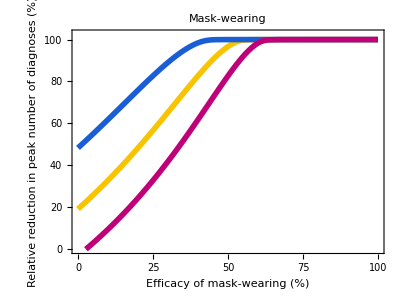

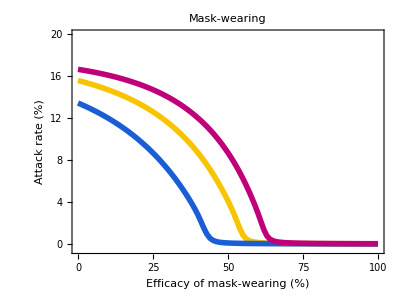

-Graphics-

```mathematica
imagePadding={{80,15},{73,7.5}};

SS25=ListLinePlot[{PeakMaskBaseline,PeakMaskMin,PeakMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,102.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of mask-wearing (%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS25",".pdf"],SS25];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS25",".eps"],SS25];

SS26=ListLinePlot[{AttackRateMaskBaseline,AttackRateMaskMin,AttackRateMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-0.5,20}},AxesOrigin->{0,0},Filling->{1->{2}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of mask-wearing (%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS26",".pdf"],SS26];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS26",".eps"],SS26];

SS27=ListLinePlot[{PeakTimingMaskBaseline,PeakTimingMaskMin,PeakTimingMaskMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,365 5/2+20}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{"","","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],Graphics[{RGBColor[185/255,76/255,225/255],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of mask-wearing (%)",None}},ImagePadding->imagePadding,PlotRangePadding->None,PlotLabel->Style[Row[{"Mask-wearing"}],17,Black],PlotLegends->LineLegend[Table[Style[Row[{label}],Black,13,"Text"],{label,{"2.5","2","3"}}],LegendLabel->Style["Basic reproduction number",Black,13,"Text"]],FrameTicks->{{{{0,"0"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3/2,"18"},{365 5/2,"30"}},None},{Automatic,None}}]
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS27",".pdf"],SS27];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS27",".eps"],SS27];
```

```mathematica
Subscript[t, end]=1.5;
ReductionFactor=Table[i,{i,0,1,0.01}];

PeakGovBaseline=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakGovMin=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberMin,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakGovMax=PeakRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberMax,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovBaseline=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovMin=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberMin,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

AttackRateGovMax=AttackRateRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberMax,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovBaseline=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberBaseline,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovMin=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberMin,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]

PeakTimingGovMax=PeakTimingRange["ContactReductionGovernment",Join[ParametersSensitivityAnalyses[RelativeInfectivityBaseline,ProportionMildSymptomsBaseline,RecoveryRateMildSymptomsBaseline,DiagnosisRateBaseline,BasicReproductionNumberMax,RelativeSusceptibilityAwarenessBaseline,RateAwarenessFadingSusceptibleExposedMildSymptomsBaseline,RateAwarenessFadingSevereSymptomsBaseline,AcquisitionRateAwarenessBaseline,DiagnosisRateAwareBaseline,StartTimeBaseline],{Subscript[r, 4]-> factor}]]
```

{{100.,19.1862},{99.,19.1863},{98.,19.1863},{97.,19.1863},{96.,19.1864},{95.,19.1865},{94.,19.1865},{93.,19.1865},{92.,19.1866},{91.,19.1866},{90.,19.1867},{89.,19.1868},{88.,19.1869},{87.,19.187},{86.,19.187},{85.,19.1871},{84.,19.1872},{83.,19.1873},{82.,19.1874},{81.,19.1875},{80.,19.1876},{79.,19.1878},{78.,19.1879},{77.,19.1881},{76.,19.1883},{75.,19.1885},{74.,19.1887},{73.,19.1889},{72.,19.1892},{71.,19.1895},{70.,19.1898},{69.,19.1902},{68.,19.1905},{67.,19.1909},{66.,19.1914},{65.,19.1919},{64.,19.1925},{63.,19.1931},{62.,19.1938},{61.,19.1946},{60.,19.1955},{59.,19.1964},{58.,19.1974},{57.,19.1986},{56.,19.1999},{55.,19.2013},{54.,19.2028},{53.,19.2045},{52.,19.2064},{51.,19.2085},{50.,19.2108},{49.,19.2133},{48.,19.2161},{47.,19.2192},{46.,19.2225},{45.,19.2263},{44.,19.2304},{43.,19.2349},{42.,19.2399},{41.,19.2454},{40.,19.2514},{39.,19.2581},{38.,19.2654},{37.,19.2734},{36.,19.2822},{35.,19.2918},{34.,19.3023},{33.,19.3137},{32.,19.3263},{31.,19.3398},{30.,19.3546},{29.,19.3705},{28.,19.3877},{27.,19.4063},{26.,19.4262},{25.,19.4475},{24.,19.4702},{23.,19.4943},{22.,19.5197},{21.,19.5465},{20.,19.5743},{19.,19.6032},{18.,19.6328},{17.,19.6628},{16.,19.6929},{15.,19.7226},{14.,19.7511},{13.,19.7779},{12.,19.8019},{11.,19.8219},{10.,19.8368},{9.,19.8448},{8.,19.8442},{7.,19.8326},{6.,19.8076},{5.,19.7663},{4.,19.7055},{3.,19.6212},{2.,19.5093},{1.,19.3653},{0.,19.1837}}

{{100.,48.3183},{99.,48.3183},{98.,48.3184},{97.,48.3184},{96.,48.3184},{95.,48.3184},{94.,48.3184},{93.,48.3184},{92.,48.3184},{91.,48.3184},{90.,48.3184},{89.,48.3184},{88.,48.3185},{87.,48.3185},{86.,48.3185},{85.,48.3185},{84.,48.3185},{83.,48.3185},{82.,48.3185},{81.,48.3186},{80.,48.3186},{79.,48.3186},{78.,48.3186},{77.,48.3186},{76.,48.3187},{75.,48.3187},{74.,48.3187},{73.,48.3187},{72.,48.3188},{71.,48.3188},{70.,48.3188},{69.,48.3189},{68.,48.3189},{67.,48.319},{66.,48.319},{65.,48.3191},{64.,48.3191},{63.,48.3192},{62.,48.3193},{61.,48.3193},{60.,48.3194},{59.,48.3195},{58.,48.3196},{57.,48.3197},{56.,48.3198},{55.,48.3199},{54.,48.3201},{53.,48.3202},{52.,48.3203},{51.,48.3205},{50.,48.3207},{49.,48.3209},{48.,48.3211},{47.,48.3213},{46.,48.3216},{45.,48.3218},{44.,48.3221},{43.,48.3224},{42.,48.3228},{41.,48.3231},{40.,48.3235},{39.,48.3239},{38.,48.3244},{37.,48.3249},{36.,48.3254},{35.,48.3259},{34.,48.3264},{33.,48.327},{32.,48.3277},{31.,48.3283},{30.,48.329},{29.,48.3297},{28.,48.3305},{27.,48.3313},{26.,48.3321},{25.,48.333},{24.,48.3338},{23.,48.3347},{22.,48.3356},{21.,48.3365},{20.,48.3375},{19.,48.3384},{18.,48.3393},{17.,48.3402},{16.,48.341},{15.,48.3418},{14.,48.3425},{13.,48.3431},{12.,48.3435},{11.,48.3438},{10.,48.3438},{9.,48.3436},{8.,48.3431},{7.,48.3422},{6.,48.3409},{5.,48.339},{4.,48.3365},{3.,48.3332},{2.,48.3291},{1.,48.3239},{0.,48.3176}}

{{100.,-3.12285},{99.,-3.12267},{98.,-3.12256},{97.,-3.12239},{96.,-3.12221},{95.,-3.12203},{94.,-3.12183},{93.,-3.12156},{92.,-3.12135},{91.,-3.12108},{90.,-3.12081},{89.,-3.1205},{88.,-3.12025},{87.,-3.11989},{86.,-3.11949},{85.,-3.11912},{84.,-3.11864},{83.,-3.11819},{82.,-3.11764},{81.,-3.11705},{80.,-3.11634},{79.,-3.11563},{78.,-3.11483},{77.,-3.11393},{76.,-3.11295},{75.,-3.11183},{74.,-3.11058},{73.,-3.10917},{72.,-3.10754},{71.,-3.10582},{70.,-3.10381},{69.,-3.10157},{68.,-3.09902},{67.,-3.09615},{66.,-3.09293},{65.,-3.0893},{64.,-3.08518},{63.,-3.08045},{62.,-3.07519},{61.,-3.06915},{60.,-3.06227},{59.,-3.05449},{58.,-3.04566},{57.,-3.03549},{56.,-3.02397},{55.,-3.01088},{54.,-2.99591},{53.,-2.97885},{52.,-2.95942},{51.,-2.93725},{50.,-2.91205},{49.,-2.88339},{48.,-2.85075},{47.,-2.81361},{46.,-2.77154},{45.,-2.72375},{44.,-2.66962},{43.,-2.60834},{42.,-2.53915},{41.,-2.46098},{40.,-2.37297},{39.,-2.27403},{38.,-2.16286},{37.,-2.03839},{36.,-1.89927},{35.,-1.74412},{34.,-1.5716},{33.,-1.38027},{32.,-1.16893},{31.,-0.936167},{30.,-0.680941},{29.,-0.402169},{28.,-0.099351},{27.,0.227846},{26.,0.579179},{25.,0.953862},{24.,1.35019},{23.,1.76552},{22.,2.19623},{21.,2.63733},{20.,3.08246},{19.,3.5237},{18.,3.95156},{17.,4.3549},{16.,4.72116},{15.,5.03628},{14.,5.28532},{13.,5.45262},{12.,5.52259},{11.,5.48041},{10.,5.3126},{9.,5.00856},{8.,4.56106},{7.,3.96798},{6.,3.23308},{5.,2.36717},{4.,1.38811},{3.,0.320487},{2.,-0.80721},{1.,-1.9659},{0.,-3.13045}}

{{100.,15.5894},{99.,15.5894},{98.,15.5894},{97.,15.5894},{96.,15.5894},{95.,15.5894},{94.,15.5894},{93.,15.5894},{92.,15.5894},{91.,15.5894},{90.,15.5894},{89.,15.5894},{88.,15.5894},{87.,15.5894},{86.,15.5894},{85.,15.5894},{84.,15.5894},{83.,15.5894},{82.,15.5894},{81.,15.5894},{80.,15.5894},{79.,15.5894},{78.,15.5894},{77.,15.5894},{76.,15.5894},{75.,15.5894},{74.,15.5893},{73.,15.5893},{72.,15.5893},{71.,15.5893},{70.,15.5893},{69.,15.5893},{68.,15.5893},{67.,15.5893},{66.,15.5893},{65.,15.5893},{64.,15.5893},{63.,15.5892},{62.,15.5892},{61.,15.5892},{60.,15.5892},{59.,15.5892},{58.,15.5891},{57.,15.5891},{56.,15.5891},{55.,15.589},{54.,15.589},{53.,15.589},{52.,15.5889},{51.,15.5889},{50.,15.5888},{49.,15.5888},{48.,15.5887},{47.,15.5886},{46.,15.5885},{45.,15.5884},{44.,15.5883},{43.,15.5882},{42.,15.5881},{41.,15.588},{40.,15.5878},{39.,15.5877},{38.,15.5875},{37.,15.5873},{36.,15.5871},{35.,15.5869},{34.,15.5866},{33.,15.5863},{32.,15.586},{31.,15.5857},{30.,15.5853},{29.,15.5849},{28.,15.5845},{27.,15.5841},{26.,15.5836},{25.,15.5831},{24.,15.5825},{23.,15.5819},{22.,15.5813},{21.,15.5807},{20.,15.58},{19.,15.5793},{18.,15.5786},{17.,15.5778},{16.,15.5771},{15.,15.5764},{14.,15.5757},{13.,15.575},{12.,15.5744},{11.,15.5739},{10.,15.5735},{9.,15.5733},{8.,15.5733},{7.,15.5736},{6.,15.5742},{5.,15.5752},{4.,15.5767},{3.,15.5787},{2.,15.5815},{1.,15.585},{0.,15.5895}}

{{100.,13.1731},{99.,13.2476},{98.,13.2998},{97.,13.3369},{96.,13.3636},{95.,13.3831},{94.,13.3974},{93.,13.4081},{92.,13.4162},{91.,13.4223},{90.,13.4269},{89.,13.4305},{88.,13.4333},{87.,13.4355},{86.,13.4373},{85.,13.4386},{84.,13.4397},{83.,13.4406},{82.,13.4413},{81.,13.4419},{80.,13.4423},{79.,13.4427},{78.,13.443},{77.,13.4432},{76.,13.4434},{75.,13.4436},{74.,13.4438},{73.,13.4439},{72.,13.444},{71.,13.4441},{70.,13.4441},{69.,13.4442},{68.,13.4442},{67.,13.4443},{66.,13.4443},{65.,13.4443},{64.,13.4443},{63.,13.4444},{62.,13.4444},{61.,13.4444},{60.,13.4444},{59.,13.4444},{58.,13.4444},{57.,13.4444},{56.,13.4444},{55.,13.4444},{54.,13.4444},{53.,13.4444},{52.,13.4444},{51.,13.4444},{50.,13.4444},{49.,13.4444},{48.,13.4444},{47.,13.4444},{46.,13.4444},{45.,13.4444},{44.,13.4444},{43.,13.4444},{42.,13.4443},{41.,13.4443},{40.,13.4443},{39.,13.4443},{38.,13.4443},{37.,13.4443},{36.,13.4442},{35.,13.4442},{34.,13.4442},{33.,13.4442},{32.,13.4441},{31.,13.4441},{30.,13.4441},{29.,13.4441},{28.,13.444},{27.,13.444},{26.,13.444},{25.,13.4439},{24.,13.4439},{23.,13.4438},{22.,13.4438},{21.,13.4438},{20.,13.4437},{19.,13.4437},{18.,13.4437},{17.,13.4436},{16.,13.4436},{15.,13.4435},{14.,13.4435},{13.,13.4435},{12.,13.4435},{11.,13.4435},{10.,13.4435},{9.,13.4435},{8.,13.4435},{7.,13.4435},{6.,13.4436},{5.,13.4437},{4.,13.4438},{3.,13.4439},{2.,13.4441},{1.,13.4443},{0.,13.4446}}

{{100.,16.6592},{99.,16.6592},{98.,16.6592},{97.,16.6592},{96.,16.6592},{95.,16.6592},{94.,16.6592},{93.,16.6592},{92.,16.6592},{91.,16.6592},{90.,16.6592},{89.,16.6591},{88.,16.6591},{87.,16.6591},{86.,16.6591},{85.,16.6591},{84.,16.6591},{83.,16.6591},{82.,16.6591},{81.,16.6591},{80.,16.6591},{79.,16.6591},{78.,16.6591},{77.,16.659},{76.,16.659},{75.,16.659},{74.,16.659},{73.,16.659},{72.,16.659},{71.,16.6589},{70.,16.6589},{69.,16.6589},{68.,16.6588},{67.,16.6588},{66.,16.6587},{65.,16.6587},{64.,16.6586},{63.,16.6585},{62.,16.6585},{61.,16.6584},{60.,16.6583},{59.,16.6581},{58.,16.658},{57.,16.6579},{56.,16.6577},{55.,16.6575},{54.,16.6572},{53.,16.657},{52.,16.6567},{51.,16.6564},{50.,16.656},{49.,16.6555},{48.,16.655},{47.,16.6545},{46.,16.6538},{45.,16.6531},{44.,16.6523},{43.,16.6513},{42.,16.6502},{41.,16.649},{40.,16.6477},{39.,16.6462},{38.,16.6444},{37.,16.6425},{36.,16.6403},{35.,16.6379},{34.,16.6352},{33.,16.6322},{32.,16.6288},{31.,16.6251},{30.,16.6211},{29.,16.6166},{28.,16.6117},{27.,16.6063},{26.,16.6005},{25.,16.5943},{24.,16.5876},{23.,16.5806},{22.,16.5731},{21.,16.5654},{20.,16.5575},{19.,16.5494},{18.,16.5414},{17.,16.5336},{16.,16.5263},{15.,16.5196},{14.,16.5138},{13.,16.5093},{12.,16.5063},{11.,16.5051},{10.,16.5059},{9.,16.5092},{8.,16.5149},{7.,16.5234},{6.,16.5348},{5.,16.549},{4.,16.566},{3.,16.5857},{2.,16.608},{1.,16.6326},{0.,16.6593}}

{{100.,366.872},{99.,361.959},{98.,357.313},{97.,352.968},{96.,348.824},{95.,344.88},{94.,341.103},{93.,337.46},{92.,333.985},{91.,330.609},{90.,327.367},{89.,324.225},{88.,321.151},{87.,318.209},{86.,315.302},{85.,312.494},{84.,309.754},{83.,307.08},{82.,304.473},{81.,301.933},{80.,299.426},{79.,296.987},{78.,294.614},{77.,292.274},{76.,289.968},{75.,287.729},{74.,285.523},{73.,283.35},{72.,281.211},{71.,279.139},{70.,277.101},{69.,275.095},{68.,273.09},{67.,271.151},{66.,269.246},{65.,267.341},{64.,265.503},{63.,263.665},{62.,261.827},{61.,260.055},{60.,258.251},{59.,256.479},{58.,254.741},{57.,253.003},{56.,251.265},{55.,249.528},{54.,247.79},{53.,246.052},{52.,244.314},{51.,242.609},{50.,240.871},{49.,239.133},{48.,237.429},{47.,235.691},{46.,233.986},{45.,232.248},{44.,230.544},{43.,228.839},{42.,227.135},{41.,225.464},{40.,223.759},{39.,222.088},{38.,220.417},{37.,218.746},{36.,217.108},{35.,215.471},{34.,213.833},{33.,212.195},{32.,210.591},{31.,208.953},{30.,207.383},{29.,205.778},{28.,204.207},{27.,202.637},{26.,201.066},{25.,199.495},{24.,197.958},{23.,196.42},{22.,194.883},{21.,193.379},{20.,191.841},{19.,190.337},{18.,188.833},{17.,187.363},{16.,185.859},{15.,184.388},{14.,182.918},{13.,181.447},{12.,180.01},{11.,178.54},{10.,177.102},{9.,175.665},{8.,174.195},{7.,172.758},{6.,171.354},{5.,169.917},{4.,168.48},{3.,167.076},{2.,165.639},{1.,164.235},{0.,162.798}}

{{100.,476.93},{99.,471.248},{98.,465.834},{97.,460.687},{96.,455.74},{95.,450.994},{94.,446.449},{93.,442.071},{92.,437.826},{91.,433.715},{90.,429.705},{89.,425.828},{88.,422.085},{87.,418.408},{86.,414.832},{85.,411.323},{84.,407.914},{83.,404.571},{82.,401.296},{81.,398.088},{80.,394.946},{79.,391.871},{78.,388.863},{77.,385.889},{76.,382.948},{75.,380.073},{74.,377.266},{73.,374.492},{72.,371.751},{71.,369.044},{70.,366.404},{69.,363.763},{68.,361.19},{67.,358.65},{66.,356.143},{65.,353.703},{64.,351.264},{63.,348.857},{62.,346.484},{61.,344.145},{60.,341.839},{59.,339.533},{58.,337.293},{57.,335.054},{56.,332.882},{55.,330.709},{54.,328.57},{53.,326.431},{52.,324.326},{51.,322.253},{50.,320.215},{49.,318.176},{48.,316.171},{47.,314.165},{46.,312.193},{45.,310.222},{44.,308.283},{43.,306.345},{42.,304.406},{41.,302.501},{40.,300.596},{39.,298.691},{38.,296.786},{37.,294.881},{36.,293.009},{35.,291.104},{34.,289.199},{33.,287.328},{32.,285.423},{31.,283.518},{30.,281.646},{29.,279.741},{28.,277.836},{27.,275.964},{26.,274.059},{25.,272.188},{24.,270.282},{23.,268.411},{22.,266.506},{21.,264.634},{20.,262.763},{19.,260.891},{18.,259.019},{17.,257.148},{16.,255.276},{15.,253.438},{14.,251.566},{13.,249.728},{12.,247.89},{11.,246.052},{10.,244.247},{9.,242.409},{8.,240.604},{7.,238.799},{6.,236.994},{5.,235.19},{4.,233.385},{3.,231.613},{2.,229.842},{1.,228.071},{0.,226.299}}

{{100.,310.89},{99.,306.345},{98.,302.167},{97.,298.223},{96.,294.513},{95.,291.004},{94.,287.662},{93.,284.453},{92.,281.412},{91.,278.471},{90.,275.63},{89.,272.889},{88.,270.216},{87.,267.642},{86.,265.169},{85.,262.729},{84.,260.39},{83.,258.084},{82.,255.844},{81.,253.672},{80.,251.533},{79.,249.461},{78.,247.455},{77.,245.45},{76.,243.512},{75.,241.607},{74.,239.735},{73.,237.897},{72.,236.092},{71.,234.287},{70.,232.516},{69.,230.744},{68.,229.007},{67.,227.269},{66.,225.531},{65.,223.793},{64.,222.055},{63.,220.35},{62.,218.612},{61.,216.908},{60.,215.203},{59.,213.499},{58.,211.794},{57.,210.123},{56.,208.419},{55.,206.781},{54.,205.11},{53.,203.472},{52.,201.868},{51.,200.23},{50.,198.659},{49.,197.055},{48.,195.484},{47.,193.914},{46.,192.376},{45.,190.839},{44.,189.335},{43.,187.831},{42.,186.327},{41.,184.823},{40.,183.352},{39.,181.915},{38.,180.478},{37.,179.041},{36.,177.604},{35.,176.2},{34.,174.796},{33.,173.426},{32.,172.022},{31.,170.652},{30.,169.315},{29.,167.978},{28.,166.608},{27.,165.304},{26.,163.968},{25.,162.664},{24.,161.327},{23.,160.024},{22.,158.72},{21.,157.417},{20.,156.113},{19.,154.81},{18.,153.507},{17.,152.203},{16.,150.9},{15.,149.563},{14.,148.226},{13.,146.889},{12.,145.552},{11.,144.215},{10.,142.845},{9.,141.475},{8.,140.138},{7.,138.801},{6.,137.464},{5.,136.161},{4.,134.924},{3.,133.721},{2.,132.584},{1.,131.515},{0.,130.479}}

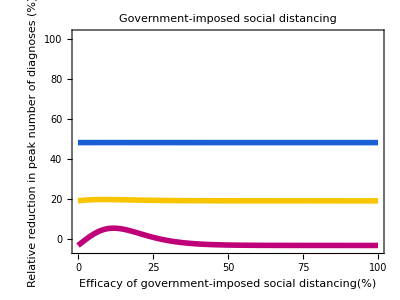

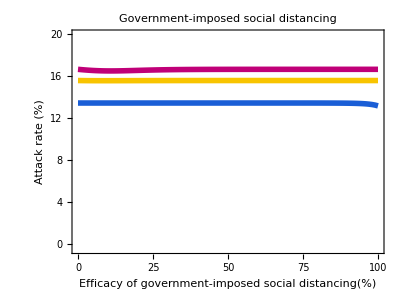

-Graphics-

```mathematica
imagePadding={{80,15},{73,7.5}};

SS28=ListLinePlot[{PeakGovBaseline,PeakGovMin,PeakGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-5,102.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Relative reduction in\npeak number of diagnoses (%)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS28",".pdf"],SS28];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS28",".eps"],SS28];


SS29=ListLinePlot[{AttackRateGovBaseline,AttackRateGovMin,AttackRateGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{-0.5,20}},AxesOrigin->{0,0},Filling->{1->{2}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotRangePadding->None,PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],ImagePadding->imagePadding,FrameLabel-> {{"Attack rate (%)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS29",".pdf"],SS29];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS29",".eps"],SS29];

SS30=ListLinePlot[{PeakTimingGovBaseline,PeakTimingGovMin,PeakTimingGovMax},AspectRatio->0.75,ImageSize->400,PlotRange->{All,{0,800}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotMarkers->{"","","",Graphics[{RGBColor[28/255,162/255,0],Thick,Circle[]},ImageSize->10],Graphics[{RGBColor[185/255,76/255,225/255],Thick,Circle[]},ImageSize->10],""},PlotStyle->{{Thickness[0.01],RGBColor[248/255,196/255,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]},{Thickness[0.01],RGBColor[192/255,0,120/255]}},FrameLabel-> {{"Time until the peak\nof diagnoses (months)",None},{"Efficacy of government-imposed\nsocial distancing(%)",None}},ImagePadding->imagePadding,PlotRangePadding->None,PlotLabel->Style[Row[{"Government-imposed social distancing"}],17,Black],PlotLegends->LineLegend[Table[Style[Row[{label}],Black,13,"Text"],{label,{"2.5","2","3"}}],LegendLabel->Style["Basic reproduction number",Black,13,"Text"]],FrameTicks->{{{{0,"0"},{365/2,"6"},{365,"12"},{365 2,"24"},{365 3/2,"18"}},None},{Automatic,None}}]

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS30",".pdf"],SS30];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaLadies//Submission//PlosMedicine//Resubmission//FinalFigures//SS30",".eps"],SS30];
```